# Fundamental pH Niche of K pneumoniae

This notebook is simplified from Mathematica notebook "Fundamental pH Niche of K pneumoniae-MMAv5", section "Mathematica v5.2 Modified".

Growth parameters have been updated with numbers in "Growth Parameters vs pH".  The notebook has been simplified to include only sections needed in support of the publication "Fundamental pH Niche of Klebsiella pneumonia".

## Model Setup

### Plot Setup

#### Color Scheme

```mathematica
(* Text color - must be defined first as other colors reference it *)
txc (* Text *) = RGBColor[13233/65535., 65535/65535., 1/65535.];

bgc2D (*2D Bkgrd inside Frame*) = RGBColor[0/65535., 21758/65535., 0/65535.];

axc (* Axis *) = txc;

bgc (* Bkgrd *) = RGBColor[1216/65535., 22824/65535., 1637/65535.];

bxc (* Box *) = txc;

fgc (* FaceGrid *) = txc;

glc (* GridLine *) = RGBColor[786/65535., 31981/65535., 786/65535.];

tkc (* Ticks *) = txc;
```

```mathematica
ratecolor[r_]:=If[r≤0.5,RGBColor[2. r,1.,1.-2. r],RGBColor[1.,2. (1.-r),0]];
```

#### Data series Color Scheme

```mathematica
Off[General::spell1];
Clear[D1, D2, D3, D4, D5, D6];
D1=RGBColor[59624/65535,24156/65535,24156/65535];
D2=RGBColor[19785/65535,65535/65535,27498/65535];
D3=RGBColor[5138/65535,60391/65535,59624/65535];
D4=RGBColor[60391/65535,60908/65535,3336/65535];
D5=RGBColor[60908/65535,32119/65535,59624/65535];D6=RGBColor[65535/65535,38548/65535,15676/65535];

Clear[D1d, D2d, D3d, D4d, D5d, D6d];
D1d=RGBColor[152/255,74/255,74/255];
D2d=RGBColor[61/255,155/255,77/255];
D3d=RGBColor[63/255,157/255,155/255];
D4d=RGBColor[152/255,149/255,8/255];
D5d=RGBColor[138/255,84/255,135/255];D6d=RGBColor[167/255,105/255,53/255];

Clear[D1dr, D2dr, D3dr, D4dr, D5dr, D6dr];
D1dr=RGBColor[135/255,65/255,65/255];
D2dr=RGBColor[56/255,144/255,56/255];
D3dr=RGBColor[52/255,128/255,126/255];
D4dr=RGBColor[124/255,121/255,6/255];
D5dr=RGBColor[124/255,76/255,122/255];D6dr=RGBColor[152/255,95/255,48/255];

Clear[D1dst, D2dst, D3dst, D4dst, D5dst, D6dst];
D1dst=RGBColor[100/255,60/255,60/255];
D2dst=RGBColor[42/255,108/255,53/255];
D3dst=RGBColor[44/255,106/255,106/255];
D4dst=RGBColor[101/255,99/255,29/255];
D5dst=RGBColor[99/255,61/255,97/255];D6dst=RGBColor[114/255,71/255,36/255];
On[General::spell1]
```

#### 2D Graphics Options (Presentation)

```mathematica
SetOptions[Plot,
Background->bgc (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->9},
Frame -> True,
FrameStyle->{Thickness[0.008],fmc},
GridLines->{Table[{x,{glc, Thickness[0.003]}}, {x, 1,  6}],Table[{y,{glc,  Thickness[0.003]}}, {y, 0, 40, 10}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),
PlotRange->{{0,7},{-2,45}},PlotStyle->{Thickness[0.008]}
];
```

```mathematica
SetOptions[Graphics,
Background->bgc (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->9},
Frame -> True,
FrameStyle->{Thickness[0.008],fmc},
GridLines->{Table[{x,{glc, Thickness[0.003]}}, {x, 0,  6}],Table[{y,{glc,  Thickness[0.003]}}, {y, 0, 40, 10}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),PlotRange->{{0,7},{-2,45}}
];
```

#### 2D Graphics Options (Print)

```mathematica
SetOptions[Plot,
Background->None (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->7},
Frame -> True,
FrameStyle->{Thickness[0.008],fmc},
ImageSize->4×72
];
```

```mathematica
SetOptions[Graphics,
Background->None (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->7},
Frame -> True,
FrameStyle->{Thickness[0.008],fmc},
ImageSize->4×72
];
```

#### 3D Graphics Options (Presentation)

```mathematica
Off[General::spell, General::spell1];
bxfmTkns=tkTkns= Thickness[0.005];(*Thickness of Box Frame & Ticks*)
xtkpl=ytkpl=ztkml=0.; (* + Ticks length *)
xtkml=ytkml=ztkpl=0.016; (* - Ticks length *)
SetOptions[Graphics3D, Axes->True,AxesEdge->{{-1,-1},{1,-1},{1,1}},AxesLabel->None,Boxed->False,BoxRatios->{1,1,0.8},Background->bgc(*None gives a transparent plot*), BaseStyle->{FontFamily->"Helvetica",FontSize->9},

Ticks->{
(* X-Ticks *) Table[{i, i, {xtkpl,xtkml}, {tkc, tkTkns}}, {i, 4, 9}],
(* Y-Ticks *) Table[{i, i, {ytkpl,ytkml}, {tkc, tkTkns}}, {i, 0, 5, 1}],
(* Z-Ticks *) 
Range[5, 25, 5]},PlotRange->{{3.8,9.2},{0,5},{0,20}},ViewPoint->{1.170,-2.290,0.500}];
On[General::spell, General::spell1]
```

```mathematica
threeDFrame=Show[Graphics3D[{RGBColor[1, 1, 1], Point[{3.5, 2.5, 0.5}]}]]
```

-Graphics3D-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","ThreeDFrame_2.eps"}], threeDFrame, "EPS"])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/ThreeDFrame_2.eps

```mathematica
Off[General::spell, General::spell1];
bxfmTkns=tkTkns= Thickness[0.005];(*Thickness of Box Frame & Ticks*)
xtkpl=ytkpl=ztkml=0.; (* + Ticks length *)
xtkml=ytkml=ztkpl=0.016; (* - Ticks length *)
SetOptions[Graphics3D, Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,1}},AxesLabel->None,Boxed->False,BoxRatios->{1,1,0.8},Background->bgc(*None gives a transparent plot*), BaseStyle->{FontFamily->"Helvetica",FontSize->9},

Ticks->{
(* X-Ticks *) Table[{i, i, {xtkpl,xtkml}, {tkc, tkTkns}}, {i, 4, 9}],
(* Y-Ticks *) Table[{i, i, {ytkpl,ytkml}, {tkc, tkTkns}}, {i, 0, 5, 1}],
(* Z-Ticks *) 
Range[5, 25, 5]},PlotRange->{{3.8,9.2},{0,5},{0,20}},ViewPoint->{-1.170,-2.290,0.500}];
On[General::spell, General::spell1]
```

```mathematica
threeDFrameLeft=Show[Graphics3D[{RGBColor[1, 1, 1], Point[{3.5, 2.5, 0.5}]}]]
```

-Graphics3D-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","threeDFrameLeft.eps"}], threeDFrameLeft, "EPS"])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/threeDFrameLeft.eps

#### 3D Graphics Options (Print)

```mathematica
Off[General::spell, General::spell1];
bxfmTkns=tkTkns= Thickness[0.005];(*Thickness of Box Frame & Ticks*)
xtkpl=ytkpl=ztkml=0.; (* + Ticks length *)
xtkml=ytkml=ztkpl=0.016; (* - Ticks length *)
SetOptions[Graphics3D, Axes->True,AxesEdge->{{-1,-1},{1,-1},{1,1}},AxesLabel->None,Boxed->False,BoxRatios->{1,1,0.8},Background->None(*None gives a transparent plot*), BaseStyle->{FontFamily->"Helvetica",FontSize->7},

Ticks->{
(* X-Ticks *) Table[{i, i, {xtkpl,xtkml}, {Black, tkTkns}}, {i, 4, 9}],
(* Y-Ticks *) Table[{i, i, {ytkpl,ytkml}, {Black, tkTkns}}, {i, 0, 5, 1}],
(* Z-Ticks *) 
Range[5, 25, 5]},PlotRange->{{3.8,9.2},{0,5},{0,20}},ViewPoint->{1.170,-2.290,0.500}];
On[General::spell, General::spell1]
```

```mathematica
threeDFrame=Show[Graphics3D[{RGBColor[1, 1, 1], Point[{3.5, 2.5, 0.5}]}]]
```

-Graphics3D-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","ThreeDFrame_R.eps"}], threeDFrame, "EPS", ImageSize->158])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/ThreeDFrame_R.eps

```mathematica
Off[General::spell, General::spell1];
bxfmTkns=tkTkns= Thickness[0.005];(*Thickness of Box Frame & Ticks*)
xtkpl=ytkpl=ztkml=0.; (* + Ticks length *)
xtkml=ytkml=ztkpl=0.016; (* - Ticks length *)
SetOptions[Graphics3D, Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,1}},AxesLabel->None,Boxed->False,BoxRatios->{1,1,0.8},Background->None(*None gives a transparent plot*), BaseStyle->{FontFamily->"Helvetica",FontSize->7},

Ticks->{
(* X-Ticks *) Table[{i, i, {xtkpl,xtkml}, {Black, tkTkns}}, {i, 4, 9}],
(* Y-Ticks *) Table[{i, i, {ytkpl,ytkml}, {Black, tkTkns}}, {i, 0, 5, 1}],
(* Z-Ticks *) 
Range[5, 25, 5]},PlotRange->{{3.8,9.2},{0,5},{0,20}},ViewPoint->{-1.170,-2.290,0.500}];
On[General::spell, General::spell1]
```

```mathematica
threeDFrameLeft=Show[Graphics3D[{RGBColor[1, 1, 1], Point[{3.5, 2.5, 0.5}]}]]
```

-Graphics3D-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","threeDFrameLeft.eps"}], threeDFrameLeft, "EPS"])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/threeDFrameLeft.eps

### Setup

#### Growth Model Setup with The Casheing Method

```mathematica
Off[General::spell, General::spell1];

expmtlpH=.;SGR=.;SGRvspHData=.;wkgPrcsn=.
SGRvspHroot=.;SGRpHLowBnd=.;SGRpHHighBnd=.
μMaxSolve=.;μMax=.;μMaxpH=.
Clear[pH,SGRvspHFitPrmtr, SGRvspHFitEqtn, SGRvspH,μo];

wkgPrcsn=Automatic;
expmtlpH={395,407,419,446,497,597,700,792,845,878,892,910}/100;
SGR={0,135,295,440,663,861,979,845,643,337,293,0}/1000(* hr^-1 *);
SGRvspHData=Transpose[{expmtlpH,SGR}];
Clear[expmtlpH,SGR];

SGRvspH[pH_]=
Module[{a,b,c,d,e,f,x,FitPrmtr},
FitPrmtr=
FindFit[SGRvspHData,
a+b x+c x^2+d x^3+e x^4+f x^5,
{a,b,c,d,e,f},x,WorkingPrecision->wkgPrcsn
];
a+b pH+c pH^2+d pH^3+e pH^4+f pH^5/.FitPrmtr
];
SGRvspHroot=Solve[SGRvspH[pH]==0,pH];
SGRpHLowBnd=SGRvspHroot[[1,1,2]];
SGRpHHighBnd=SGRvspHroot[[4,1,2]];

μo[pH_?NumericQ/;pH<SGRpHLowBnd||pH>SGRpHHighBnd]:=0
μo[pH_?NumericQ/;(pH≥SGRpHLowBnd)∧(pH≤SGRpHHighBnd)]:= SGRvspH[pH]

μMaxSolve=FindMaximum[μo[pH],{pH,69/10}, WorkingPrecision->wkgPrcsn];
μMax=μMaxSolve[[1]](* hr^-1 *);
μMaxpH=μMaxSolve[[2, 1, 2]];
Remove[SGRvspHroot, μMaxSolve];

(*Equation 2 can now be defined *)
s=.;Ks=.
Clear[μ, Nμ];
μ[pH_, s_]:=μo[pH] s/(Ks+s) ;
Nμ[pH_?NumericQ,s_?NumericQ]:=μ[pH,s]/μMax;


YOutsideNiche=.;expmtlpH=.;nYieldData=.;YvspHdata=.
YieldvspHRoot=.;YieldpHLowBnd=.;YieldpHHighBnd=.
Clear[YieldvspH, NYield];

expmtlpH=
{395,407,419,446,497,597,700,792,845,878,892,910}/100;
nYieldData={0,320,479,641,809,968,950,814,511,380,302,0}/1000;
YvspHdata=Transpose[{expmtlpH,nYieldData}];
Clear[expmtlpH,nYieldData];

YieldvspH[pH_]=
Module[{a,b,c,d,e,f,x,FitPrmtr},
FitPrmtr=
FindFit[YvspHdata,
a+b x+c x^2+d x^3+e x^4+f x^5,
{a,b,c,d,e,f},x,WorkingPrecision->wkgPrcsn
];
a+b pH+c pH^2+d pH^3+e pH^4+f pH^5/.FitPrmtr
];
YieldvspHRoot=Solve[YieldvspH[pH]==0,pH];
YieldpHLowBnd=YieldvspHRoot[[1,1,2]];
YieldpHHighBnd=YieldvspHRoot[[4,1,2]];

YOutsideNiche=1/10^5;NYield[pH_?NumericQ/;pH<YieldpHLowBnd||pH>YieldpHHighBnd]:=YOutsideNiche;
NYield[pH_?NumericQ/;(pH≥YieldpHLowBnd)∧(pH≤YieldpHHighBnd)]:=YieldvspH[pH];

Clear[nyieldMaxSolve,nyieldMax,nyieldMaxpH];
nyieldMaxSolve=FindMaximum[NYield[pH],{pH,7},WorkingPrecision->wkgPrcsn];
nyieldMax=nyieldMaxSolve[[1]];
nyieldMaxpH=nyieldMaxSolve[[2,1,2]];
Remove[nyieldMaxSolve];

(* Multiplying Normalized growth yield by the maximum, growth yield at pH 7, 82.2 g/mole glucose, we get growth yield. *)
MaxYieldpH7=.
Clear[Yield];
MaxYieldpH7=822/10000  ;(* mg/μmole glucose *)
Yield[pH_]:=MaxYieldpH7 × NYield[pH];(* mg/μmole glucose *)

(* Here let me define the pH niche boundary of K. pneumoniae. *)
pHNicheBoundaryLow=Max[SGRpHLowBnd, YieldpHLowBnd];
pHNicheBoundaryHigh=Min[SGRpHHighBnd, YieldpHHighBnd];
```

```mathematica
Clear[ReferencepH];
Ks=4; (* μMolar *)
so=500; (* μMolar *)
Tmax = 12 ;(* hr *)
ReferencepH=Rationalize[μMaxpH];
BMmultiplication=50;
sMin=so*1/1000 (* μMolar *);
```

```mathematica
Clear[Biomass, BiomassRef, Substrate, BiomassCache, BiomassRefCache, SubstrateCache];

Biomass[pH_, t_]:=
Module[{result, solution, M, MRef, s, time},
result=BiomassCache[pH, t];
If[
NumberQ[result], 
Return[result]
];

(* Biomass[pH, t] doesn't exist,use NDSolve to solve the system of differential equation. *)
solution=
NDSolve[
{MRef'[time]==MRef[time]×μ[ReferencepH,s[time]],M'[time]==M[time]×μ[pH,s[time]],
s'[time]==-MRef'[time]/Yield[ReferencepH]-M'[time]/Yield[pH],
MRef[0]==(so/2)×Yield[ReferencepH]/BMmultiplication,
M[0]==(so/2)×Yield[ReferencepH]/BMmultiplication ,
s[0]==so},
{MRef,M,s},{time,0,Tmax}

(*,AccuracyGoal->21,WorkingPrecision->24 *)
][[1]];

(* Biomass, BiomassRef and Substrate will be cached for future use. *)
BiomassRefCache[pH, time_]=MRef[time]/.solution;
BiomassCache[pH, time_]=M[time]/.solution;
SubstrateCache[pH, time_]=s[time]/.solution;

result=BiomassCache[pH, t];
If[
NumberQ[result],
Return[result],
$Failed
]
];

Biomass::usage="Biomass[pH, t] gives the biomass of K. pheumoniae, in mg/l, at time t growing at pH competing against reference population growing at optimum pH.";

BiomassRef[pH_, t_]:=
Module[{result, solution, M, MRef, s, time},
result=BiomassRefCache[pH, t];
If[
NumberQ[result], 
Return[result]
];

(* BiomassRef[pH, t] doesn't exist,use NDSolve to solve the system of differential equation. *)
solution=
NDSolve[
{MRef'[time]==MRef[time]×μ[ReferencepH,s[time]],M'[time]==M[time]×μ[pH,s[time]],
s'[time]==-MRef'[time]/Yield[ReferencepH]-M'[time]/Yield[pH],
MRef[0]==(so/2)×Yield[ReferencepH]/BMmultiplication,
M[0]==(so/2)×Yield[ReferencepH]/BMmultiplication ,
s[0]==so},
{MRef,M,s},{time,0,Tmax}

(*,AccuracyGoal->21,WorkingPrecision->24 *)
][[1]];

(* Biomass, BiomassRef and Substrate will be cached for future use. *)
BiomassRefCache[pH, time_]=MRef[time]/.solution;
BiomassCache[pH, time_]=M[time]/.solution;
SubstrateCache[pH, time_]=s[time]/.solution;

result=BiomassRefCache[pH, t];
If[
NumberQ[result],
Return[result],
$Failed
]
];

BiomassRef::usage="BiomassRef[pH, t] gives the biomass of reference K. pheumoniae population, in mg/l, at time t growing as if at optimum pH competing against another K. pheumoniae population growing at pH.";

Substrate[pH_, t_]:=
Module[{result, solution, M, MRef, s, time},
result=SubstrateCache[pH, t];
If[
NumberQ[result], 
Return[result]
];

(* Substrate[pH, t] doesn't exist,use NDSolve to solve the system of differential equation. *)
solution=
NDSolve[
{MRef'[time]==MRef[time]×μ[ReferencepH,s[time]],M'[time]==M[time]×μ[pH,s[time]],
s'[time]==-MRef'[time]/Yield[ReferencepH]-M'[time]/Yield[pH],
MRef[0]==(so/2)×Yield[ReferencepH]/BMmultiplication,
M[0]==(so/2)×Yield[ReferencepH]/BMmultiplication ,
s[0]==so},
{MRef,M,s},{time,0,Tmax}

(*,AccuracyGoal->21,WorkingPrecision->24*)
][[1]];

(* Biomass, BiomassRef and Substrate will be cached for future use. *)
BiomassRefCache[pH, time_]=MRef[time]/.solution;
BiomassCache[pH, time_]=M[time]/.solution;
SubstrateCache[pH, time_]=s[time]/.solution;

result=SubstrateCache[pH, t];
If[
NumberQ[result],
Return[result],
$Failed
]
];

Substrate::usage="Substrate[pH, t], in μMolar, gives the glucose concentration at time t of a medium with two K. pheumoniae population competing against one another.  Two K. pheumoniae populations are growing as if the medium pH were pH and ReferencepH.";
```

#### Growth Rate, Maximum Growth Rate, Normalized Growth Rate

Normalized specific growth rate is defined in the previous section.

```mathematica
Clear[growthRate, growthRateRef];
growthRate[pH_?NumericQ, t_?NumericQ](* mg/l hr *):=μ[pH, Substrate[pH,t]] × Biomass[pH, t];
growthRateRef[pH_?NumericQ, t_?NumericQ](* mg/l hr *):=μ[ReferencepH, Substrate[pH,t]] × BiomassRef[pH, t];
```

```mathematica
(* Defines global maximum growth rate of K pneumoniae in a competitive situation between itself and the Reference. Developed in Fundamental pH Hiche of K pneumoniae - MMAv5. *)
Clear[maxGrowthRateSolution];
maxGrowthRateSolution=FindMinimum[-growthRate[pH,t],{{pH,68/10,69/10},{t,36/10,37/10}}];
growthRateGblMaxTime=maxGrowthRateSolution[[2,2,2]];
growthRateGblMaxpH=maxGrowthRateSolution[[2,1,2]];
growthRateGblMax=-maxGrowthRateSolution[[1]];

Clear[GblNmGrowthRate];
GblNmGrowthRate[pH_?NumericQ, t_?NumericQ]:=growthRate[pH, t]/growthRateGblMax;
```

```mathematica
(* Defines maximum growth rate of K pneumoniae and Reference at local pHs. Developed in "Fundamental pH Hiche of K pneumoniae - MMAv5. *)
Clear[growthRateMax, growthRateMaxCache, growthRateMaxTime, growthRateMaxTimeCache, growthRateMaxRef, growthRateMaxRefCache, growthRateMaxTimeRef, growthRateMaxTimeRefCache];


growthRateMax[pH_?NumberQ](* mg/(l hr) *):=
Module[{result, solution, t},

result=growthRateMaxCache[pH];
If[NumberQ[result],Return[result]];

(* growthRateMax does not exist at the spicified pH.  New search needed to find the result. *)
solution=
Which[
(* Outside niche boundary. *)
pH≤pHNicheBoundaryLow||pH≥pHNicheBoundaryHigh, {0, {t->0}},
(* Within niche boundary. *)
pH>pHNicheBoundaryLow∧pH<pHNicheBoundaryHigh,
FindMinimum[-growthRate[pH, t], {t, 2, 3}]
];
growthRateMaxCache[pH]=-solution[[1]];
growthRateMaxTimeCache[pH]=t/.solution[[2]];

result=growthRateMaxCache[pH];
If[NumberQ[result],Return[result], $Failed];
];
growthRateMax::usage="growthRateMax[pH], mg/(l hr), gives the maximum growth rate of K. pheumoniae growing at pH in competition with another population growing at ReferencepH";


growthRateMaxTime[pH_?NumberQ](* hr *):=
Module[{result, solution, t},
result=growthRateMaxTimeCache[pH];
If[NumberQ[result],Return[result]];

(* growthRateMaxTime does not exist at the spicified pH.  New search needed to find the result. *)
solution=
Which[
(* Outside niche boundary. *)
pH≤pHNicheBoundaryLow||pH≥pHNicheBoundaryHigh, {0, {t->0}},
(* Within niche boundary. *)
pH>pHNicheBoundaryLow∧pH<pHNicheBoundaryHigh,
FindMinimum[-growthRate[pH, t], {t, 2, 3}]
];
growthRateMaxCache[pH]=-solution[[1]];
growthRateMaxTimeCache[pH]=t/.solution[[2]];

result=growthRateMaxTimeCache[pH];
If[NumberQ[result],Return[result], $Failed];
];
growthRateMaxTime::usage="growthRateMaxTime[pH], hr, gives the time at which growth rate of the population growing at pH reaches maximum.";


growthRateMaxRef[pH_?NumberQ](* mg/(l hr) *):=
Module[{result, solution, t},

result=growthRateMaxRefCache[pH];
If[NumberQ[result],Return[result]];

(* growthRateMaxRefCache does not exist at the spicified pH.  New search needed to find the result. *)
solution=
FindMinimum[-growthRateRef[pH, t], {t, 2, 3}];
growthRateMaxRefCache[pH]=-solution[[1]];
growthRateMaxTimeRefCache[pH]=t/.solution[[2]];

result=growthRateMaxRefCache[pH];
If[NumberQ[result],Return[result], $Failed];
];
growthRateMaxRef::usage="growthRateMaxRef[pH], mg/(l hr), gives the maximum growth rate of reference K. pheumoniae population growing at ReferencepH";


growthRateMaxTimeRef[pH_?NumberQ](* hr *):=
Module[{result, solution, t},

result=growthRateMaxTimeRefCache[pH];
If[NumberQ[result],Return[result]];

solution=FindMinimum[-growthRateRef[pH, t], {t, 2, 3}];
growthRateMaxRefCache[pH]=-solution[[1]];
growthRateMaxTimeRefCache[pH]=t/.solution[[2]];

result=growthRateMaxTimeRefCache[pH];
If[NumberQ[result],Return[result], $Failed];
];
growthRateMaxTimeRef::usage="growthRateMaxTimeRef[pH], hr, gives the time at which growth rate of reference K. pheumoniae population growing at pH 7 reaches maximum.";
```

```mathematica
(* Growth rate normalized against local maximum of the Reference population. *)
Clear[LocalNmGrowthRate, LocalNmGrowthRateRef];
LocalNmGrowthRate[pH_?NumericQ, t_?NumericQ]:=growthRate[pH, t]/growthRateMaxRef[pH];
LocalNmGrowthRateRef[pH_?NumericQ, t_?NumericQ]:=growthRateRef[pH, t]/growthRateMaxRef[pH];
```

#### Vector Algebra

```mathematica
Clear[PointsToVector];PointsToVector[pointA_List, pointB_List, pointC_List]:={pointB-pointA, pointC-pointB};
```

```mathematica
Clear[angleBetweenTwoVectors];
angleBetweenTwoVectors[u_List, v_List]:=
ArcCos[u . v/(Sqrt[u . u] Sqrt[v . v])
]/(2 Pi)*360;
angleBetweenTwoVectors::usage="angleBetweenTwoVectors[u, v] gives the angle in degrees between two vector, u and v, of the same dimension.  Vectors, u and v, can be of any dimension.  Vector has the format of {x, y, z, ...}.";
```

```mathematica
Clear[vectorLength];
vectorLength[u_List]:=Sqrt[u.u];
vectorLength::usage="vectorLength[u] gives the length of vector u in n-dimensional space.";
```

```mathematica
Clear[vectorProjection];
vectorProjection[vectorA_List, vectorB_List]:=(vectorA.vectorB/vectorB.vectorB) vectorB;
vectorProjection::usage="vectorProjection[vectorA, vectorB] gives the projection of vectorA onto vectorB.";
```

## K pneumoniae vs RKP at Various pHs (3/10/2011)

To run this section, need to initialize the following in Model Setup:
1. Color Scheme
2. 2D Graphics Options
3. Growth Model Setup with The Cashing Method
4. Growth Rate, Maximum Growth Rate, Normalized Growth Rate
5. Vector Algebra
6. Setup below

### Setup

#### Function for Generating Growth Curve

```mathematica
Clear[initialPointsPerCurve];
initialPointsPerCurve[pH_]:=Ceiling[timeGrowthCurveEnd[pH]/0.2];

Clear[anchorPoints];anchorPoints[pH_]:=Table[{pH, t, Biomass[pH, t]}, {t, 0, timeGrowthCurveEnd[pH], timeGrowthCurveEnd[pH]/initialPointsPerCurve[pH]}
];
```

```mathematica
Clear[curveSmoothing3D];
curveSmoothing3D[anchorPoints_,curvaturelimit_?NumberQ]:=Module[{smoothEnd,endPointsPair1,endPointsPair2,insertPoint1,insertPoint2,anchorPointsNew},smoothEnd=1;
anchorPointsNew=anchorPoints;
While[smoothEnd<(Length[anchorPointsNew]-1),(*check between line segments to see if they are within curvaturelimit*){While[smoothEnd<(Length[anchorPointsNew]-1)&&angleBetweenTwoVectors@@PointsToVector@@Take[anchorPointsNew,{smoothEnd,smoothEnd+2}]<curvaturelimit,smoothEnd++];
(*smoothEnd=Length[anchorpointsNew]-1->CurveChecking complete;smoothEnd<Length[anchorpointsNew]-1->Add points to reduce the bending of the curve;*)If[smoothEnd<(Length[anchorPointsNew]-1),{endPointsPair1=Take[anchorPointsNew,{smoothEnd,smoothEnd+1}];
endPointsPair2=Take[anchorPointsNew,{smoothEnd+1,smoothEnd+2}];
insertPoint1=Plus@@endPointsPair1/Length[endPointsPair1]/.{v1_,v2_,_}:>{v1,v2,Biomass[v1,v2]};
insertPoint2=Plus@@endPointsPair2/Length[endPointsPair2]/.{v1_,v2_,_}:>{v1,v2,Biomass[v1,v2]};
anchorPointsNew=Insert[anchorPointsNew,insertPoint1,smoothEnd+1];
anchorPointsNew=Insert[anchorPointsNew,insertPoint2,smoothEnd+3]}] (*finished adding two points*)}]; (*Finished smoothing the curve*)Return[anchorPointsNew]]
curveSmoothing3D::usage="curveSmoothing3D[pointList, curvature] take a list of points,pointList, in 3D space in the form of {{x, y, f(x, y)}, ..., etc} and check the angle between successive line segments.  If the angle, in degrees, between successive line segments exceeds curvature limit, two points will be inserted in the middle of the two line segment.  The process will repeat itself until angles between all successive line segments are within curvature limit and curveSmoothing return the new pointList.";
```

```mathematica
Clear[GblNmGrowthRateSmoothing3D];GblNmGrowthRateSmoothing3D[anchorPoints_?ListQ,deltaNGrowthRate_?NumberQ]:=

Module[{smoothEnd,endPointsPair,insertPoint,anchorPointsNew},

smoothEnd=1;
anchorPointsNew=anchorPoints;

While[smoothEnd≤(Length[anchorPointsNew]-1),

(*check between point pair to see if they are within deltaNGrowthRate Limit*){While[smoothEnd≤(Length[anchorPointsNew]-1)&&Abs[(GblNmGrowthRate[#[[1]],#[[2]]]&)[anchorPointsNew[[smoothEnd+1]]]-
(GblNmGrowthRate[#[[1]],#[[2]]]&)[anchorPointsNew[[smoothEnd]]]]*100<deltaNGrowthRate,smoothEnd++];

(*smoothEnd > Length[anchorpointsNew]-1 -> CurveChecking complete;smoothEnd ≤ Length[anchorpointsNew]-1 -> Add points to smooth color gradient;*)
If[smoothEnd≤(Length[anchorPointsNew]-1),
{endPointsPair=Take[anchorPointsNew,{smoothEnd,smoothEnd+1}];
insertPoint=Plus@@endPointsPair/Length[endPointsPair]/.{v1_,v2_,_}:>{v1,v2,Biomass[v1,v2]};
anchorPointsNew=Insert[anchorPointsNew,insertPoint,smoothEnd+1]}
] (*finished adding point*)

}]; (*Finished smoothing the curve*)
Return[anchorPointsNew]]

GblNmGrowthRateSmoothing3D::usage="GblNmGrowthRateSmoothing3D[pointList, deltaNGrowthRate] take a list of points, pointList, in 3D space in the form of {{pH, t, Biomass(pH, t)}, ..., etc} and check the deltaNGrowthRate between successive points.  Growth rate is normalized against global maximum of K pneumoniae.  If the deltaNGrowthRate, in percent, between successive points exceeds deltaNGrowthRate, a point will be inserted in the middle of two points.  The process will repeat itself until deltaNGrowthRate between all successive points are within deltaNGrowthRate and GblNmGrowthRateSmoothing3D return the new pointList.";
```

```mathematica
Clear[LocalNmGrowthRateSmoothing3D];LocalNmGrowthRateSmoothing3D[anchorPoints_?ListQ,deltaNGrowthRate_?NumberQ]:=

Module[{smoothEnd,endPointsPair,insertPoint,anchorPointsNew},

smoothEnd=1;
anchorPointsNew=anchorPoints;

While[smoothEnd≤(Length[anchorPointsNew]-1),

(*check between point pair to see if they are within deltaNGrowthRate Limit*){While[smoothEnd≤(Length[anchorPointsNew]-1)&&Abs[(LocalNmGrowthRate[#[[1]],#[[2]]]&)[anchorPointsNew[[smoothEnd+1]]]-
(LocalNmGrowthRate[#[[1]],#[[2]]]&)[anchorPointsNew[[smoothEnd]]]]*100<deltaNGrowthRate,smoothEnd++];

(*smoothEnd > Length[anchorpointsNew]-1 -> CurveChecking complete;smoothEnd ≤ Length[anchorpointsNew]-1 -> Add points to smooth color gradient;*)
If[smoothEnd≤(Length[anchorPointsNew]-1),
{endPointsPair=Take[anchorPointsNew,{smoothEnd,smoothEnd+1}];
insertPoint=Plus@@endPointsPair/Length[endPointsPair]/.{v1_,v2_,_}:>{v1,v2,Biomass[v1,v2]};
anchorPointsNew=Insert[anchorPointsNew,insertPoint,smoothEnd+1]}
] (*finished adding point*)

}]; (*Finished smoothing the curve*)
Return[anchorPointsNew]]

LocalNmGrowthRateSmoothing3D::usage="LocalNmGrowthRateSmoothing3D[pointList, deltaNGrowthRate] take a list of points, pointList, in 3D space in the form of {{pH, t, Biomass(pH, t)}, ..., etc} and check the deltaNGrowthRate between successive points.  If the deltaNGrowthRate, in percent, between successive points exceeds deltaNGrowthRate, a point will be inserted in the middle of two points.  The process will repeat itself until deltaNGrowthRate between all successive points are within deltaNGrowthRate and LocalNmGrowthRateSmoothing3D return the new pointList.";
```

```mathematica
Clear[NmSpGthRtSmoothing3D];
NmSpGthRtSmoothing3D[anchorPoints_?ListQ,deltaNSpGthRt_?NumberQ]:=

Module[{smoothEnd,endPointsPair,insertPoint,anchorPoints3D},

smoothEnd=1;
anchorPoints3D=anchorPoints;

While[smoothEnd≤(Length[anchorPoints3D]-1),

(*check between point pair to see if they are within deltaNSpGthRt Limit*){While[smoothEnd≤(Length[anchorPoints3D]-1)&&Abs[(Nμ[#[[1]],Substrate[#[[1]],#[[2]]]]&)[anchorPoints3D[[smoothEnd+1]]]-
(Nμ[#[[1]],Substrate[#[[1]],#[[2]]]]&)[anchorPoints3D[[smoothEnd]]]]*100<deltaNSpGthRt,smoothEnd++];

(*smoothEnd > Length[anchorpointsNew]-1 -> CurveChecking complete;smoothEnd ≤ Length[anchorpointsNew]-1 -> Add points to smooth color gradient;*)
If[smoothEnd≤(Length[anchorPoints3D]-1),
{endPointsPair=Take[anchorPoints3D,{smoothEnd,smoothEnd+1}];
insertPoint=Plus@@endPointsPair/Length[endPointsPair]/.{v1_,v2_,_}:>{v1,v2,Biomass[v1,v2]};
anchorPoints3D=Insert[anchorPoints3D,insertPoint,smoothEnd+1]}
] (*finished adding point*)

}]; (*Finished smoothing the curve*)
Return[anchorPoints3D]]

NmSpGthRtSmoothing3D::usage="NmSpGthRtSmoothing3D[pointList, deltaNSpGthRt] take a list of points, pointList, in 3D space in the form of {{pH, t, Biomass(pH, t)}, ..., etc} and check the difference in specific growth rate between successive points.  If the difference, in percent, between successive points exceeds deltaNSpGthRt, a point will be inserted in the middle of two points.  The process will repeat itself until the difference between all successive points are within deltaNSpGthRt and NmSpGthRtSmoothing3D return the new pointList.";
```

```mathematica
Clear[timeGrowthCease];
timeGrowthCease[pH_, sMin_]:=
Module[{Tmax, solution, MRef, M, s, time, endTime},
Tmax= 10;
solution=
NDSolve[
{MRef'[time]==MRef[time]×μ[ReferencepH,s[time]],M'[time]==M[time]×μ[pH,s[time]],
s'[time]==-MRef'[time]/Yield[ReferencepH]-M'[time]/Yield[pH],
MRef[0]==(so/2)×Yield[ReferencepH]/BMmultiplication,M[0]==(so/2)× Yield[pH]/BMmultiplication ,
s[0]==so},
{MRef,M,s},{time,0,Tmax}, 
Method -> {"EventLocator", "Event" -> (s[time]-sMin)}
];

endTime=
InterpolatingFunctionDomain[
M/.solution[[1]]
][[1, 2]];

If[NumberQ[endTime], Return[endTime], $Failed]
];
timeGrowthCease::usage="timeGrowthCease[pH, sMin] gives the time when substrate concentration drops to sMin and the process stops.  pH is media pH.";
```

```mathematica
Clear[timeGrowthCeaseAnchorPoints, timeGrowthCeaseIFunction, timeGrowthCurveEnd];
timeGrowthCeaseAnchorPoints=
Table[{pH,timeGrowthCease[pH, sMin]}, {pH, SGRpHLowBnd, SGRpHHighBnd, 0.1}];
timeGrowthCeaseIFunction=
Interpolation[timeGrowthCeaseAnchorPoints];
timeGrowthCurveEnd[pH_]:=timeGrowthCeaseIFunction[pH]+0.25;
```

#### Function for Generating Growth Curve of Reference Population

```mathematica
Clear[RefAnchorPoints];RefAnchorPoints[pH_]:=Table[{pH, t, BiomassRef[pH, t]}, {t, 0, timeGrowthCurveEnd[pH], timeGrowthCurveEnd[pH]/initialPointsPerCurve[pH]}
];
```

```mathematica
Clear[RefLocalNmGrowthRateSmoothing3D];
RefLocalNmGrowthRateSmoothing3D[anchorPoints_?ListQ,deltaNGrowthRate_?NumberQ]:=

Module[{smoothEnd,endPointsPair,insertPoint,anchorPointsNew},

smoothEnd=1;
anchorPointsNew=anchorPoints;

While[smoothEnd≤(Length[anchorPointsNew]-1),

(*check between point pair to see if they are within deltaNGrowthRate Limit*){While[smoothEnd≤(Length[anchorPointsNew]-1)&&Abs[(LocalNmGrowthRateRef[#[[1]],#[[2]]]&)[anchorPointsNew[[smoothEnd+1]]]-
(LocalNmGrowthRateRef[#[[1]],#[[2]]]&)[anchorPointsNew[[smoothEnd]]]]*100<deltaNGrowthRate,smoothEnd++];

(*smoothEnd > Length[anchorpointsNew]-1 -> CurveChecking complete;smoothEnd ≤ Length[anchorpointsNew]-1 -> Add points to smooth color gradient;*)
If[smoothEnd≤(Length[anchorPointsNew]-1),
{endPointsPair=Take[anchorPointsNew,{smoothEnd,smoothEnd+1}];
insertPoint=Plus@@endPointsPair/Length[endPointsPair]/.{v1_,v2_,_}:>{v1,v2,BiomassRef[v1,v2]};
anchorPointsNew=Insert[anchorPointsNew,insertPoint,smoothEnd+1]}
] (*finished adding point*)

}]; (*Finished smoothing the curve*)
Return[anchorPointsNew]];

RefLocalNmGrowthRateSmoothing3D::usage="RefLocalNmGrowthRateSmoothing3D[pointList, deltaNGrowthRate] take a list of points, pointList, in 3D space in the form of {{pH, t, BiomassRef(pH, t)}, ..., etc} and check the deltaNGrowthRate between successive points.  If the deltaNGrowthRate, in percent, between successive points exceeds deltaNGrowthRate, a point will be inserted in the middle of two points.  The process will repeat itself until deltaNGrowthRate between all successive points are within deltaNGrowthRate and RefLocalNmGrowthRateSmoothing3D return the new pointList.";
```

```mathematica
Clear[RefNmSpGthRtSmoothing3D];
RefNmSpGthRtSmoothing3D[anchorPoints_?ListQ,deltaNSpGthRt_?NumberQ]:=

Module[{smoothEnd,endPointsPair,insertPoint,anchorPoints3D},

smoothEnd=1;
anchorPoints3D=anchorPoints;

While[smoothEnd≤(Length[anchorPoints3D]-1),

(*check between point pair to see if they are within deltaNSpGthRt Limit*){While[smoothEnd≤(Length[anchorPoints3D]-1)&&Abs[(Nμ[ReferencepH,Substrate[#[[1]],#[[2]]]]&)[anchorPoints3D[[smoothEnd+1]]]-
(Nμ[ReferencepH,Substrate[#[[1]],#[[2]]]]&)[anchorPoints3D[[smoothEnd]]]]*100<deltaNSpGthRt,smoothEnd++];

(*smoothEnd > Length[anchorpointsNew]-1 -> CurveChecking complete; smoothEnd ≤ Length[anchorpointsNew]-1 -> Add points to smooth color gradient;*)
If[smoothEnd≤(Length[anchorPoints3D]-1),
{endPointsPair=Take[anchorPoints3D,{smoothEnd,smoothEnd+1}];
insertPoint=Plus@@endPointsPair/Length[endPointsPair]/.{v1_,v2_,_}:>{v1,v2,BiomassRef[v1,v2]};
anchorPoints3D=Insert[anchorPoints3D,insertPoint,smoothEnd+1]}
] (*finished adding point*)

}]; (*Finished smoothing the curve*)
Return[anchorPoints3D]];

RefNmSpGthRtSmoothing3D::usage="RefNmSpGthRtSmoothing3D[pointList, deltaNSpGthRt] take a list of points, pointList, in 3D space in the form of {{pH, t, BiomassRef(pH, t)}, ..., etc} and check the difference in specific growth rate between successive points.  If the difference, in percent, between successive points exceeds deltaNSpGthRt, a point will be inserted in the middle of two points.  The process will repeat itself until the difference between all successive points are within deltaNSpGthRt and RefNmSpGthRtSmoothing3D return the new pointList.";
```

#### Growth Curve Function

```mathematica
Clear[GrowthCurveColoredbyGrowthRate2D, RefGrowthCurveColoredbyGrowthRate2D];

GrowthCurveColoredbyGrowthRate2D[pH_?NumberQ,deltaNGrowthRate_?NumberQ]:=

Module[{GrowthCurve,PointList3D,PointList2D,time,biomass},

PointList3D=
LocalNmGrowthRateSmoothing3D[anchorPoints[pH],deltaNGrowthRate];
PointList2D=PointList3D/.{_,time_,biomass_}->{time,biomass};

GrowthCurve=
Table[{ratecolor[Abs[LocalNmGrowthRate@@Drop[(Plus@@#1/Length[#1]&)[Take[PointList3D,{i,i+1}]],-1]]],Line[Take[PointList2D,{i,i+1}]]},
{i,1,Length[PointList2D]-1}
];

Return[GrowthCurve]
];
GrowthCurveColoredbyGrowthRate2D::usage="GrowthCurveColoredbyGrowthRate2D[pH, deltaNGrowthRate] gives 2D graphics primitives describing growth of Klebsiella pheumoniae in the competitive situation with Reference.  K. pheumoniae is growing at pH and the Reference is growing at optimum pH.  The color of the curve is normalized against the maximum growth rate of the Reference population at each competitive situation.  deltaNGrowthRate define the maximum difference of normalized growth rate in percent between successive line segments.";

RefGrowthCurveColoredbyGrowthRate2D[pH_?NumberQ,deltaNGrowthRate_?NumberQ]:=

Module[{GrowthCurve,PointList3D,PointList2D,time,biomass},

PointList3D=
RefLocalNmGrowthRateSmoothing3D[RefAnchorPoints[pH],deltaNGrowthRate];
PointList2D=PointList3D/.{_,time_,biomass_}->{time,biomass};

GrowthCurve=
Table[{ratecolor[Abs[LocalNmGrowthRateRef@@Drop[(Plus@@#1/Length[#1]&)[Take[PointList3D,{i,i+1}]],-1]]],Line[Take[PointList2D,{i,i+1}]]},
{i,1,Length[PointList2D]-1}
];
Return[GrowthCurve]
];
RefGrowthCurveColoredbyGrowthRate2D::usage="RefGrowthCurveColoredbyGrowthRate2D[pH, deltaNGrowthRate] gives 2D graphics primitives describing growth of the Reference population in the competitive situation between Klebsiella pheumoniae and the Reference.  K. pheumoniae is growing at pH and the Reference is growing at optimum pH.  The color of the curve is normalized against the maximum growth rate of the Reference population at each competitive situation.  deltaNGrowthRate define the maximum difference of normalized growth rate in percent between successive line segments.";
```

```mathematica
Clear[GrowthCurveColoredbySpGrowthRate2D];
GrowthCurveColoredbySpGrowthRate2D[pH_?NumberQ, deltaNSpGthRt_?NumberQ]:=

Module[{GrowthCurve, PointList3D, PointList2D, time, biomass},

PointList3D=NmSpGthRtSmoothing3D[anchorPoints[pH], deltaNSpGthRt];
PointList2D=PointList3D/.{_,time_,biomass_}->{time,biomass};

GrowthCurve=
Table[{
ratecolor[Abs[
Nμ[pH, Substrate[pH, PointList3D[[i, 2]]]]
]],
Line[Take[PointList2D, {i, i+1}]]},
{i, 1, Length[PointList2D]-1}
];
Return[GrowthCurve]
];
GrowthCurveColoredbySpGrowthRate2D::usage="GrowthCurveColoredbySpGrowthRate2D[pH, deltaNSpGthRt] gives 2D graphics primitives describing growth of Klebsiella pheumoniae at pH.  The color of the curve is proportional to normalized Specific growth rate.  deltaNSpGthRt define the maximum difference of normalized Specific growth rate in percent between successive line segments.";

Clear[RefGrowthCurveColoredbySpGrowthRate2D];
RefGrowthCurveColoredbySpGrowthRate2D[pH_?NumberQ, deltaNSpGthRt_?NumberQ]:=

Module[{GrowthCurve, PointList3D, PointList2D, time, biomass},

PointList3D=RefNmSpGthRtSmoothing3D[RefAnchorPoints[pH], deltaNSpGthRt];
PointList2D=PointList3D/.{_,time_,biomass_}->{time,biomass};

GrowthCurve=
Table[{
ratecolor[Abs[
Nμ[ReferencepH, Substrate[pH, PointList3D[[i, 2]]]]
]],
Line[Take[PointList2D, {i, i+1}]]},
{i, 1, Length[PointList2D]-1}
];
Return[GrowthCurve]
];
RefGrowthCurveColoredbySpGrowthRate2D::usage="RefGrowthCurveColoredbySpGrowthRate2D[pH, deltaNSpGthRt] gives 2D graphics primitives describing growth of Klebsiella pheumoniae at pH.  The color of the curve is proportional to normalized Specific growth rate.  deltaNSpGthRt define the maximum difference of normalized Specific growth rate in percent between successive line segments.";
```

#### K pneumoniae Growing Alone (1/9/2012)

```mathematica
t=.
Clear[BmassKpAlone, SubstrateKpAlone, BmassKpAloneCache, SubstrateKpAloneCache];
BmassKpAlone[pH_, t_]:=
Module[{result, solution, M, s, time},
result=BmassKpAloneCache[pH, t];
If[
NumericQ[result], 
Return[result]
];

(* BmassKpAlone vs t at the specific pH doesn't exist, NDSolve is called to solve the system of differential equations at the specified pH. *)
solution=
NDSolve[
{M'[time]==M[time]×μ[pH,s[time]],
s'[time]==-M'[time]/Yield[pH],
M[0]==(so/2)×Yield[ReferencepH]/BMmultiplication,
s[0]==so},
{M,s},{time,0,Tmax}(*,AccuracyGoal->acryGoal,WorkingPrecision->wkgPrcsn*)
][[1]];

(* Since Biomass and Substrate must be solved together, both will be cached for future use. *)
BmassKpAloneCache[pH, time_]=M[time]/.solution;
SubstrateKpAloneCache[pH, time_]=s[time]/.solution;

result=BmassKpAloneCache[pH, t];
If[
NumericQ[result],
Return[result],
$Failed
]
];

SubstrateKpAlone[pH_, t_]:=
Module[{result, solution, M, s, time},
result=SubstrateKpAloneCache[pH, t];
If[
NumericQ[result], 
Return[result]
];

(* SubstrateKpAlone vs t at the specific pH doesn't exist, NDSolve is called to solve the system of differential equation at the specified pH. *)
solution=
NDSolve[
{M'[time]==M[time] μ[pH,s[time]],
s'[time]==-M'[time]/Yield[pH],
M[0]==(so/2)×Yield[ReferencepH]/BMmultiplication ,
s[0]==so},
{M,s},{time,0,Tmax}(*,AccuracyGoal->acryGoal,WorkingPrecision->wkgPrcsn*)
][[1]];

(* Since Biomass and Substrate must be solved together, both will be cached for future use. *)
BmassKpAloneCache[pH, time_]=M[time]/.solution;
SubstrateKpAloneCache[pH, time_]=s[time]/.solution;

result=SubstrateKpAloneCache[pH, t];
If[
NumericQ[result],
Return[result],
$Failed
]
]
```

```mathematica
Clear[timeGrowingAloneCease];
timeGrowingAloneCease[pH_, sMin_]:=
Module[{Tmax, solution, M, s, time, endTime},
Tmax= 300;
solution=
NDSolve[
{M'[time]==M[time]×μ[pH,s[time]],
s'[time]==-M'[time]/Yield[pH],
M[0]==(so/2)×Yield[ReferencepH]/BMmultiplication  ,
s[0]==so},
{M,s},{time,0,Tmax}, 
Method -> {"EventLocator", "Event" -> (s[time]-sMin)}
];

endTime=
InterpolatingFunctionDomain[
M/.solution[[1]]
][[1, 2]];

If[NumberQ[endTime], Return[endTime], $Failed]
];
timeGrowingAloneCease::usage="timeGrowingAloneCease[pH, sMin] gives the time when substrate concentration drops to sMin and the process stops.  pH is media pH.";

Clear[timeGrowingAloneCeaseAnchorPoints, timeGrowingAloneCeaseIFunction, timeGrowingAloneCurveEnd];
timeGrowingAloneCeaseAnchorPoints=
Prepend[
Table[{pH,timeGrowingAloneCease[pH, sMin]}, {pH, 4.0, 9.1, 0.1}] ,{3.98, timeGrowingAloneCease[3.98, sMin]}
];
timeGrowingAloneCeaseIFunction=
Interpolation[timeGrowingAloneCeaseAnchorPoints];
timeGrowingAloneCurveEnd[pH_]:=timeGrowingAloneCeaseIFunction[pH]+0.375;
```

#### RKP & K pneumoniae Competition Analyses (1/24/12)

```mathematica
Clear[competitionBegin];
competitionBegin[pH_]:=
Module[{Tmax, solution, MRef, M, s, time, BmLevel,beginTime},
Tmax= 10;
BmLevel=BiomassRef[ReferencepH, timeGrowthCease[ReferencepH, sMin]];
solution=
NDSolve[
{MRef'[time]==MRef[time]×μ[ReferencepH,s[time]],M'[time]==M[time]×μ[pH,s[time]],
s'[time]==-MRef'[time]/Yield[ReferencepH]-M'[time]/Yield[pH],
MRef[0]==(so/2)×Yield[ReferencepH]/BMmultiplication,M[0]==(so/2)× Yield[pH]/BMmultiplication ,
s[0]==so},
{MRef,M,s},{time,0,Tmax}, 
Method -> {"EventLocator", "Event" -> (MRef[time]-BmLevel)}
];

beginTime=
InterpolatingFunctionDomain[
M/.solution[[1]]
][[1, 2]];

If[NumberQ[beginTime], Return[beginTime], $Failed]
];
competitionBegin::usage="competitionBegin[pH] gives the time when RKP biomass concentration rises to BmLevel and competition begins.  BmLevel is RKP's final biomass concentration with K. pneumoniae growing exactly the same as RKP.  pH is media pH.";
```

```mathematica
Clear[CompBegin, CompEnd, CompeteTime];
CompBegin[pH_]:=competitionBegin[pH];
CompEnd[pH_]:=timeGrowthCease[pH, sMin];
CompeteTime[pH_]:=CompEnd[pH]-CompBegin[pH];
```

```mathematica
GluRedistribution[pH_]:=Substrate[pH,CompBegin[pH]]-Substrate[pH,CompEnd[pH]];
GluRedistributionPercent[pH_]:=2*100*GluRedistribution[pH]/so;
```

```mathematica
RKPAvgCompBiomass[pH_]:=(BiomassRef[pH, CompBegin[pH]]+BiomassRef[pH, CompEnd[pH]])/2;
KpAvgCompBiomass[pH_]:=(Biomass[pH, CompBegin[pH]]+Biomass[pH, CompEnd[pH]])/2;
RKPAvgCompBiomassPercent[pH_]:=100*RKPAvgCompBiomass[pH]/(RKPAvgCompBiomass[pH]+KpAvgCompBiomass[pH]);
KpAvgCompBiomassPercent[pH_]:=100*KpAvgCompBiomass[pH]/(RKPAvgCompBiomass[pH]+KpAvgCompBiomass[pH]);
```

```mathematica
RKPBiomassProduction[pH_]:=(BiomassRef[pH, CompEnd[pH]]-BiomassRef[pH, CompBegin[pH]]);
KpBiomassProduction[pH_]:=(Biomass[pH, CompEnd[pH]]-Biomass[pH, CompBegin[pH]]);
RKPBiomassProductionPercent[pH_]:=100*RKPBiomassProduction[pH]/(RKPBiomassProduction[pH]+KpBiomassProduction[pH]);
KpBiomassProductionPercent[pH_]:=100*KpBiomassProduction[pH]/(RKPBiomassProduction[pH]+KpBiomassProduction[pH]);
```

```mathematica
RKPAvgGrowthRate[pH_]:=RKPBiomassProduction[pH]/CompeteTime[pH];
KpAvgGrowthRate[pH_]:=KpBiomassProduction[pH]/CompeteTime[pH];
NormRKPAvgGrowthRate[pH_]:=RKPAvgGrowthRate[pH]/growthRateMaxRef[pH];
NormKpAvgGrowthRate[pH_]:=KpAvgGrowthRate[pH]/growthRateMaxRef[pH];
```

```mathematica
RKPGluCapture[pH_]:=RKPBiomassProduction[pH]/Yield[pH];
KpGluCapture[pH_]:=KpBiomassProduction[pH]/Yield[pH];
RKPGluCapturePercent[pH_]:=100*RKPBiomassProduction[pH]/Yield[ReferencepH]/GluRedistribution[pH];
KpGluCapturePercent[pH_]:=100*KpBiomassProduction[pH]/Yield[pH]/GluRedistribution[pH];
```

### Comparison of Reproductive Power (Presentation) (6/15/2012)

At near neutral pHs, growth curve labels are overlapping.  Need to write a routine to generate the Y-axis position to prevent label overlap.

```mathematica
GthCurveYLabelOffset[mediapH_?NumericQ, centerOffset_?NumericQ]:=

Module[{center, CenterDistance, Yoffset},

center= Biomass[growthRateGblMaxpH, timeGrowthCease[growthRateGblMaxpH, sMin]];
CenterDistance=center-Biomass[mediapH, timeGrowthCease[mediapH, sMin]];

Yoffset=
Which[
CenterDistance≤centerOffset, centerOffset-CenterDistance,
CenterDistance>centerOffset, 0
];

Return[Yoffset]
];

GthCurveYLabelOffset::usage="GthCurveYLabelOffset[mediapH, centerOffset] gives the minimum offset needed for the label of growth curves in the competitive situation between K. pheumoniae and Reference.  K. pheumoniae is growing at pH and the Reference is growing at optimum pH.  mediapH is the pH of the growth media.  centerOffset is the minimum Y offset for the label.";
```

```mathematica
RefGthCurveYLabelOffset[mediapH_?NumericQ, centerOffset_?NumericQ]:=

Module[{center, CenterDistance, Yoffset},

center= BiomassRef[growthRateGblMaxpH, timeGrowthCease[growthRateGblMaxpH, sMin]];
CenterDistance=BiomassRef[mediapH, timeGrowthCease[mediapH, sMin]]-center;

Yoffset=
Which[
CenterDistance≤centerOffset, centerOffset-CenterDistance,
CenterDistance>centerOffset, 0
];

Return[Yoffset]
];

RefGthCurveYLabelOffset::usage="RefGthCurveYLabelOffset[mediapH, centerOffset] gives the minimum offset needed for the label of reference growth curves in the competitive situation between K. pheumoniae and Reference.  K. pheumoniae is growing at pH and the Reference is growing at optimum pH.  mediapH is the pH of the growth media.  centerOffset is the minimum Y offset for the label.";
```

```mathematica
KpneumoniaepH=4.5;glucose=Plot[Substrate[KpneumoniaepH, t]/so*40, {t, 0, timeGrowthCease[KpneumoniaepH, sMin]+0.25}, AxesOrigin->{0, 0}]
```

Plot::plln: Limiting value 0.25+$Failed in {t,0,0.25+$Failed} is not a machine-sized real number.

Plot[(Substrate[KpneumoniaepH,t] 40)/so,{t,0,timeGrowthCease[KpneumoniaepH,sMin]+0.25},AxesOrigin→{0,0}]

```mathematica
growthCurveLabelXCordinate=5.55;
growthCurveThickness=0.02(*0.0125 showing alone*);
KpvsRefCGR=
Show[Graphics[{
Text["Ref", {growthCurveLabelXCordinate, BiomassRef[KpneumoniaepH, timeGrowthCease[KpneumoniaepH, sMin]]+GthCurveYLabelOffset[KpneumoniaepH, 2.5]}, TextStyle->{FontFamily->"Helvetica", FontWeight->"Bold", FontSize->12}],
Text["pH "<>ToString[KpneumoniaepH], {growthCurveLabelXCordinate, Biomass[KpneumoniaepH, timeGrowthCease[KpneumoniaepH, sMin]]-GthCurveYLabelOffset[KpneumoniaepH, 2.5]},TextStyle->{FontFamily->"Helvetica", FontWeight->"Bold", FontSize->12}],
Thickness[growthCurveThickness],RefGrowthCurveColoredbyGrowthRate2D[KpneumoniaepH, 1.5],
GrowthCurveColoredbyGrowthRate2D[KpneumoniaepH, 2]
}]]
```

Table::iterb: Iterator {t,0,0.25+$Failed,(0.25+$Failed)/Ceiling[5. (0.25+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","KpneumoniaevsRefGR_92.eps"}], KpvsRefCGR, "EPS"])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/KpneumoniaevsRefGR_92.eps

```mathematica
xRange=7;
KpAlone=Plot[{BmassKpAlone[KpneumoniaepH, t], BmassKpAlone[KpneumoniaepH, t]}, {t, 0, timeGrowingAloneCurveEnd[KpneumoniaepH]}, (* showing alone
PlotStyle->{{glc,Dashing[{0.015, 0.02}], Thickness[0.006]},{txc,Dashing[{0.015, 0.02}], Thickness[0.0015]}},*)(* In composit figure *)
PlotStyle->{{glc,Dashing[{0.015, 0.02}], Thickness[0.01]},{txc,Dashing[{0.015, 0.02}], Thickness[0.0025]}},PlotRange->{{0,xRange}, {-2, 45}}]
```

Plot::plln: Limiting value 0.375+$Failed in {t,0,0.375+$Failed} is not a machine-sized real number.

Plot[{BmassKpAlone[KpneumoniaepH,t],BmassKpAlone[KpneumoniaepH,t]},{t,0,timeGrowingAloneCurveEnd[KpneumoniaepH]},PlotStyle→{{glc,Dashing[{0.015,0.02}],Thickness[0.01]},{txc,Dashing[{0.015,0.02}],Thickness[0.0025]}},PlotRange→{{0,xRange},{-2,45}}]

```mathematica
RKPAlone=Plot[{BmassKpAlone[ReferencepH, t],BmassKpAlone[ReferencepH, t]}, {t, 0, timeGrowingAloneCurveEnd[ReferencepH]}, (* showing alone
PlotStyle->{{glc,Dashing[{0.015, 0.02}], Thickness[0.006]},{txc,Dashing[{0.015, 0.02}], Thickness[0.0015]}},*)(* In composit figure *)
PlotStyle->{{glc,Dashing[{0.015, 0.02}], Thickness[0.01]},{txc,Dashing[{0.015, 0.02}], Thickness[0.0025]}},PlotRange->{{0,xRange}, {-2, 45}}]
```

Plot::plln: Limiting value 0.375+$Failed in {t,0,0.375+$Failed} is not a machine-sized real number.

Plot[{BmassKpAlone[ReferencepH,t],BmassKpAlone[ReferencepH,t]},{t,0,timeGrowingAloneCurveEnd[ReferencepH]},PlotStyle→{{glc,Dashing[{0.015,0.02}],Thickness[0.01]},{txc,Dashing[{0.015,0.02}],Thickness[0.0025]}},PlotRange→{{0,xRange},{-2,45}}]

```mathematica
SetOptions[Graphics,
FrameLabel->{"Time (h)","Glucose (µM)", "","Biomass (mg/l)"},
FrameStyle->{Thickness[0.008],fmc},
FrameTicks->{Automatic, {{0, 0}, {10, 125}, {20, 250}, {30, 375}, {40, 500}}, None, {{0, 0}, {10, 10}, {20, 20}, {30, 30}, {40, 40}}},
GridLines->{Table[{x,{glc, Thickness[0.003]}}, {x, 0,  xRange-1}]∪{{CompBegin[KpneumoniaepH], {D1,Thickness[0.003]}}(*, {CompEnd[KpneumoniaepH], {D1,Thickness[0.003]}}*)}, Table[{y,{glc,Thickness[0.003]}}, {y, 0, 40, 10}]},PlotRange->{{0,xRange},{-2,45}}
];
```

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

```mathematica
growthCurveLabelXCordinate=5.55;
KpvsRefCGR=
Show[Graphics[{
Text["RKP", {growthCurveLabelXCordinate, BiomassRef[KpneumoniaepH, timeGrowthCease[KpneumoniaepH, sMin]]+GthCurveYLabelOffset[KpneumoniaepH, 2.5]}, TextStyle->{FontFamily->"Helvetica", FontSize->9}],
Text["pH "<>ToString[KpneumoniaepH], {growthCurveLabelXCordinate, Biomass[KpneumoniaepH, timeGrowthCease[KpneumoniaepH, sMin]]-GthCurveYLabelOffset[KpneumoniaepH, 2.5]},TextStyle->{FontFamily->"Helvetica", FontSize->9}],
Thickness[growthCurveThickness],RefGrowthCurveColoredbyGrowthRate2D[KpneumoniaepH, 1.5],
GrowthCurveColoredbyGrowthRate2D[KpneumoniaepH, 2]
}]]
```

Table::iterb: Iterator {t,0,0.25+$Failed,(0.25+$Failed)/Ceiling[5. (0.25+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics-

Show::gcomb: Could not combine the graphics objects in ….

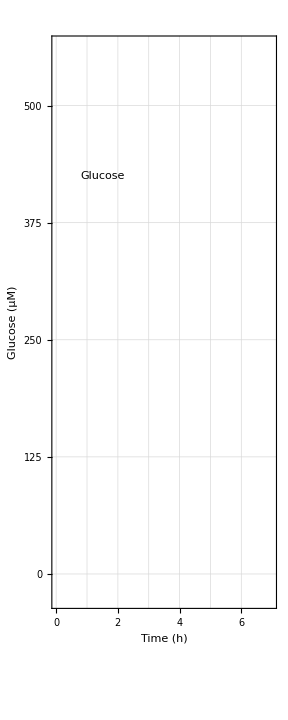
Show[-Graphics-,Plot[(Substrate[KpneumoniaepH,t] 40)/so,{t,0,timeGrowthCease[KpneumoniaepH,sMin]+0.25},AxesOrigin→{0,0}],-Graphics-,Plot[{BmassKpAlone[ReferencepH,t],BmassKpAlone[ReferencepH,t]},{t,0,timeGrowingAloneCurveEnd[ReferencepH]},PlotStyle→{{glc,Dashing[{0.015,0.02}],Thickness[0.01]},{txc,Dashing[{0.015,0.02}],Thickness[0.0025]}},PlotRange→{{0,xRange},{-2,45}}],Plot[{BmassKpAlone[KpneumoniaepH,t],BmassKpAlone[KpneumoniaepH,t]},{t,0,timeGrowingAloneCurveEnd[KpneumoniaepH]},PlotStyle→{{glc,Dashing[{0.015,0.02}],Thickness[0.01]},{txc,Dashing[{0.015,0.02}],Thickness[0.0025]}},PlotRange→{{0,xRange},{-2,45}}],Background→None]

```mathematica
GluAndKpvsRefCGR=
Show[Graphics[{
Text["Glucose", {1.5, 34}]}],glucose, KpvsRefCGR, RKPAlone, KpAlone, Background->None]
```

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","KpvsRKPCGR_45_c.eps"}], GluAndKpvsRefCGR, "EPS", ImageSize->236])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/KpvsRKPCGR_45_c.eps

```mathematica
growthCurveThickness=0.0125;
growthCurveLabelXCordinate=5.55;
deltaNGR=2;
KpneumoniaevsRefGR=
Table[
Show[Graphics[{
Text["Ref", {growthCurveLabelXCordinate, BiomassRef[pH, timeGrowthCease[pH, sMin]]+RefGthCurveYLabelOffset[pH, 2.5]}, TextStyle->{FontFamily->"Helvetica", FontSize->12}],
Text["pH "<>ToString[pH], {growthCurveLabelXCordinate, Biomass[pH, timeGrowthCease[pH, sMin]]-GthCurveYLabelOffset[pH, 2.5]},TextStyle->{FontFamily->"Helvetica", FontSize->12}],
Thickness[growthCurveThickness],RefGrowthCurveColoredbyGrowthRate2D[pH, deltaNGR],
GrowthCurveColoredbyGrowthRate2D[pH, deltaNGR]
}]], {pH, 4, 9, 0.5}]
```

Table::iterb: Iterator {t,0,0.25+$Failed,(0.25+$Failed)/Ceiling[5. (0.25+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Export["~/Documents/Research/Growth Model/~Niche Plot/MMA 5/KpneumoniaevsRef/Colored by Growth Rate/KpneumoniaevsRefGR_"<>ToString[40+(i-1)*5]<>".eps", KpneumoniaevsRefGR[[i]], "EPSTIFF"], {i, 1, Length[KpneumoniaevsRefGR]}];
```

Export::noelem: {EPSTIFF} is not a valid set of export elements for the EPS format.

General::stop: Further output of Export::noelem will be suppressed during this calculation.

```mathematica
KpneumoniaepH=3.9;
growthCurveLabelXCordinate=5.5;
deltaNSGR=2;
KpvsRefCSGR=
Show[Graphics[{
Text["Ref", {growthCurveLabelXCordinate, BiomassRef[KpneumoniaepH, timeGrowthCease[KpneumoniaepH, sMin]]+RefGthCurveYLabelOffset[KpneumoniaepH, 2.5]}, TextStyle->{FontFamily->"Helvetica", FontWeight->"Bold", FontSize->14}],
Text["pH "<>ToString[KpneumoniaepH], {growthCurveLabelXCordinate, Biomass[KpneumoniaepH, timeGrowthCease[KpneumoniaepH, sMin]]-GthCurveYLabelOffset[KpneumoniaepH, 2.5]},TextStyle->{FontFamily->"Helvetica", FontWeight->"Bold", FontSize->14}],
Thickness[growthCurveThickness],
RefGrowthCurveColoredbySpGrowthRate2D[KpneumoniaepH, deltaNSGR],GrowthCurveColoredbySpGrowthRate2D[KpneumoniaepH, deltaNSGR]
}]]
```

Table::iterb: Iterator {t,0,0.25+$Failed,(0.25+$Failed)/Ceiling[5. (0.25+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","KpneumoniaevsRefSGR_39.eps"}], KpvsRefCSGR, "EPS"])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/KpneumoniaevsRefSGR_39.eps

```mathematica
deltaNSGR=2;
growthCurveLabelXCordinate=5.5;
KpneumoniaevsRefSGR=
Table[
Show[Graphics[{
Text["Ref", {growthCurveLabelXCordinate, BiomassRef[pH, timeGrowthCease[pH, sMin]]+RefGthCurveYLabelOffset[pH, 2.5]}, TextStyle->{FontFamily->"Helvetica", FontWeight->"Bold", FontSize->14}],
Text["pH "<>ToString[pH], {growthCurveLabelXCordinate, Biomass[pH, timeGrowthCease[pH, sMin]]-GthCurveYLabelOffset[pH, 2.5]},TextStyle->{FontFamily->"Helvetica", FontWeight->"Bold", FontSize->14}],
Thickness[growthCurveThickness],
RefGrowthCurveColoredbySpGrowthRate2D[pH, deltaNSGR],GrowthCurveColoredbySpGrowthRate2D[pH, deltaNSGR]
}]], {pH, 4, 9, 0.5}]
```

Table::iterb: Iterator {t,0,0.25+$Failed,(0.25+$Failed)/Ceiling[5. (0.25+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Export["~/Documents/Research/Growth Model/~Niche Plot/MMA 5/KpneumoniaevsRef/Colored by Sp Growth Rate/KpneumoniaevsRefSGR_"<>ToString[40+(i-1)*5]<>".eps", KpneumoniaevsRefSGR[[i]], "EPSTIFF"], {i, 1, Length[KpneumoniaevsRefGR]}];
```

Export::noelem: {EPSTIFF} is not a valid set of export elements for the EPS format.

General::stop: Further output of Export::noelem will be suppressed during this calculation.

### Comparison of Reproductive Power (Print) (12/4/11~1/12/2012)

At near neutral pHs, growth curve labels are overlapping.  Need to write a routine to generate the Y-axis position to prevent label overlap.

```mathematica
GthCurveYLabelOffset[mediapH_?NumericQ, centerOffset_?NumericQ]:=

Module[{center, CenterDistance, Yoffset},

center= Biomass[growthRateGblMaxpH, timeGrowthCease[growthRateGblMaxpH, sMin]];
CenterDistance=center-Biomass[mediapH, timeGrowthCease[mediapH, sMin]];

Yoffset=
Which[
CenterDistance≤centerOffset, centerOffset-CenterDistance,
CenterDistance>centerOffset, 0
];

Return[Yoffset]
];

GthCurveYLabelOffset::usage="GthCurveYLabelOffset[mediapH, centerOffset] gives the minimum offset needed for the label of growth curves in the competitive situation between K. pheumoniae and Reference.  K. pheumoniae is growing at pH and the Reference is growing at optimum pH.  mediapH is the pH of the growth media.  centerOffset is the minimum Y offset for the label.";
```

```mathematica
RefGthCurveYLabelOffset[mediapH_?NumericQ, centerOffset_?NumericQ]:=

Module[{center, CenterDistance, Yoffset},

center= BiomassRef[growthRateGblMaxpH, timeGrowthCease[growthRateGblMaxpH, sMin]];
CenterDistance=BiomassRef[mediapH, timeGrowthCease[mediapH, sMin]]-center;

Yoffset=
Which[
CenterDistance≤centerOffset, centerOffset-CenterDistance,
CenterDistance>centerOffset, 0
];

Return[Yoffset]
];

RefGthCurveYLabelOffset::usage="RefGthCurveYLabelOffset[mediapH, centerOffset] gives the minimum offset needed for the label of reference growth curves in the competitive situation between K. pheumoniae and Reference.  K. pheumoniae is growing at pH and the Reference is growing at optimum pH.  mediapH is the pH of the growth media.  centerOffset is the minimum Y offset for the label.";
```

```mathematica
xRange=7;
SetOptions[Plot,
FrameLabel->{"Time (h)","Glucose (µM)", "","Biomass (mg/l)"},
FrameStyle->{Thickness[0.008],fmc},
FrameTicks->{Automatic, {{0, 0}, {10, 125}, {20, 250}, {30, 375}, {40, 500}}, None, {{0, 0}, {10, 10}, {20, 20}, {30, 30}, {40, 40}}},
GridLines->{Table[{x,{Thickness[0.003]}}, {x, 0,  xRange-1}],Table[{y,{Thickness[0.003]}}, {y, 0, 40, 10}]},PlotRange->{{0,xRange},{-2,45}},
PlotStyle->{Thickness[0.01], glc}
];
```

```mathematica
KpneumoniaepH=4.5;glucose=Plot[Substrate[KpneumoniaepH, t]/so*40, {t, 0,timeGrowthCease[KpneumoniaepH, sMin]+0.25}, AxesOrigin->{0, 0}]
```

Plot::plln: Limiting value 0.25+$Failed in {t,0,0.25+$Failed} is not a machine-sized real number.

Plot[(Substrate[KpneumoniaepH,t] 40)/so,{t,0,timeGrowthCease[KpneumoniaepH,sMin]+0.25},AxesOrigin→{0,0}]

```mathematica
KpAlone45=Plot[BmassKpAlone[KpneumoniaepH, t], {t, 0, timeGrowingAloneCurveEnd[KpneumoniaepH]}, PlotStyle->{Dashing[{0.007, 0.02}], Thickness[0.004]},PlotRange->{{0,xRange}, {-2, 45}}]
```

Plot::plln: Limiting value 0.375+$Failed in {t,0,0.375+$Failed} is not a machine-sized real number.

Plot[BmassKpAlone[KpneumoniaepH,t],{t,0,timeGrowingAloneCurveEnd[KpneumoniaepH]},PlotStyle→{Dashing[{0.007,0.02}],Thickness[0.004]},PlotRange→{{0,xRange},{-2,45}}]

```mathematica
RKPAlone=Plot[BmassKpAlone[ReferencepH, t], {t, 0, timeGrowingAloneCurveEnd[ReferencepH]}, PlotStyle->{Dashing[{0.007, 0.02}], Thickness[0.004]},PlotRange->{{0,xRange}, {-2, 45}}]
```

Plot::plln: Limiting value 0.375+$Failed in {t,0,0.375+$Failed} is not a machine-sized real number.

Plot[BmassKpAlone[ReferencepH,t],{t,0,timeGrowingAloneCurveEnd[ReferencepH]},PlotStyle→{Dashing[{0.007,0.02}],Thickness[0.004]},PlotRange→{{0,xRange},{-2,45}}]

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","RKPAlone_d.eps"}], RKPAlone, "EPS"])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/RKPAlone_d.eps

```mathematica
SetOptions[Graphics,
FrameLabel->{"Time (h)","Glucose (µM)", "","Biomass (mg/l)"},
FrameStyle->{Thickness[0.008],fmc},
FrameTicks->{Automatic, {{0, 0}, {10, 125}, {20, 250}, {30, 375}, {40, 500}}, None, {{0, 0}, {10, 10}, {20, 20}, {30, 30}, {40, 40}}},
GridLines->{Table[{x,{Thickness[0.003]}}, {x, 0,  xRange-1}]∪{{CompBegin[KpneumoniaepH], {D1,Thickness[0.003]}}(*, {CompEnd[KpneumoniaepH], {D1,Thickness[0.003]}}*)},Table[{y,{Thickness[0.003]}}, {y, 0, 40, 10}]},PlotRange->{{0,xRange},{-2,45}}
];
```

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

```mathematica
growthCurveLabelXCordinate=5.5;
growthCurveThickness=0.0125;
KpvsRefCGR=
Show[Graphics[{
Text["RKP", {growthCurveLabelXCordinate, BiomassRef[KpneumoniaepH, timeGrowthCease[KpneumoniaepH, sMin]]+GthCurveYLabelOffset[KpneumoniaepH, 2.5]}(*, TextStyle->{FontFamily->"Helvetica", FontSize->12}*)],
Text["pH "<>ToString[KpneumoniaepH], {growthCurveLabelXCordinate, Biomass[KpneumoniaepH, timeGrowthCease[KpneumoniaepH, sMin]]-GthCurveYLabelOffset[KpneumoniaepH, 2.5]}(*,TextStyle->{FontFamily->"Helvetica", FontSize->12}*)],
Thickness[growthCurveThickness],RefGrowthCurveColoredbyGrowthRate2D[KpneumoniaepH, 1.5],
GrowthCurveColoredbyGrowthRate2D[KpneumoniaepH, 2]
}]]
```

Table::iterb: Iterator {t,0,0.25+$Failed,(0.25+$Failed)/Ceiling[5. (0.25+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics-

```mathematica
GluAndKpvsRefCGR=
Show[Graphics[{
Text["Glucose", {1.5, 34}]}],glucose, KpvsRefCGR, RKPAlone, KpAlone45]
```

Show::gcomb: Could not combine the graphics objects in Show[,«3»,Plot[BmassKpAlone[KpneumoniaepH,t],{t,0,timeGrowingAloneCurveEnd[KpneumoniaepH]},PlotStyle→{Dashing[{0.007,0.02}],Thickness[0.004]},PlotRange→{{0,xRange},{-2,45}}]].

Show[-Graphics-,Plot[(Substrate[KpneumoniaepH,t] 40)/so,{t,0,timeGrowthCease[KpneumoniaepH,sMin]+0.25},AxesOrigin→{0,0}],-Graphics-,Plot[BmassKpAlone[ReferencepH,t],{t,0,timeGrowingAloneCurveEnd[ReferencepH]},PlotStyle→{Dashing[{0.007,0.02}],Thickness[0.004]},PlotRange→{{0,xRange},{-2,45}}],Plot[BmassKpAlone[KpneumoniaepH,t],{t,0,timeGrowingAloneCurveEnd[KpneumoniaepH]},PlotStyle→{Dashing[{0.007,0.02}],Thickness[0.004]},PlotRange→{{0,xRange},{-2,45}}]]

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","KpvsRKPCGR_45d.eps"}], GluAndKpvsRefCGR, "EPS", ImageSize->234])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/KpvsRKPCGR_45d.eps

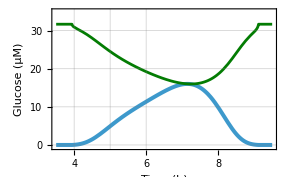

```mathematica
maxGrowthRateComp=Plot[{growthRateMax[pH], growthRateMaxRef[pH]}, {pH, 3.5, 9.5}, Frame->True,PlotRange->{{3.5, 9.5}, {-0.5, 35}}]
```

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","KpvsRKPMaxGrowthRateComp.eps"}], maxGrowthRateComp, "EPS"])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/KpvsRKPMaxGrowthRateComp.eps

```mathematica
growthCurveThickness=0.0125;
growthCurveLabelXCordinate=5.5;
deltaNGR=2;
KpneumoniaevsRefGR=
Table[
Show[Graphics[{
Text["Ref", {growthCurveLabelXCordinate, BiomassRef[pH, timeGrowthCease[pH, sMin]]+RefGthCurveYLabelOffset[pH, 2.5]}, TextStyle->{FontFamily->"Helvetica", FontSize->12}],
Text["pH "<>ToString[pH], {growthCurveLabelXCordinate, Biomass[pH, timeGrowthCease[pH, sMin]]-GthCurveYLabelOffset[pH, 2.5]},TextStyle->{FontFamily->"Helvetica", FontSize->12}],
Thickness[growthCurveThickness],RefGrowthCurveColoredbyGrowthRate2D[pH, deltaNGR],
GrowthCurveColoredbyGrowthRate2D[pH, deltaNGR]
}]], {pH, 4, 9, 0.5}]
```

Table::iterb: Iterator {t,0,0.25+$Failed,(0.25+$Failed)/Ceiling[5. (0.25+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Export["~/Documents/Research/Growth Model/~Niche Plot/MMA 5/KpneumoniaevsRef/Colored by Growth Rate/KpneumoniaevsRefGR_"<>ToString[40+(i-1)*5]<>".eps", KpneumoniaevsRefGR[[i]], "EPSTIFF"], {i, 1, Length[KpneumoniaevsRefGR]}];
```

Export::noelem: {EPSTIFF} is not a valid set of export elements for the EPS format.

General::stop: Further output of Export::noelem will be suppressed during this calculation.

```mathematica
KpneumoniaepH=3.9;
growthCurveLabelXCordinate=5.5;
deltaNSGR=2;
KpvsRefCSGR=
Show[Graphics[{
Text["Ref", {growthCurveLabelXCordinate, BiomassRef[KpneumoniaepH, timeGrowthCease[KpneumoniaepH, sMin]]+RefGthCurveYLabelOffset[KpneumoniaepH, 2.5]}, TextStyle->{FontFamily->"Helvetica", FontSize->12}],
Text["pH "<>ToString[KpneumoniaepH], {growthCurveLabelXCordinate, Biomass[KpneumoniaepH, timeGrowthCease[KpneumoniaepH, sMin]]-GthCurveYLabelOffset[KpneumoniaepH, 2.5]},TextStyle->{FontFamily->"Helvetica", FontSize->12}],
Thickness[growthCurveThickness],
RefGrowthCurveColoredbySpGrowthRate2D[KpneumoniaepH, deltaNSGR],GrowthCurveColoredbySpGrowthRate2D[KpneumoniaepH, deltaNSGR]
}]]
```

Table::iterb: Iterator {t,0,0.25+$Failed,(0.25+$Failed)/Ceiling[5. (0.25+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","KpneumoniaevsRefSGR_39.eps"}], KpvsRefCSGR, "EPS"])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/KpneumoniaevsRefSGR_39.eps

```mathematica
deltaNSGR=2;
growthCurveLabelXCordinate=5.5;
KpneumoniaevsRefSGR=
Table[
Show[Graphics[{
Text["Ref", {growthCurveLabelXCordinate, BiomassRef[pH, timeGrowthCease[pH, sMin]]+RefGthCurveYLabelOffset[pH, 2.5]}, TextStyle->{FontFamily->"Helvetica", FontSize->12}],
Text["pH "<>ToString[pH], {growthCurveLabelXCordinate, Biomass[pH, timeGrowthCease[pH, sMin]]-GthCurveYLabelOffset[pH, 2.5]},TextStyle->{FontFamily->"Helvetica", FontSize->12}],
Thickness[growthCurveThickness],
RefGrowthCurveColoredbySpGrowthRate2D[pH, deltaNSGR],GrowthCurveColoredbySpGrowthRate2D[pH, deltaNSGR]
}]], {pH, 4, 9, 0.5}]
```

Table::iterb: Iterator {t,0,0.25+$Failed,(0.25+$Failed)/Ceiling[5. (0.25+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Export["~/Documents/Research/Growth Model/~Niche Plot/MMA 5/KpneumoniaevsRef/Colored by Sp Growth Rate/KpneumoniaevsRefSGR_"<>ToString[40+(i-1)*5]<>".eps", KpneumoniaevsRefSGR[[i]], "EPSTIFF"], {i, 1, Length[KpneumoniaevsRefGR]}];
```

Export::noelem: {EPSTIFF} is not a valid set of export elements for the EPS format.

General::stop: Further output of Export::noelem will be suppressed during this calculation.

### Comparison by the Numbers (1/18/2012)

This section intends to find out how RKP affects the performance of K. pneumoniae at different pHs.

#### Determine When Competition Begins (1/22 ~ 2/3/12)

Here I use the population density reached by RKP at the end of growth, when K.pneumoniae is growing exactly the same as RKP, as the reference to determine when competition begins at other pHs.  This population density is called RKPRefSz.  RKP can rise pass RKPRefSz because K.pneumoniae grows slower than RKP and there are still unused glucose left in the media as RKP reaches RKPRefSz.  competitionBegin determine when RKP reaches RKPRefSz at each designated pH.  The partition of glucose between RKP and K.pneumoniae from now on determines the outcome.

```mathematica
Clear[competitionBegin];
competitionBegin[pH_]:=
Module[{Tmax, solution, MRef, M, s, time, BmLevel,beginTime},
Tmax= 10;
BmLevel=BiomassRef[ReferencepH, timeGrowthCease[ReferencepH, sMin]];
solution=
NDSolve[
{MRef'[time]==MRef[time]×μ[ReferencepH,s[time]],M'[time]==M[time]×μ[pH,s[time]],
s'[time]==-MRef'[time]/Yield[ReferencepH]-M'[time]/Yield[pH],
MRef[0]==(so/2)×Yield[ReferencepH]/BMmultiplication,M[0]==(so/2)× Yield[pH]/BMmultiplication ,
s[0]==so},
{MRef,M,s},{time,0,Tmax}, 
Method -> {"EventLocator", "Event" -> (MRef[time]-BmLevel)}
];

beginTime=
InterpolatingFunctionDomain[
M/.solution[[1]]
][[1, 2]];

If[NumberQ[beginTime], Return[beginTime], $Failed]
];
competitionBegin::usage="competitionBegin[pH] gives the time when RKP biomass concentration rises to BmLevel and competition begins.  BmLevel is RKP's final biomass concentration with K. pneumoniae growing exactly the same as RKP.  pH is media pH.";
```

RKP's final biomass level with K. pneumoniae growing at ReferencepH is a constant.  It is defined as RKPFinalBmatRefPH.

```mathematica
RKPFinalBmatRefPH=BiomassRef[ReferencepH, timeGrowthCease[ReferencepH, sMin]]
```

$Failed

Time competition begin at pH 6 is calculated as:

```mathematica
competitionBegin[6]
```

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

$Failed

NDSolve::nbnum1: The function value 0.38801-$Failed is not True or False when the arguments are {0.00031411,0.38801,0.0657229,499.998,0.371803,0.0045839,-5.14133}.

NDSolve::nbnum1: The function value 0.388127-$Failed is not True or False when the arguments are {0.00062822,0.388127,0.0657244,499.997,0.371914,0.004584,-5.14278}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

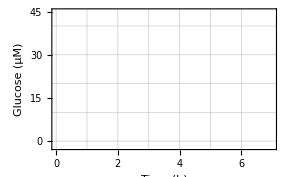

```mathematica
Plot[competitionBegin[pH], {pH, 4, 9}]
```

#### pH 7

At Reference pH 7.1749, growth takes almost 4.2 h to complete.

```mathematica
timeGrowthCease[ReferencepH, sMin]
```

$Failed

Only marginally slower at pH 7.

```mathematica
timeGrowthCease[7, sMin]
```

$Failed

The competition end when all the glucose is comsumed.

```mathematica
KpneumoniaepH=7;
CompEnd[pH]=timeGrowthCease[KpneumoniaepH, sMin]
```

$Failed

```mathematica
competitionBegin[7]
```

NDSolve::nbnum1: The function value 0.387991-$Failed is not True or False when the arguments are {0.000264271,0.387991,0.390359,499.997,0.371785,0.372688,-9.56723}.

NDSolve::nbnum1: The function value 0.38809-$Failed is not True or False when the arguments are {0.000528542,0.38809,0.390457,499.995,0.371879,0.372783,-9.56965}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

$Failed

```mathematica
BiomassRef[ReferencepH, competitionBegin[ReferencepH]]
```

NDSolve::nbnum1: The function value 0.387991-$Failed is not True or False when the arguments are {0.000264077,0.387991,0.387991,499.997,0.371785,0.371785,-9.58472}.

NDSolve::nbnum1: The function value 0.38809-$Failed is not True or False when the arguments are {0.000528154,0.38809,0.38809,499.995,0.371879,0.371879,-9.58714}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

$Failed

The percentage of biomass RKP produces in the final hour.

```mathematica
timeGrowingAloneCease[ReferencepH, sMin]
```

$Failed

```mathematica
BmassKpAlone[ReferencepH, timeGrowingAloneCease[ReferencepH, sMin]]
```

$Failed

```mathematica
BmassKpAlone[ReferencepH, timeGrowingAloneCease[ReferencepH, sMin]-1]
```

$Failed

```mathematica
(BmassKpAlone[ReferencepH, timeGrowingAloneCease[ReferencepH, sMin]]-BmassKpAlone[ReferencepH, timeGrowingAloneCease[ReferencepH, sMin]-1])/BmassKpAlone[ReferencepH, timeGrowingAloneCease[ReferencepH, sMin]]
```

0

RKP produces 60% of the total biomass in the final hour!

#### pH 6

With both population growing together tracking closely how each will grow on its own, competition do not affect the course of the process but rather when it ends.  RKP affects K. pneumoniae by grabbing the unused glucose left in the media when the process is supposed to end if K. pneumoniae is growing equally.  I will define the moment when RKP rises to the level if K. pneumoniae is growing equally and the process is supposed to end as the start of the competition.  The partition of glucose from now on until the end determines the final outcome.

Red vertical line marks the time when RKP reaches the final level if K. pneumoniae is growing equally.  This line marks the beginning of competition.

The second red line marks the end of the competition as all the glucose is gone.

At pH 6, the competition begins at 4.12 h and end at 4.36 h for a total of 0.24 h.

```mathematica
KpneumoniaepH=6;
CompBegin[KpneumoniaepH]
CompEnd[KpneumoniaepH]
CompeteTime[KpneumoniaepH]
CompeteTime[KpneumoniaepH]*60
```

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

$Failed

$Failed

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

```mathematica
Plot[BiomassRef[pH, competitionBegin[pH]], {pH, 4, 9}]
```

NDSolve::nbnum1: The function value 0.38801-$Failed is not True or False when the arguments are {0.00031411,0.38801,0.0657229,499.998,0.371803,0.0045839,-5.14133}.

NDSolve::nbnum1: The function value 0.388127-$Failed is not True or False when the arguments are {0.00062822,0.388127,0.0657244,499.997,0.371914,0.004584,-5.14278}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

-Graphics-

It appears that the routine competitionBegin is not quite as accurate.  I might need to work on it in the future to improve it accuracy.

The amount of glucose that will be redistributed among the two due to the slow growth of K. pneumoniae is GluRedistribution

```mathematica
GluRedistribution[KpneumoniaepH]
GluRedistributionPercent[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

The average population size of RKP and K. pneumoniae during the competition period and their percentage of the total.

```mathematica
RKPAvgCompBiomass[KpneumoniaepH]
KpAvgCompBiomass[KpneumoniaepH]
RKPAvgCompBiomassPercent[KpneumoniaepH]
KpAvgCompBiomassPercent[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

$Failed

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

$Failed

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

50

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

50

Biomass production by RKP and K. pneumoniae during the competition period and its percentage of total biomass production during this period.

```mathematica
RKPBiomassProduction[KpneumoniaepH]
KpBiomassProduction[KpneumoniaepH]
RKPBiomassProductionPercent[KpneumoniaepH]
KpBiomassProductionPercent[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

The average growth rate (AGR) and normalized AGR during the glucose redistribution period.  AGR is normalized as a fraction of RKP's local maximum growth rate.

```mathematica
RKPAvgGrowthRate[KpneumoniaepH]
KpAvgGrowthRate[KpneumoniaepH]
NormRKPAvgGrowthRate[KpneumoniaepH]
NormKpAvgGrowthRate[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

I am surprised at how low the NormRKPAvgGrowthRate and NormKpAvgGrowthRate are.  I thought they should be 95 vs 60 and not 87 vs 51.  Let me plot it out and see the detail.

LocalNmGrowthRate[pH_?NumericQ, t_?NumericQ]:=growthRate[pH, t]/growthRateMaxRef[pH];
LocalNmGrowthRateRef[pH_?NumericQ, t_?NumericQ]:=growthRateRef[pH, t]/growthRateMaxRef[pH];

```mathematica
Plot[{LocalNmGrowthRate[KpneumoniaepH,t],LocalNmGrowthRateRef[KpneumoniaepH, t]},{t, CompBegin[KpneumoniaepH], CompEnd[KpneumoniaepH]+0.03},Frame->True,FrameLabel->{"Time (h)", "Growth Rate (%)"},FrameTicks->Automatic,GridLines->{Automatic,Range[0, 0.8, 0.2]},PlotStyle->{{D3, Thickness[0.01]}, {D1, Thickness[0.01]}},PlotRange->{{Floor[10*CompBegin[KpneumoniaepH]]/10, Ceiling[10*CompEnd[KpneumoniaepH]]/10}, {-0.025, 1.025}},TextStyle->{FontSize->12}]
```

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Plot::optx: Unknown option TextStyle→{FontSize→12} in Plot[{LocalNmGrowthRate[KpneumoniaepH,t],LocalNmGrowthRateRef[KpneumoniaepH,t]},{t,CompBegin[KpneumoniaepH],CompEnd[KpneumoniaepH]+0.03},Frame→True,«4»,PlotRange→{{1/10 Floor[10 CompBegin[«1»]],1/10 Ceiling[10 CompEnd[«1»]]},{-0.025,1.025}},TextStyle→{FontSize→12}].

Plot[{LocalNmGrowthRate[KpneumoniaepH,t],LocalNmGrowthRateRef[KpneumoniaepH,t]},{t,CompBegin[KpneumoniaepH],CompEnd[KpneumoniaepH]+0.03},Frame→True,FrameLabel→{Time (h),Growth Rate (%)},FrameTicks→Automatic,GridLines→{Automatic,Range[0,0.8,0.2]},PlotStyle→{{D3,Thickness[0.01]},{D1,Thickness[0.01]}},PlotRange→{{1/10 Floor[10 CompBegin[KpneumoniaepH]],1/10 Ceiling[10 CompEnd[KpneumoniaepH]]},{-0.025,1.025}},TextStyle→{FontSize→12}]

Ok, the final period where growth slows down drags down the average growth rate.

Now, let's see the amount and percentage of glucose captured by both during the redistribution period.

```mathematica
RKPGluCapture[KpneumoniaepH]
KpGluCapture[KpneumoniaepH]
RKPGluCapturePercent[KpneumoniaepH]
KpGluCapturePercent[KpneumoniaepH]
RKPGluCapturePercent[KpneumoniaepH]+KpGluCapturePercent[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0.

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0.

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.387996-$Failed is not True or False when the arguments are {0.000277721,0.387996,0.383717,499.997,0.37179,0.329541,-9.08751}.

NDSolve::nbnum1: The function value 0.3881-$Failed is not True or False when the arguments are {0.000555442,0.3881,0.383809,499.995,0.371889,0.32962,-9.08981}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

#### pH 5

The initial NSGR is

```mathematica
Nμ[7, 500]
```

0.988445

```mathematica
Nμ[5, 500]
```

0.699879

```mathematica
Nμ[ReferencepH, 500]
```

0.992063

```mathematica
NYield[5]/NYield[7]
```

0.919772

```mathematica
NYield[7]
```

0.949538

```mathematica
NYield[6]
```

0.933395

```mathematica
NYield[6]/NYield[7]
```

0.983

```mathematica
NYield[5]
```

0.873358

```mathematica
NYield[5]/NYield[7]
```

0.919772

```mathematica
KpneumoniaepH=5;
CompBegin[KpneumoniaepH]
CompEnd[KpneumoniaepH]
CompeteTime[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

$Failed

$Failed

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

```mathematica
GluRedistribution[KpneumoniaepH]
GluRedistributionPercent[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

```mathematica
RKPAvgCompBiomass[KpneumoniaepH]
KpAvgCompBiomass[KpneumoniaepH]
RKPAvgCompBiomassPercent[KpneumoniaepH]
KpAvgCompBiomassPercent[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

$Failed

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

$Failed

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

50

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

50

```mathematica
RKPBiomassProduction[KpneumoniaepH]
KpBiomassProduction[KpneumoniaepH]
RKPBiomassProductionPercent[KpneumoniaepH]
KpBiomassProductionPercent[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
RKPGluCapture[KpneumoniaepH]
KpGluCapture[KpneumoniaepH]
RKPGluCapturePercent[KpneumoniaepH]
KpGluCapturePercent[KpneumoniaepH]
RKPGluCapturePercent[KpneumoniaepH]+KpGluCapturePercent[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0.

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0.

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
RKPAvgGrowthRate[KpneumoniaepH]
KpAvgGrowthRate[KpneumoniaepH]
NormRKPAvgGrowthRate[KpneumoniaepH]
NormKpAvgGrowthRate[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
Plot[{LocalNmGrowthRate[KpneumoniaepH,t],LocalNmGrowthRateRef[KpneumoniaepH, t]},{t, CompBegin[KpneumoniaepH], CompEnd[KpneumoniaepH]+0.03},Frame->True,FrameLabel->{"Time (h)", "Growth Rate (%)"},FrameTicks->Automatic,GridLines->{Automatic,Range[0, 0.8, 0.2]},PlotStyle->{{D3, Thickness[0.01]}, {D1, Thickness[0.01]}},PlotRange->{{Floor[10*CompBegin[KpneumoniaepH]]/10, Ceiling[10*CompEnd[KpneumoniaepH]]/10}, {-0.025, 1.025}},TextStyle->{FontSize->12}]
```

NDSolve::nbnum1: The function value 0.388004-$Failed is not True or False when the arguments are {0.000298744,0.388004,0.359023,499.998,0.371797,0.242703,-8.17325}.

NDSolve::nbnum1: The function value 0.388115-$Failed is not True or False when the arguments are {0.000597489,0.388115,0.359095,499.995,0.371904,0.242752,-8.1753}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Plot::optx: Unknown option TextStyle→{FontSize→12} in Plot[{LocalNmGrowthRate[KpneumoniaepH,t],LocalNmGrowthRateRef[KpneumoniaepH,t]},{t,CompBegin[KpneumoniaepH],CompEnd[KpneumoniaepH]+0.03},Frame→True,«4»,PlotRange→{{1/10 Floor[10 CompBegin[«1»]],1/10 Ceiling[10 CompEnd[«1»]]},{-0.025,1.025}},TextStyle→{FontSize→12}].

Plot[{LocalNmGrowthRate[KpneumoniaepH,t],LocalNmGrowthRateRef[KpneumoniaepH,t]},{t,CompBegin[KpneumoniaepH],CompEnd[KpneumoniaepH]+0.03},Frame→True,FrameLabel→{Time (h),Growth Rate (%)},FrameTicks→Automatic,GridLines→{Automatic,Range[0,0.8,0.2]},PlotStyle→{{D3,Thickness[0.01]},{D1,Thickness[0.01]}},PlotRange→{{1/10 Floor[10 CompBegin[KpneumoniaepH]],1/10 Ceiling[10 CompEnd[KpneumoniaepH]]},{-0.025,1.025}},TextStyle→{FontSize→12}]

#### pH 4.5

```mathematica
Nμ[5, 500]
```

0.699879

```mathematica
Nμ[4.5, 500]
```

0.487474

```mathematica
NYield[5]/NYield[7]
```

0.919772

```mathematica
NYield[5]
```

0.873358

```mathematica
NYield[4.5]
```

0.681074

```mathematica
KpneumoniaepH=4.5;
CompBegin[KpneumoniaepH]
CompEnd[KpneumoniaepH]
CompeteTime[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

$Failed

$Failed

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

```mathematica
GluRedistribution[KpneumoniaepH]
GluRedistributionPercent[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

```mathematica
RKPAvgCompBiomass[KpneumoniaepH]
KpAvgCompBiomass[KpneumoniaepH]
RKPAvgCompBiomassPercent[KpneumoniaepH]
KpAvgCompBiomassPercent[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

$Failed

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

$Failed

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

50

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

50

```mathematica
RKPBiomassProduction[KpneumoniaepH]
KpBiomassProduction[KpneumoniaepH]
RKPBiomassProductionPercent[KpneumoniaepH]
KpBiomassProductionPercent[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
RKPGluCapture[KpneumoniaepH]
KpGluCapture[KpneumoniaepH]
RKPGluCapturePercent[KpneumoniaepH]
KpGluCapturePercent[KpneumoniaepH]
RKPGluCapturePercent[KpneumoniaepH]+KpGluCapturePercent[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0.

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

0.

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
RKPAvgGrowthRate[KpneumoniaepH]
KpAvgGrowthRate[KpneumoniaepH]
NormRKPAvgGrowthRate[KpneumoniaepH]
NormKpAvgGrowthRate[KpneumoniaepH]
```

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
Plot[{LocalNmGrowthRate[KpneumoniaepH,t],LocalNmGrowthRateRef[KpneumoniaepH, t]},{t, CompBegin[KpneumoniaepH], CompEnd[KpneumoniaepH]+0.03},Frame->True,FrameLabel->{"Time (h)", "Growth Rate (%)"},FrameTicks->Automatic,GridLines->{Automatic,Range[0, 0.8, 0.2]},PlotStyle->{{D3, Thickness[0.01]}, {D1, Thickness[0.01]}},PlotRange->{{Floor[10*CompBegin[KpneumoniaepH]]/10, Ceiling[10*CompEnd[KpneumoniaepH]]/10}, {-0.025, 1.025}},TextStyle->{FontSize->12}]
```

NDSolve::nbnum1: The function value 0.388009-$Failed is not True or False when the arguments are {0.000311332,0.388009,0.279963,499.998,0.371802,0.13182,-7.14716}.

NDSolve::nbnum1: The function value 0.388125-$Failed is not True or False when the arguments are {0.000622663,0.388125,0.280004,499.996,0.371912,0.131839,-7.14894}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

Plot::optx: Unknown option TextStyle→{FontSize→12} in Plot[{LocalNmGrowthRate[KpneumoniaepH,t],LocalNmGrowthRateRef[KpneumoniaepH,t]},{t,CompBegin[KpneumoniaepH],CompEnd[KpneumoniaepH]+0.03},Frame→True,«4»,PlotRange→{{1/10 Floor[10 CompBegin[«1»]],1/10 Ceiling[10 CompEnd[«1»]]},{-0.025,1.025}},TextStyle→{FontSize→12}].

Plot[{LocalNmGrowthRate[KpneumoniaepH,t],LocalNmGrowthRateRef[KpneumoniaepH,t]},{t,CompBegin[KpneumoniaepH],CompEnd[KpneumoniaepH]+0.03},Frame→True,FrameLabel→{Time (h),Growth Rate (%)},FrameTicks→Automatic,GridLines→{Automatic,Range[0,0.8,0.2]},PlotStyle→{{D3,Thickness[0.01]},{D1,Thickness[0.01]}},PlotRange→{{1/10 Floor[10 CompBegin[KpneumoniaepH]],1/10 Ceiling[10 CompEnd[KpneumoniaepH]]},{-0.025,1.025}},TextStyle→{FontSize→12}]

Biomass production at pH 4.5 as a percentage of itself at pH 7.

```mathematica
mo=(so/2)×Yield[ReferencepH]/BMmultiplication
```

0.387893

```mathematica
Biomass[4.5, CompEnd[4.5]]-mo
```

-0.387893+$Failed

```mathematica
Biomass[7, CompEnd[7]]-mo
```

-0.387893+$Failed

```mathematica
100*(Biomass[4.5, CompEnd[4.5]]-mo)/(Biomass[7, CompEnd[7]]-mo)
```

100

Biomass production collapsed by almost 84% at pH 4.5.

## 3D Plot of Growth vs pH

### Model Setup

#### Function for Generating Growth Curve

```mathematica
Clear[initialPointsPerCurve];
initialPointsPerCurve[pH_]:=Ceiling[timeGrowthCurveEnd[pH]/0.2];

Clear[anchorPoints];anchorPoints[pH_]:=Table[{pH, t, Biomass[pH, t]}, {t, 0, timeGrowthCurveEnd[pH], timeGrowthCurveEnd[pH]/initialPointsPerCurve[pH]}
];
```

```mathematica
Clear[initialPointsPerCurveNew];
initialPointsPerCurveNew[pH_, timeStart_, timeEnd_]:=Ceiling[(timeEnd-timeStart)/0.2];

Clear[anchorPointsNew];
anchorPointsNew[pH_, timeStart_, timeEnd_]:=Table[{pH, t, Biomass[pH, t]}, {t, timeStart,timeEnd, (timeEnd-timeStart)/initialPointsPerCurveNew[pH, timeStart, timeEnd]}
];
```

```mathematica
Clear[curveSmoothing3D];
curveSmoothing3D[anchorPoints_,curvaturelimit_?NumberQ]:=Module[{smoothEnd,endPointsPair1,endPointsPair2,insertPoint1,insertPoint2,anchorPointsNew},smoothEnd=1;
anchorPointsNew=anchorPoints;
While[smoothEnd<(Length[anchorPointsNew]-1),(*check between line segments to see if they are within curvaturelimit*){While[smoothEnd<(Length[anchorPointsNew]-1)&&angleBetweenTwoVectors@@PointsToVector@@Take[anchorPointsNew,{smoothEnd,smoothEnd+2}]<curvaturelimit,smoothEnd++];
(*smoothEnd=Length[anchorpointsNew]-1->CurveChecking complete;smoothEnd<Length[anchorpointsNew]-1->Add points to reduce the bending of the curve;*)If[smoothEnd<(Length[anchorPointsNew]-1),{endPointsPair1=Take[anchorPointsNew,{smoothEnd,smoothEnd+1}];
endPointsPair2=Take[anchorPointsNew,{smoothEnd+1,smoothEnd+2}];
insertPoint1=Plus@@endPointsPair1/Length[endPointsPair1]/.{v1_,v2_,_}:>{v1,v2,Biomass[v1,v2]};
insertPoint2=Plus@@endPointsPair2/Length[endPointsPair2]/.{v1_,v2_,_}:>{v1,v2,Biomass[v1,v2]};
anchorPointsNew=Insert[anchorPointsNew,insertPoint1,smoothEnd+1];
anchorPointsNew=Insert[anchorPointsNew,insertPoint2,smoothEnd+3]}] (*finished adding two points*)}]; (*Finished smoothing the curve*)Return[anchorPointsNew]]
curveSmoothing::usage="curveSmoothing3D[pointList, curvature] take a list of points,pointList, in 3D space in the form of {{x, y, f(x, y)}, ..., etc} and check the angle between successive line segments.  If the angle, in degrees, between successive line segments exceeds curvature limit, two points will be inserted in the middle of the two line segment.  The process will repeat itself until angles between all successive line segments are within curvature limit and curveSmoothing return the new pointList.";
```

```mathematica
Clear[GblNmGrowthRateSmoothing3D];GblNmGrowthRateSmoothing3D[anchorPoints_?ListQ,deltaNGrowthRate_?NumberQ]:=

Module[{smoothEnd,endPointsPair,insertPoint,anchorPointsNew},

smoothEnd=1;
anchorPointsNew=anchorPoints;

While[smoothEnd≤(Length[anchorPointsNew]-1),

(*check between point pair to see if they are within deltaNGrowthRate Limit*){While[smoothEnd≤(Length[anchorPointsNew]-1)&&Abs[(GblNmGrowthRate[#[[1]],#[[2]]]&)[anchorPointsNew[[smoothEnd+1]]]-
(GblNmGrowthRate[#[[1]],#[[2]]]&)[anchorPointsNew[[smoothEnd]]]]*100<deltaNGrowthRate,smoothEnd++];

(*smoothEnd > Length[anchorpointsNew]-1 -> CurveChecking complete;smoothEnd ≤ Length[anchorpointsNew]-1 -> Add points to smooth color gradient;*)
If[smoothEnd≤(Length[anchorPointsNew]-1),
{endPointsPair=Take[anchorPointsNew,{smoothEnd,smoothEnd+1}];
insertPoint=Plus@@endPointsPair/Length[endPointsPair]/.{v1_,v2_,_}:>{v1,v2,Biomass[v1,v2]};
anchorPointsNew=Insert[anchorPointsNew,insertPoint,smoothEnd+1]}
] (*finished adding point*)

}]; (*Finished smoothing the curve*)
Return[anchorPointsNew]]

GblNmGrowthRateSmoothing3D::usage="GblNmGrowthRateSmoothing3D[pointList, deltaNGrowthRate] take a list of points, pointList, in 3D space in the form of {{pH, t, Biomass(pH, t)}, ..., etc} and check the deltaNGrowthRate between successive points.  Growth rate is normalized against global maximum of K pneumoniae.  If the deltaNGrowthRate, in percent, between successive points exceeds deltaNGrowthRate, a point will be inserted in the middle of two points.  The process will repeat itself until deltaNGrowthRate between all successive points are within deltaNGrowthRate and GblNmGrowthRateSmoothing3D return the new pointList.";
```

```mathematica
Clear[NSpGthRtSmoothing3D];
NSpGthRtSmoothing3D[anchorPoints_?ListQ,deltaNSpGthRt_?NumberQ]:=

Module[{smoothEnd,endPointsPair,insertPoint,anchorPointsNew},

smoothEnd=1;
anchorPointsNew=anchorPoints;

While[smoothEnd≤(Length[anchorPointsNew]-1),

(*check between point pair to see if they are within deltaNSpGthRt Limit*){While[smoothEnd≤(Length[anchorPointsNew]-1)&&Abs[(Nμ[#[[1]],Substrate[#[[1]],#[[2]]]]&)[anchorPointsNew[[smoothEnd+1]]]-
(Nμ[#[[1]],Substrate[#[[1]],#[[2]]]]&)[anchorPointsNew[[smoothEnd]]]]*100<deltaNSpGthRt,smoothEnd++];

(*smoothEnd > Length[anchorpointsNew]-1 -> CurveChecking complete;smoothEnd ≤ Length[anchorpointsNew]-1 -> Add points to smooth color gradient;*)
If[smoothEnd≤(Length[anchorPointsNew]-1),
{endPointsPair=Take[anchorPointsNew,{smoothEnd,smoothEnd+1}];
insertPoint=Plus@@endPointsPair/Length[endPointsPair]/.{v1_,v2_,_}:>{v1,v2,Biomass[v1,v2]};
anchorPointsNew=Insert[anchorPointsNew,insertPoint,smoothEnd+1]}
] (*finished adding point*)

}]; (*Finished smoothing the curve*)
Return[anchorPointsNew]]

NSpGthRtSmoothing3D::usage="NSpGthRtSmoothing3D[pointList, deltaNSpGthRt] take a list of points, pointList, in 3D space in the form of {{x, y, f(x, y)}, ..., etc} and check the difference in specific growth rate between successive points.  If the difference, in percent, between successive points exceeds deltaNSpGthRt, a point will be inserted in the middle of two points.  The process will repeat itself until the difference between all successive points are within deltaNSpGthRt and NSpGthRtSmoothing3D return the new pointList.";
```

```mathematica
Clear[timeGrowthCease];
timeGrowthCease[pH_, sMin_]:=
Module[{Tmax, solution, MRef, M, s, time, endTime},
Tmax= 10;
solution=
NDSolve[
{MRef'[time]==MRef[time]×μ[ReferencepH,s[time]],M'[time]==M[time]×μ[pH,s[time]],
s'[time]==-MRef'[time]/Yield[ReferencepH]-M'[time]/Yield[pH],
MRef[0]==(so/2)×Yield[ReferencepH]/BMmultiplication,M[0]==(so/2)×Yield[pH]/BMmultiplication ,
s[0]==so},
{MRef,M,s},{time,0,Tmax}, 
Method -> {"EventLocator", "Event" -> (s[time]-sMin)}
];

endTime=
InterpolatingFunctionDomain[
M/.solution[[1]]
][[1, 2]];

If[NumberQ[endTime], Return[endTime], $Failed]
];
timeGrowthCease::usage="timeGrowthCease[pH, sMin] gives the time when substrate concentration drops to sMin and the process stops.  pH is media pH.";
```

```mathematica
Clear[timeGrowthCeaseAnchorPoints, timeGrowthCeaseIFunction, timeGrowthCurveEnd];
timeGrowthCeaseAnchorPoints=
Table[{pH,timeGrowthCease[pH, sMin]}, {pH, SGRpHLowBnd, SGRpHHighBnd, 0.1}];
timeGrowthCeaseIFunction=
Interpolation[timeGrowthCeaseAnchorPoints];
timeGrowthCurveEnd[pH_]:=timeGrowthCeaseIFunction[pH]+0.5;
```

#### Growth Curve Function

```mathematica
Clear[GrowthCurveColoredbyGrowthRate];
GrowthCurveColoredbyGrowthRate[pH_?NumberQ, curvatureLimit_?NumberQ, deltaNGrowthRate_?NumberQ]:=
Module[{GrowthCurve, PointList},
PointList=curveSmoothing3D[anchorPoints[pH], curvatureLimit];
PointList=GblNmGrowthRateSmoothing3D[PointList, deltaNGrowthRate];
GrowthCurve=
Table[
{ratecolor[Abs[GblNmGrowthRate@@
Drop[(Plus@@#/Length[#])&[
Take[PointList, {i, i+1}]], -1]
]],
Line[Take[PointList, {i, i+1}]]},
{i, 1, Length[PointList]-1}
];
Return[GrowthCurve]
];
```

```mathematica
Clear[GrowthCurveColoredbyGrowthRateVThickness2];
GrowthCurveColoredbyGrowthRateVThickness2[pH_?NumberQ, curvatureLimit_?NumberQ, deltaNGrowthRate_?NumberQ, timeStart_:0., timeEnd_:Tmax,iThickness_:0.001, fThickness_:0.006]:=
Module[{GrowthCurve, PointList},
PointList=curveSmoothing3D[anchorPointsNew[pH, timeStart, timeEnd], curvatureLimit];
PointList=GblNmGrowthRateSmoothing3D[PointList, deltaNGrowthRate];
GrowthCurve=
Table[
{ratecolor[Abs[GblNmGrowthRate@@
Drop[(Plus@@#/Length[#])&[
Take[PointList, {i, i+1}]], -1]
]],
Thickness[iThickness+(fThickness-iThickness)*((Biomass[ pH, PointList[[i+1, 2]]]-Biomass[ pH, PointList[[2, 2]]])/(Biomass[pH, timeGrowthCurveEnd[pH]]-Biomass[ pH, PointList[[2, 2]]]))
],
Line[Take[PointList, {i, i+1}]]},
{i, 1, Length[PointList]-1}
];
Return[GrowthCurve]
];
GrowthCurveColoredbyGrowthRateVThickness2::usage="The thickness of the growth curves is proportional to the percentage of biomass produced relative to the final biomass that will be attained.";
```

```mathematica
Clear[GrowthCurveColoredbySpecificGrowthRate];
GrowthCurveColoredbySpecificGrowthRate[pH_?NumberQ, curvatureLimit_?NumberQ, deltaNSpGthRt_?NumberQ]:=
Module[{GrowthCurve, PointList},
PointList=curveSmoothing3D[anchorPoints[pH], curvatureLimit];
PointList=NSpGthRtSmoothing3D[PointList, deltaNSpGthRt];
GrowthCurve=
Table[{
ratecolor[Abs[
Nμ[pH, Substrate[pH, PointList[[i, 2]]]]
]],
Line[Take[PointList, {i, i+1}]]},
{i, 1, Length[PointList]-1}
];
Return[GrowthCurve]
];
GrowthCurveColoredbySpecificGrowthRate::usage="GrowthCurveColoredbySpecificGrowthRate[pH, curvatureLimit, deltaNSpGthRt] gives 3D graphics primitives describing growth of Klebsiella pheumoniae at pH.  The color of the curve is proportional to normalized Specific growth rate.  curvaturelimit define the maximun angle in degrees between successive line segments.  deltaNSpGthRt define the maximum difference in percent between successive line segments.";
```

```mathematica
Clear[GrowthCurveColoredbySpecificGrowthRateVThickness];
GrowthCurveColoredbySpecificGrowthRateVThickness[pH_?NumberQ, curvatureLimit_?NumberQ, deltaNSpGthRt_?NumberQ, timeStart_:0., timeEnd_:Tmax,iThickness_:0.001, fThickness_:0.006]:=
Module[{GrowthCurve, PointList},
PointList=curveSmoothing3D[anchorPointsNew[pH, timeStart, timeEnd], curvatureLimit];
PointList=NSpGthRtSmoothing3D[PointList, deltaNSpGthRt];
GrowthCurve=
Table[{
ratecolor[Abs[
Nμ[pH, Substrate[pH, PointList[[i, 2]]]]
]],
Thickness[iThickness+(fThickness-iThickness)*((Biomass[ pH, PointList[[i+1, 2]]]-Biomass[ pH, PointList[[2, 2]]])/(Biomass[pH, timeGrowthCurveEnd[pH]]-Biomass[ pH, PointList[[2, 2]]]))
],
Line[Take[PointList, {i, i+1}]]},
{i, 1, Length[PointList]-1}
];
Return[GrowthCurve]
];
GrowthCurveColoredbySpecificGrowthRateVThickness::usage="GrowthCurveColoredbySpecificGrowthRateVThickness[pH, curvatureLimit, deltaNSpGthRt, timeStart, timeEnd,iThickness, fThickness] gives 3D graphics primitives describing growth of Klebsiella pheumoniae at pH from timeStart to timeEnd.  The color of the curve is proportional to normalized Specific growth rate.  curvaturelimit define the maximun angle in degrees between successive line segments.  deltaNSpGthRt define the maximum difference in percent between successive line segments.  The thickness of the growth curves varies from iThickness to fThickness and the variation is proportional to the percentage of biomass produced relative to the final biomass that will be attained.";
```

#### Partial Derivative of Biomass

```mathematica
Clear[Biomass2DItp, DBiomass2DItpVSpH, normalVector, unitNormalVector];
Biomass2DItp=
Interpolation[
Flatten[
Table[{pH, t, Biomass[pH, t]}, {t, 0, Tmax, 5/100},{pH, 4, 9, 1/10}
], 1
]
];

DBiomass2DItpVSpH[pH_, t_]:=Evaluate[D[Biomass2DItp[pH, t], pH]];

normalVector[pH_, t_]:=Cross[{1, 0, DBiomass2DItpVSpH[pH, t]}, {0, 1, growthRate[pH, t]}]

unitNormalVector[pH_, t_]:=normalVector[pH, t]/vectorLength[normalVector[pH, t]]
```

#### Virtual Gridline

```mathematica
Clear[cartesian3DVPCoordinate];
cartesian3DVPCoordinate[VP_List, plotRange_List, boxRatios_List]:=
Module[{BoxOrigin, xyzRange, BoxCenter, VPCartesianCoordinate},
BoxOrigin={plotRange[[1, 1]], plotRange[[2, 1]], plotRange[[3, 1]]};
xyzRange={plotRange[[1, 2]]-plotRange[[1, 1]], plotRange[[2, 2]]-plotRange[[2, 1]], plotRange[[3, 2]]-plotRange[[3, 1]]};
BoxCenter=xyzRange/2.+BoxOrigin;
VPCartesianCoordinate=VP*xyzRange/boxRatios+BoxCenter;
Return[VPCartesianCoordinate];
];
cartesian3DVPCoordinate::usage="cartesian3DVPCoordinate gives the Cartesian Coordinate of the 3D ViewPoint.  VP is the ViewPoint coordinate as in the 3D ViewPoint selector.  plotRange gives the x, y, z range of plot in the form of: {{xmin, xmax}, {ymin, ymax}, {zmin, zmax}}.  boxRatios gives the ratios of side lengths for the bounding box of the three-dimensional picture as specified in the option BoxRatios.  The function can be used inside Graphics3D command, first use SetOptions[Graphics3D, BoxRatios->..., PlotRange->..., ViewPoint->...] to setup the options for the plot.  Then enter the function as cartesian3DVPCoordinate[ViewPoint, PlotRange, BoxRatios]/.Options[Graphics3D]";
```

```mathematica
Clear[biomassViewPointShift];biomassViewPointShift[pH_?NumberQ, t_?NumberQ, normalLift_?NumberQ, viewPointShift_?NumberQ, viewPoint_List, plotRange_List, boxRatios_List]:=
Module[{normalVector, unitNormalVector, vecPn, vecPv, vecPnv, unitVecPnv},

normalVector:=Cross[{1, 0, DBiomass2DItpVSpH[pH, t]}, {0, 1, growthRate[pH, t]}];
unitNormalVector:=normalVector/Sqrt[Plus@@(normalVector^2)];
vecPn=normalLift* unitNormalVector;
vecPv=cartesian3DVPCoordinate[viewPoint, plotRange, boxRatios]-{pH, t, Biomass[pH, t]};
vecPnv= vectorProjection[vecPn, vecPv];
unitVecPnv=vecPnv/Sqrt[Plus@@(vecPnv^2)];
Return[viewPointShift*unitVecPnv+{pH, t, Biomass[pH, t]}]
];
biomassViewPointShift::usage="biomassViewPointShift[pH, t, normalLift, viewPointShift, viewPoint, plotRange, boxRatios] gives the 3D coordinate of the point, {pH, t, Biomass[pH, t]}, shifted a distance of viewPointShift toward the 3D ViewPoint.";
```

```mathematica
(* This routine still got unfixed bugs;
Clear[apparentDiameter];apparentDiameter[location_List, lineDirection_List,normalVector_List, diameter_Real]:=
Module[{ viewPoint3D, vecViewPoint, vecAxis, unitDiameter, unitDiameterAxisProj, unitDiameterParallel, angleNormalVecViewPointVec, aprntDiameter},

viewPoint3D=cartesian3DVPCoordinate[ViewPoint, PlotRange, BoxRatios]/.Options[Graphics3D];
vecViewPoint=(viewPoint3D-location)/vectorLength[viewPoint3D-location];
vecAxis=normalVector×vecViewPoint;
unitDiameter=lineDirection×normalVector/vectorLength[lineDirection×normalVector];
unitDiameterAxisProj= vectorProjection[unitDiameter, vecAxis];
unitDiameterParallel=unitDiameter-unitDiameterAxisProj;
angleNormalVecViewPointVec=angleBetweenTwoVectors[vecViewPoint, normalVector];

aprntDiameter=
Which[
angleNormalVecViewPointVec>0&&angleNormalVecViewPointVec<90, vectorLength[unitDiameterAxisProj+unitDiameterParallel*Sin[90-angleNormalVecViewPointVec Degree]],
angleNormalVecViewPointVec==0.,  1.,
angleNormalVecViewPointVec==90., vectorLength[unitDiameterAxisProj],
angleNormalVecViewPointVec>90., 0.
];

Return[diameter*aprntDiameter];
];
apparentDiameter::usage="apparentDiameter[location, lineDirection,normalVector, diameter] gives apparent diameter of a line going through location on 3D surface.  normalVector is the normal vector of the 3D surface at location.  lineDirection is the vector that gives the direction of the line at location on the surface.";
*)
```

```mathematica
Clear[virtualTimeGridline];
virtualTimeGridline[t_?NumberQ, lineThickness_Real, gridLineColor_RGBColor, nlift_?NumberQ, vpShift_?NumberQ]:=
Module[{anchorPoints, vpShiftAnchorPoints, dpH, TGridline},
dpH=1/10 (* gives smooth transition *);
anchorPoints=Table[{pH, t, Biomass[pH, t]}, {pH, 4, 9, dpH}];
vpShiftAnchorPoints=Table[biomassViewPointShift[pH, t, nlift, vpShift, ViewPoint, PlotRange, BoxRatios]/.Options[Graphics3D], {pH, 4, 9, dpH}];
TGridline=
Table[{
Thickness[lineThickness
(*apparentDiameter[anchorPoints[[i]], anchorPoints[[i+1]]-anchorPoints[[i]], unitNormalVector[4+(i-1)*dpH,t],lineThickness]*)
],
Line[Take[vpShiftAnchorPoints, {i, i+1}]]
},{i, 1, Length[vpShiftAnchorPoints]-1}
];
Return[Prepend[TGridline, gridLineColor]];
]
```

```mathematica
Clear[virtualpHGridline];
virtualpHGridline[pH_?NumberQ, curvatureLimit_?NumberQ, lineThickness_Real, gridlineColor_RGBColor, nlift_?NumberQ, vpShift_?NumberQ, vpAffinity_?NumberQ]:=

Module[
{initialPointsPerCurve, tPlotEnd, anchorPoints, smoothanchorPoints, vpShiftAnchorPoints, hyperbola, time, pHGridline},

tPlotEnd=(PlotRange/.Options[Graphics3D])[[2, 2]];
initialPointsPerCurve=Ceiling[tPlotEnd/0.2];
anchorPoints=
Table[{pH, t, Biomass[pH, t]}, {t, 0, tPlotEnd, tPlotEnd/initialPointsPerCurve}];
smoothanchorPoints=curveSmoothing3D[anchorPoints, curvatureLimit];

hyperbola[time_]:=vpShift*time/(vpAffinity+time);

vpShiftAnchorPoints=
Table[
If[smoothanchorPoints[[i, 2]]<vpShift, biomassViewPointShift[pH, smoothanchorPoints[[i, 2]], nlift, hyperbola[smoothanchorPoints[[i, 2]]], ViewPoint, PlotRange, BoxRatios],
biomassViewPointShift[pH, smoothanchorPoints[[i, 2]], nlift, vpShift, ViewPoint, PlotRange, BoxRatios]
],{i, 1, Length[smoothanchorPoints]}]/.Options[Graphics3D];

pHGridline=
Table[{
Thickness[lineThickness
(*apparentDiameter[smoothanchorPoints[[i]], smoothanchorPoints[[i+1]]-smoothanchorPoints[[i]], unitNormalVector[pH,smoothanchorPoints[[i, 2]]],lineThickness]*)
],
Line[Take[vpShiftAnchorPoints, {i, i+1}]]
},{i, 1, Length[vpShiftAnchorPoints]-1}
];
Return[Prepend[pHGridline, gridlineColor]];
];

virtualpHGridline::usage="virtualpHGridline[pH, curvatureLimit, lineThickness, gridlineColor, nlift, vpShift, vpAffinity] projects each point of the original pH gridline toward 3D view point of the plot and therefore generates virtual pH gridlines that looks exactly the same as the original under the specific 3D viewpoint setting.  

Variables supplied to the routine are:
pH -> pH at which gridline is to be drawn.
curvatureLimit -> maximum curvature in degrees between successive line segments.
lineThickness -> Thickness of the line to be drawn.
gridlineColor -> color of the gridline to be drawn.
nlift -> amount of vertical lift away from the 3D surface.  Can be set as 1 in most instances.
vpShift -> amount to shift toward 3D view point.  This is normally a small real number from fraction of 1 to maybe 10 depending on the range of plot.
vpAffinity -> normally close to 1/4 of vpShift.  By varying vpAffinity up or down, pH gridline can be properly displayed as t approaches zero.

When adjusting vpShift and vpAffinity, First adjust vpShift so that pH gridline looks good on most area except where t closes to zero.  Once vpShift is determined, then adjust vpAffinity so the entire pH gridline can be displayed properly.";
```

```mathematica
On[General::spell, General::spell1];
```

### Growth vs pH (Presentation) (6/12/2012)

Here we look at the overall picture of growth of K pneumoniae vs pH, growth rate is normalized against global maximum of itself.

To run this section, need to initialize:
1. Color Scheme
2. 3D Graphics Options
3. Growth Model Setup with The Casheing Method
4. Growth Rate, Maximum Growth Rate, Normalized Growth Rate
5. Vector Algebra
6. Function for Generating Growth Curve
7. Growth Curve Function
8. Partial Derivative of Biomass
9. Virtual Gridline

```mathematica
curvatureLimit=10 (*Degree*);
deltaNGrowthRate=1.5 (*percent*);
deltaNSpGthRt=2.5 (*percent*);
growthCurveThickness= 0.005;
gridlineThickness=0.003;
growthCurveSpaceing=1/40 (*pH*);

GrowthvspHColoredbyGR=
Graphics3D[{Thickness[growthCurveThickness],
Table[GrowthCurveColoredbyGrowthRate[pH, curvatureLimit, deltaNGrowthRate], {pH, 4, 6, growthCurveSpaceing}],
Table[GrowthCurveColoredbyGrowthRate[pH, curvatureLimit, deltaNGrowthRate], {pH, 6, 9, growthCurveSpaceing/2}]
}
]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[GrowthvspHColoredbyGR]
```

-Graphics3D-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","GrowthvspHColoredbyGR25F_2.eps"}], GrowthvspHColoredbyGR, "EPS"])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/GrowthvspHColoredbyGR25F_2.eps

```mathematica
curvatureLimit=10 (*Degree*);
deltaNGrowthRate=2.5 (*percent*);
deltaNSpGthRt=2.5 (*percent*);
growthCurveThickness= 0.005;
gridlineThickness=0.003;
growthCurveSpaceing=1/40 (*pH*);

GrowthvspHColoredbySGR=
Graphics3D[{Thickness[growthCurveThickness],
Table[GrowthCurveColoredbySpecificGrowthRate[pH, curvatureLimit, deltaNSpGthRt], {pH, 4, 6, growthCurveSpaceing}],
Table[GrowthCurveColoredbySpecificGrowthRate[pH, curvatureLimit, deltaNSpGthRt], {pH, 6, 9, growthCurveSpaceing/2}]
}
]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[GrowthvspHColoredbySGR]
```

-Graphics3D-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","GrowthvspHColoredbySGR25.eps"}], GrowthvspHColoredbySGR, "EPS"])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/GrowthvspHColoredbySGR25.eps

```mathematica
Clear[virtualGridline];
virtualGridline=
Graphics3D[{
Table[
virtualTimeGridline[t, 0.003, glc, 2., 0.5],{t, 1/2, 6, 1/2}
], 
Table[
virtualpHGridline[pH, 5, 0.003, glc, 2, 0.75, 0.75/4], {pH, 4, 9, 1/2}]}, Background->None
];
```

```mathematica
Show[virtualGridline]
```

-Graphics3D-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","virtualGridline_4.eps"}], virtualGridline, "EPS"])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/virtualGridline_4.eps

```mathematica
Growth3DColoredbyGR=Show[{GrowthvspHColoredbyGR, virtualGridline}, Background->None]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","Niche Growth3DColoredbyGR.eps"}], Growth3DColoredbyGR, "EPS", ImageSize->158])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/Niche Growth3DColoredbyGR.eps

```mathematica
Growth3DColoredbySGR=Show[{GrowthvspHColoredbySGR, virtualGridline}, Background->None]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","Niche Growth3DColoredbySGR.eps"}], Growth3DColoredbySGR, "EPS", ImageSize->158])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/Niche Growth3DColoredbySGR.eps

Let me plot the left side of growth vs pH.  First, need to change the Graphics3D options.

```mathematica
curvatureLimit=10 (*Degree*);
deltaNGrowthRate=1.5 (*percent*);
growthCurveThickness= 0.005;
gridlineThickness=0.003;
growthCurveSpaceing=1/40 (*pH*);

(* Colored by Growth Rate *)
GrowthvspHColoredbyGRLeft =
Graphics3D[{
Thickness[growthCurveThickness],
Table[GrowthCurveColoredbyGrowthRate[pH, curvatureLimit, deltaNGrowthRate], {pH, 4, 7, growthCurveSpaceing/2}],
Table[GrowthCurveColoredbyGrowthRate[pH, curvatureLimit, deltaNGrowthRate], {pH, 7, 9, growthCurveSpaceing}]
}]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[GrowthvspHColoredbyGRLeft]
```

-Graphics3D-

```mathematica
curvatureLimit=10 (*Degree*);
deltaNSpGthRt=2.5 (*percent*);
growthCurveThickness= 0.005;
gridlineThickness=0.003;
growthCurveSpaceing=1/40 (*pH*);

(* Colored by Normalized μ *)
GrowthvspHColoredbySGRLeft=
Graphics3D[{Thickness[growthCurveThickness],
Table[GrowthCurveColoredbySpecificGrowthRate[pH, curvatureLimit, deltaNSpGthRt], {pH, 4, 7, growthCurveSpaceing/2}],
Table[GrowthCurveColoredbySpecificGrowthRate[pH, curvatureLimit, deltaNSpGthRt], {pH, 7, 9, growthCurveSpaceing}]
}]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[GrowthvspHColoredbySGRLeft]
```

-Graphics3D-

```mathematica
Clear[virtualGridline];
virtualGridlineL=
Graphics3D[{
Table[
virtualTimeGridline[t, 0.003, glc, 2., 0.5],{t, 1/2, 6, 1/2}
], 
Table[
virtualpHGridline[pH, 5, 0.003, glc, 2, 0.75, 0.75/4], {pH, 4, 9, 1/2}]}, Background->None
];
```

```mathematica
Show[virtualGridlineL]
```

-Graphics3D-

```mathematica
Growth3DLeftColoredbyGR=Show[{GrowthvspHColoredbyGRLeft, virtualGridlineL}, Background->None]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","Niche Growth3DLeftColoredbyGR.eps"}], Growth3DLeftColoredbyGR, "EPS", ImageSize->158])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/Niche Growth3DLeftColoredbyGR.eps

```mathematica
Growth3DLeftColoredbySGR=Show[{GrowthvspHColoredbySGRLeft, virtualGridlineL}, Background->None]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","Niche Growth3DLeftColoredbySGR.eps"}], Growth3DLeftColoredbySGR, "EPS", ImageSize->158])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/Niche Growth3DLeftColoredbySGR.eps

### Growth vs pH (Print) (4/14/2011)

Here we look at the overall picture of growth of K pneumoniae vs pH, growth rate is normalized against global maximum of itself.

To run this section, need to initialize:
1. Color Scheme
2. 3D Graphics Options
3. Growth Model Setup with The Casheing Method
4. Growth Rate, Maximum Growth Rate, Normalized Growth Rate
5. Vector Algebra
6. Function for Generating Growth Curve
7. Growth Curve Function
8. Partial Derivative of Biomass
9. Virtual Gridline

```mathematica
curvatureLimit=10 (*Degree*);
deltaNGrowthRate=1.5 (*percent*);
deltaNSpGthRt=2.5 (*percent*);
growthCurveThickness= 0.005;
gridlineThickness=0.003;
growthCurveSpaceing=1/40 (*pH*);

GrowthvspHColoredbyGR=
Graphics3D[{Thickness[growthCurveThickness],
Table[GrowthCurveColoredbyGrowthRate[pH, curvatureLimit, deltaNGrowthRate], {pH, 4, 6, growthCurveSpaceing}],
Table[GrowthCurveColoredbyGrowthRate[pH, curvatureLimit, deltaNGrowthRate], {pH, 6, 9, growthCurveSpaceing/2}]
}
]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[GrowthvspHColoredbyGR]
```

-Graphics3D-

```mathematica
curvatureLimit=10 (*Degree*);
deltaNGrowthRate=2.5 (*percent*);
deltaNSpGthRt=2.5 (*percent*);
growthCurveThickness= 0.005;
gridlineThickness=0.003;
growthCurveSpaceing=1/40 (*pH*);

GrowthvspHColoredbySGR=
Graphics3D[{Thickness[growthCurveThickness],
Table[GrowthCurveColoredbySpecificGrowthRate[pH, curvatureLimit, deltaNSpGthRt], {pH, 4, 6, growthCurveSpaceing}],
Table[GrowthCurveColoredbySpecificGrowthRate[pH, curvatureLimit, deltaNSpGthRt], {pH, 6, 9, growthCurveSpaceing/2}]
}
]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[GrowthvspHColoredbySGR]
```

-Graphics3D-

```mathematica
Clear[virtualGridline];
virtualGridline=
Graphics3D[{
Table[
virtualTimeGridline[t, 0.003, glc, 2., 0.5],{t, 1/2, 6, 1/2}
], 
Table[
virtualpHGridline[pH, 5, 0.003, glc, 2, 0.75, 0.75/4], {pH, 4, 9, 1/2}]}, Background->None
]
```

-Graphics3D-

```mathematica
Show[virtualGridline]
```

-Graphics3D-

```mathematica
Growth3DColoredbyGR=Show[{GrowthvspHColoredbyGR, virtualGridline}, Background->None]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
Export["/Users/chuckgwo/Documents/Research/Publications/Fundamental pH niche of K pneumonia/Niche Growth3DColoredbyGR.eps",Growth3DColoredbyGR, "EPSTIFF", ImageSize->158]
```

Export::nodir: Directory /Users/chuckgwo/Documents/Research/Publications/Fundamental pH niche of K pneumonia/ does not exist.

$Failed

```mathematica
Growth3DColoredbySGR=Show[{GrowthvspHColoredbySGR, virtualGridline}, Background->None]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","Niche Growth3DColoredbySGR.eps"}], Growth3DColoredbySGR, "EPS", ImageSize->158])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/Niche Growth3DColoredbySGR.eps

Let me plot the left side of growth vs pH.  First, need to change the Graphics3D options.

```mathematica
curvatureLimit=10 (*Degree*);
deltaNGrowthRate=1.5 (*percent*);
growthCurveThickness= 0.005;
gridlineThickness=0.003;
growthCurveSpaceing=1/40 (*pH*);

(* Colored by Growth Rate *)
GrowthvspHColoredbyGRLeft =
Graphics3D[{
Thickness[growthCurveThickness],
Table[GrowthCurveColoredbyGrowthRate[pH, curvatureLimit, deltaNGrowthRate], {pH, 4, 7, growthCurveSpaceing/2}],
Table[GrowthCurveColoredbyGrowthRate[pH, curvatureLimit, deltaNGrowthRate], {pH, 7, 9, growthCurveSpaceing}]
}]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[GrowthvspHColoredbyGRLeft]
```

-Graphics3D-

```mathematica
curvatureLimit=10 (*Degree*);
deltaNSpGthRt=2.5 (*percent*);
growthCurveThickness= 0.005;
gridlineThickness=0.003;
growthCurveSpaceing=1/40 (*pH*);

(* Colored by Normalized μ *)
GrowthvspHColoredbySGRLeft=
Graphics3D[{Thickness[growthCurveThickness],
Table[GrowthCurveColoredbySpecificGrowthRate[pH, curvatureLimit, deltaNSpGthRt], {pH, 4, 7, growthCurveSpaceing/2}],
Table[GrowthCurveColoredbySpecificGrowthRate[pH, curvatureLimit, deltaNSpGthRt], {pH, 7, 9, growthCurveSpaceing}]
}]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[GrowthvspHColoredbySGRLeft]
```

-Graphics3D-

```mathematica
Clear[virtualGridline];
virtualGridline=
Graphics3D[{
Table[
virtualTimeGridline[t, 0.003, glc, 2., 0.5],{t, 1/2, 6, 1/2}
], 
Table[
virtualpHGridline[pH, 5, 0.003, glc, 2, 0.75, 0.75/4], {pH, 4, 9, 1/2}]}, Background->None
];
```

```mathematica
Show[virtualGridline]
```

-Graphics3D-

```mathematica
Growth3DLeftColoredbyGR=Show[{GrowthvspHColoredbyGRLeft, virtualGridline}, Background->None]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","Niche Growth3DLeftColoredbyGR.eps"}], Growth3DLeftColoredbyGR, "EPS", ImageSize->150])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/Niche Growth3DLeftColoredbyGR.eps

```mathematica
Growth3DLeftColoredbySGR=Show[{GrowthvspHColoredbySGRLeft, virtualGridline}, Background->None]
```

Table::iterb: Iterator {t,0,0.5+$Failed,(0.5+$Failed)/Ceiling[5. (0.5+$Failed)]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

-Graphics3D-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","Niche Growth3DLeftColoredbySGR.eps"}], Growth3DLeftColoredbySGR, "EPS", ImageSize->150])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/Niche Growth3DLeftColoredbySGR.eps

### Plot3D

```mathematica
growth3DPlot=Plot3D[{Biomass[pH,t],ratecolor[Abs[GblNmGrowthRate[pH,t]]]},{pH,3.5,9.5},{t,0,10},AxesEdge->{{-1,-1},{1,-1},{1,1}},AxesLabel->{"pH","T(hr)",""},Background->bgc(*GrayLevel[1]*),BoxRatios->{1,1,0.8},BaseStyle->{FontFamily->"Helvetica",FontSize->14},Lighting->True,
Mesh->False,MeshStyle->Black,PlotPoints->{31,61},PlotRange->{{3.5,9.5},{0,5},{0,25}},Ticks->{Range[4, 9],Range[1, 5],Range[5, 25, 5]},ViewPoint->{1.730,-2.290,0.740}]
```

-Graphics3D-

```mathematica
growth3DPlot=Plot3D[{Biomass[pH,t],ratecolor[Abs[GblNmGrowthRate[pH,t]]]},{pH,3.5,9.5},{t,0,10},AxesEdge->{{-1,-1},{1,-1},{1,1}},AxesLabel->{"pH","T(hr)",""},Background->bgc(*GrayLevel[1]*),BoxRatios->{1,1,0.8},BaseStyle->{FontFamily->"Helvetica",FontSize->14},Lighting->True,
Mesh->False,MeshStyle->Black,PlotPoints->{121,121},PlotRange->{{3.5,9.5},{0,5},{0,25}},Ticks->{Range[4, 9],Range[1, 5],Range[5, 25, 5]},ViewPoint->{1.730,-2.290,0.740}]
```

-Graphics3D-

## Density Plot - Reproductive Potential of K. pneumonia

### Print (4/14/2011)

To run this section, initialize the Color Scheme, General Model Setup.

```mathematica
Clear[mGR95,mGR80,mGR60,mGR40,mGR20];
mGR95=95/100 growthRateGblMax;
mGR80=80/100growthRateGblMax;
mGR60=60/100 growthRateGblMax;
mGR40=40/100 growthRateGblMax;
mGR20=20/100 growthRateGblMax;
```

```mathematica
FrameTicks->{{4, 5, 6, 7, 8, 9}, Table[{i/100, i}, {i,0, 100, 20}], {}, Table[{i, PaddedForm[i, {1, 1},NumberPadding->{"","0"}]}, {i, 0, 1, 0.2}]}
```

FrameTicks→{{4,5,6,7,8,9},{{0,0},{1/5,20},{2/5,40},{3/5,60},{4/5,80},{1,100}},{},{{0.,0.0},{0.2,0.2},{0.4,0.4},{0.6,0.6},{0.8,0.8},{1.,1.0}}}

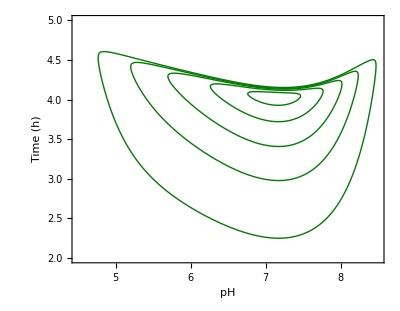

```mathematica
growthRateContour=ContourPlot[growthRate[pH,t],{pH,4.5,8.5},{t,2,5},AspectRatio->3.5/4.5,ContourStyle->glc,ContourShading->None,Contours->{mGR95,mGR80,mGR60,mGR40,mGR20},BaseStyle->{FontFamily->"Helvetica",FontSize->7},FrameLabel->{"pH","Time (h)"},FrameStyle->{Thickness[0.004], Black},PlotPoints->100]
```

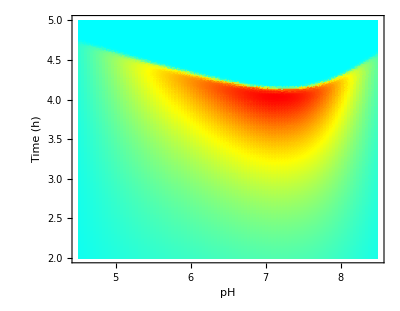

```mathematica
growthRateColorDensity=DensityPlot[growthRate[pH,t],{pH,4.5,8.5},{t,2,5},AspectRatio->3.5/4.5,ColorFunction->ratecolor,BaseStyle->{FontFamily->"Helvetica",FontSize->7},FrameLabel->{"pH","Time (h)"},FrameStyle->{Thickness[0.004], Black}, Mesh->False, PlotPoints->100]
```

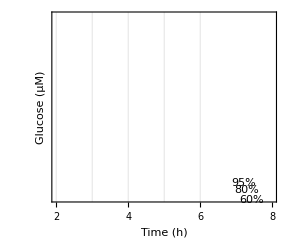

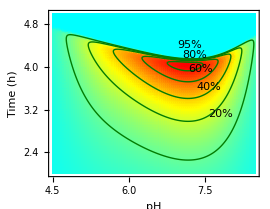

```mathematica
Clear[contourLabel];
contourLabel=
Graphics[
{Text["20%",{7.82,3.115},{0,0},{1, 1.5}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],
Text["40%",{7.575,3.625},{0,0},{1, 1.}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],
Text["60%",{7.415,3.96},{0,0},{1, 0.75}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],
Text["80%",{7.295,4.225},{0,0},{1, 0.45}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],
Text["95%",{7.2,4.41},{0,0},{1, 0.4}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}]}, PlotRange->{{2, 8}, {4, 9}}]
fitnessDensity=Show[{growthRateColorDensity,growthRateContour, contourLabel}, ImageSize->270]
```

```mathematica
Export["~/Documents/Research/Publications/Fundamental pH niche of K pneumonia/PopulationFitnessDensity_wRKPMMAv5.eps",fitnessDensity,"EPSTIFF",ImageSize->180]
```

Export::noelem: {EPSTIFF} is not a valid set of export elements for the EPS format.

$Failed

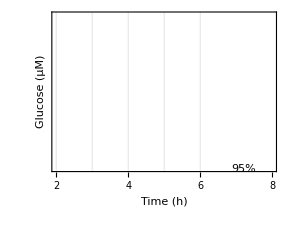

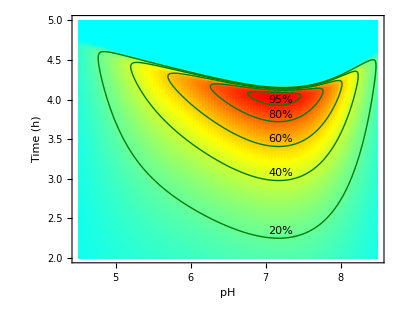

Export::nodir: Directory /Users/chuckgwo/Documents/Research/Publications/Fundamental pH niche of K pneumonia/ does not exist.

$Failed

```mathematica
Clear[contourLabel];
contourLabel=
Graphics[
{Text["20%",{7.2,2.34},{0,0},{1, 0}, TextStyle->{FontColor->Black, FontFamily->"Helvetica", FontSize->5}],
Text["40%",{7.2,3.07},{0,0},{1, 0}, TextStyle->{FontColor->Black, FontFamily->"Helvetica", FontSize->5}],
Text["60%",{7.2,3.5},{0,0},{1, 0}, TextStyle->{FontColor->Black, FontFamily->"Helvetica", FontSize->5}],
Text["80%",{7.2,3.8},{0,0},{1, 0}, TextStyle->{FontColor->Black, FontFamily->"Helvetica", FontSize->5}],
Text["95%",{7.2,4.0},{0,0},{1, 0}, TextStyle->{FontColor->Black, FontFamily->"Helvetica", FontSize->5}]}, PlotRange->{{2, 8}, {4, 9}}]
fitnessDensity=Show[{growthRateColorDensity,growthRateContour, contourLabel}]
Export["/Users/chuckgwo/Documents/Research/Publications/Fundamental pH niche of K pneumonia/PopulationFitnessDensity_wRKP.eps",fitnessDensity,"EPSTIFF",ImageSize->180]
```

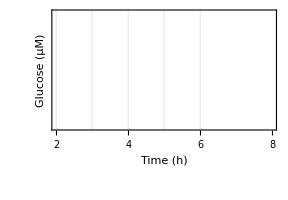

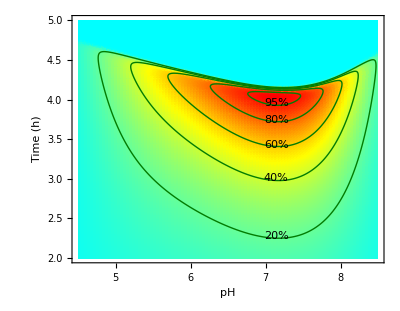

```mathematica
Clear[contourLabel];
contourLabel=
Graphics[
{Text["20%",{7.144,2.276},{0,0},{1, 0}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],
Text["40%",{7.144,3.006},{0,0},{1, 0}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],
Text["60%",{7.144,3.431},{0,0},{1, 0}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],
Text["80%",{7.144,3.741},{0,0},{1, 0}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],
Text["95%",{7.144,3.956},{0,0},{1, 0}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}]}, PlotRange->{{2, 8}, {4.5, 8.5}}]
fitnessDensity=Show[{growthRateColorDensity,growthRateContour, contourLabel}]
```

```mathematica
Export["/Users/chuckgwo/Documents/Research/Publications/Fundamental pH niche of K pneumonia/PopulationFitnessDensity_wRKP_C.eps",fitnessDensity,"EPSTIFF",ImageSize->135]
```

Export::nodir: Directory /Users/chuckgwo/Documents/Research/Publications/Fundamental pH niche of K pneumonia/ does not exist.

$Failed

```mathematica
Clear[sGR95,sGR90, sGR80,sGR60,sGR40,sGR20];
sGR95=95/100 μMax;
sGR90=90 /100μMax;
sGR80=80/100μMax;
sGR60=60/100 μMax;
sGR40=40/100 μMax;
sGR20=20/100 μMax;
```

```mathematica
SetOptions[
Graphics,Background->None (*None gives a transparent plot*), BaseStyle->{FontFamily->"Helvetica",FontSize->7},Frame->True,FrameLabel->{"pH","Time (h)"}];
```

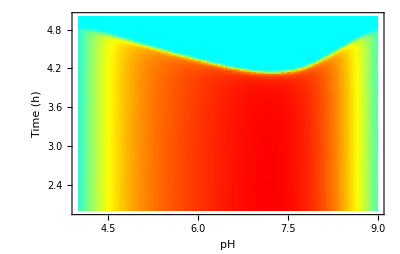

```mathematica
SpecificGrowthRateColorDensity=DensityPlot[μ[pH,Substrate[pH,t]],{pH,4,9},{t,2,5},AspectRatio->3.5/5.5,ColorFunction->ratecolor, BaseStyle->{FontFamily->"Helvetica",FontSize->7},FrameLabel->{"pH","Time (h)"},FrameStyle->{Thickness[0.004], Black}, Mesh->False,PlotPoints->100]
```

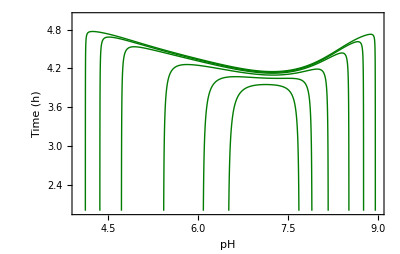

```mathematica
specificGrowthRateContour=ContourPlot[μ[pH,Substrate[pH,t]],{pH,4,9},{t,2,5},AspectRatio->3.5/5.5,ContourStyle->glc,ContourShading->None,Contours->{sGR95,sGR90,sGR80,sGR60,sGR40,sGR20},BaseStyle->{FontFamily->"Helvetica",FontSize->7},FrameLabel->{"pH","Time (h)"},FrameStyle->{Thickness[0.004], Black}, PlotPoints->100]
```

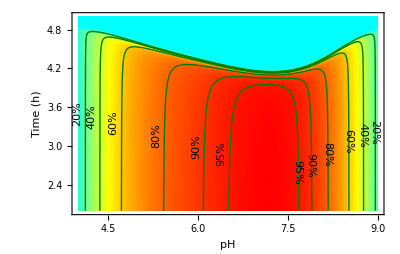

```mathematica
Clear[contourLabel, individualFitnessDensity, offset];
offset=-0.07;
contourLabel=
Graphics[
{Text["95%",{6.464+offset,2.89},{-1,0},{0,1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["95%",{7.660,2.597},{0,-1},{0,-1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["90%",{6.036+offset,2.99},{-1,0},{0,1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["90%",{7.879,2.697},{0,-1},{0,-1}, 
TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["80%",{5.37+offset,3.16},{-1,0},{0,1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["80%",{8.153,2.867},{0,-1},{0,-1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["60%",{4.657+offset,3.36},{-1,0},{0,1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["60%",{8.501,3.067},{0,-1},{0,-1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["40%",{4.295+offset,3.45},{-1,0},{0,1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["40%",{8.748,3.157},{0,-1},{0,-1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["20%",{4.055+offset,3.5},{-1,0},{0,1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["20%",{8.943,3.207},{0,-1},{0,-1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}]}, AspectRatio->1,PlotRange->{{3.9, 9.3}, {2.9, 8.1}}];
individualFitnessDensity=Show[{SpecificGrowthRateColorDensity, specificGrowthRateContour, contourLabel}]
```

```mathematica
Export["/Users/chuckgwo/Documents/Research/Publications/Fundamental pH niche of K pneumonia/individualFitnessDensity_wRKP.eps",individualFitnessDensity,"EPSTIFF",ImageSize->165]
```

Export::nodir: Directory /Users/chuckgwo/Documents/Research/Publications/Fundamental pH niche of K pneumonia/ does not exist.

$Failed

### Presentation (6/12/2012)

To run this section, initialize the Color Scheme, General Model Setup.

```mathematica
Clear[mGR95,mGR80,mGR60,mGR40,mGR20];
mGR95=95/100 growthRateGblMax;
mGR80=80/100growthRateGblMax;
mGR60=60/100 growthRateGblMax;
mGR40=40/100 growthRateGblMax;
mGR20=20/100 growthRateGblMax;
```

```mathematica
growthRateContour=ContourPlot[growthRate[pH,t],{pH,4.5,8.5},{t,2,5},AspectRatio->3/4,ContourStyle->glc,ContourShading->None,Contours->{mGR95,mGR80,mGR60,mGR40,mGR20},FrameLabel->{"pH","Time (h)"},PlotPoints->100];
```

```mathematica
Null
```

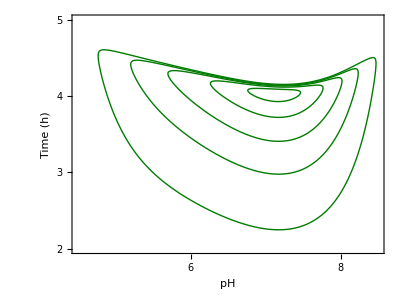

```mathematica
Show[growthRateContour, Background->None,BaseStyle->{FontFamily->"Helvetica",FontSize->9},FrameStyle->{Thickness[0.005]}, 
FrameTicks->{
(* x ticks *)Flatten[
Table[
Prepend[Table[{x+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {x, x, {0.012, 0}}
], {x, 4, 9}
], 1
], 
(* y ticks *)Flatten[
Table[
Prepend[Table[{y+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {y, y, {0.012, 0}}
], {y, 2,8}
], 1
]}
]
```

```mathematica
growthRateColorDensity=DensityPlot[growthRate[pH,t],{pH,4.5,8.5},{t,2,5},AspectRatio->3/4,ColorFunction->ratecolor,FrameLabel->{"pH","Time (h)"}, Mesh->False, PlotPoints->100];
```

```mathematica
Null
```

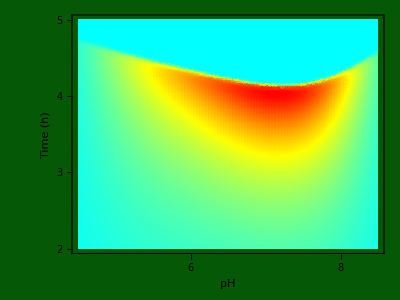

```mathematica
Show[growthRateColorDensity, Background->bgc,BaseStyle->{FontFamily->"Helvetica",FontSize->9},FrameStyle->{Thickness[0.005]}, 
FrameTicks->{
(* x ticks *)Flatten[
Table[
Prepend[Table[{x+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {x, x, {0.012, 0}}
], {x, 4, 9}
], 1
], 
(* y ticks *)Flatten[
Table[
Prepend[Table[{y+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {y, y, {0.012, 0}}
], {y, 2,8}
], 1
]}
]
```

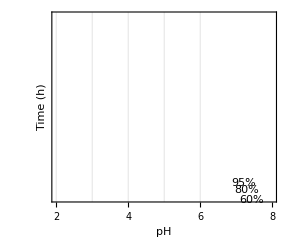

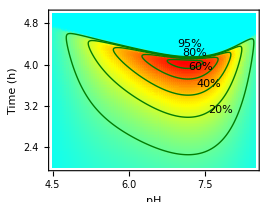

```mathematica
Clear[contourLabel];
contourLabel=
Graphics[
{Text["20%",{7.82,3.115},{0,0},{1, 1.5}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],
Text["40%",{7.575,3.625},{0,0},{1, 1.}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],
Text["60%",{7.415,3.96},{0,0},{1, 0.75}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],
Text["80%",{7.295,4.225},{0,0},{1, 0.45}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],
Text["95%",{7.2,4.41},{0,0},{1, 0.4}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}]}, PlotRange->{{2, 8}, {4, 9}}]
fitnessDensity=Show[{growthRateColorDensity,growthRateContour, contourLabel}, ImageSize->270]
```

```mathematica
Export["~/Documents/Research/Publications/Fundamental pH niche of K pneumonia/PopulationFitnessDensity_wRKPMMAv5.eps",fitnessDensity,"EPSTIFF",ImageSize->180]
```

Export::noelem: {EPSTIFF} is not a valid set of export elements for the EPS format.

$Failed

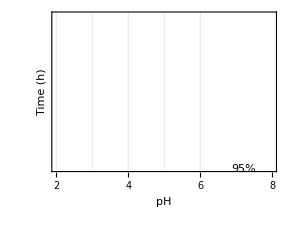

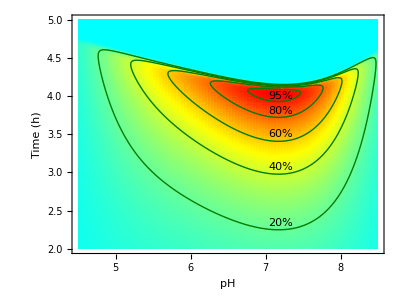

Export::nodir: Directory /Users/chuckgwo/Documents/Research/Publications/Fundamental pH niche of K pneumonia/ does not exist.

$Failed

```mathematica
Clear[contourLabel];
contourLabel=
Graphics[
{Text["20%",{7.2,2.34},{0,0},{1, 0}, TextStyle->{FontColor->Black, FontFamily->"Helvetica", FontSize->5}],
Text["40%",{7.2,3.07},{0,0},{1, 0}, TextStyle->{FontColor->Black, FontFamily->"Helvetica", FontSize->5}],
Text["60%",{7.2,3.5},{0,0},{1, 0}, TextStyle->{FontColor->Black, FontFamily->"Helvetica", FontSize->5}],
Text["80%",{7.2,3.8},{0,0},{1, 0}, TextStyle->{FontColor->Black, FontFamily->"Helvetica", FontSize->5}],
Text["95%",{7.2,4.0},{0,0},{1, 0}, TextStyle->{FontColor->Black, FontFamily->"Helvetica", FontSize->5}]}, PlotRange->{{2, 8}, {4, 9}}]
fitnessDensity=Show[{growthRateColorDensity,growthRateContour, contourLabel}]
Export["/Users/chuckgwo/Documents/Research/Publications/Fundamental pH niche of K pneumonia/PopulationFitnessDensity_wRKP.eps",fitnessDensity,"EPSTIFF",ImageSize->180]
```

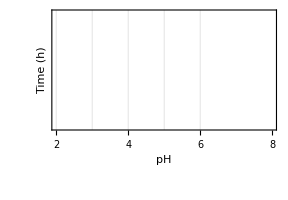

```mathematica
Clear[contourLabel, ftsz];
ftsz = 5;
contourLabel=
Graphics[
{Text["20%",{7.144,2.276},{0,0},{1, 0}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->ftsz}],
Text["40%",{7.144,3.006},{0,0},{1, 0}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->ftsz}],
Text["60%",{7.144,3.431},{0,0},{1, 0}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->ftsz}],
Text["80%",{7.144,3.741},{0,0},{1, 0}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->ftsz}],
Text["95%",{7.144,3.956},{0,0},{1, 0}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->ftsz}]}, PlotRange->{{2, 8}, {4.5, 8.5}}]
```

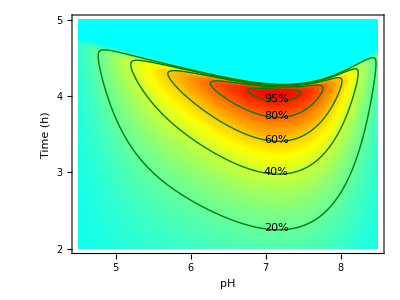

```mathematica
fitnessDensity=Show[{growthRateColorDensity,growthRateContour, contourLabel}, BaseStyle->{FontFamily->"Helvetica",FontSize->9},FrameStyle->{Thickness[0.005]}, 
FrameTicks->{
(* x ticks *)Flatten[
Table[
Prepend[Table[{x+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {x, x, {0.016, 0}, {Thickness[0.005]}}
], {x, 4, 8}
], 1
], 
(* y ticks *)Flatten[
Table[
Prepend[Table[{y+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {y, y, {0.016, 0}, {Thickness[0.005]}}
], {y, 2,5}
], 1
], 
Flatten[
Table[
Prepend[Table[{x+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {x, "", {0.016, 0}, {Thickness[0.005]}}
], {x, 4, 8}
], 1
], 
Flatten[
Table[
Prepend[Table[{y+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {y, "", {0.016, 0}, {Thickness[0.005]}}
], {y, 2,5}
], 1
]}]
```

```mathematica
Export["~/Documents/Research/Scientific Meeting/The pH Ecological Niche of K pneumoniae/PopulationFitnessDensity_wRKP_C.eps",fitnessDensity,"EPSTIFF",ImageSize->147]
```

Export::noelem: {EPSTIFF} is not a valid set of export elements for the EPS format.

$Failed

```mathematica
Clear[sGR95,sGR90, sGR80,sGR60,sGR40,sGR20];
sGR95=95/100 μMax;
sGR90=90 /100μMax;
sGR80=80/100μMax;
sGR60=60/100 μMax;
sGR40=40/100 μMax;
sGR20=20/100 μMax;
```

```mathematica
SpecificGrowthRateColorDensity=DensityPlot[μ[pH,Substrate[pH,t]],{pH,4,9},{t,2,5},AspectRatio->3/5,ColorFunction->ratecolor,FrameLabel->{"pH","Time (h)"}, Mesh->False,PlotPoints->100]
```

-Graphics-

```mathematica
Show[SpecificGrowthRateColorDensity, Background->bgc,BaseStyle->{FontFamily->"Helvetica",FontSize->9},FrameStyle->{Thickness[0.005]}, 
FrameTicks->{
(* x ticks *)Flatten[
Table[
Prepend[Table[{x+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {x, x, {0.012, 0}}
], {x, 4, 9}
], 1
], 
(* y ticks *)Flatten[
Table[
Prepend[Table[{y+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {y, y, {0.012, 0}}
], {y, 2,8}
], 1
]}
]
```

-Graphics-

```mathematica
specificGrowthRateContour=ContourPlot[μ[pH,Substrate[pH,t]],{pH,4,9},{t,2,5},AspectRatio->3/5,ContourStyle->glc,ContourShading->None,Contours->{sGR95,sGR90,sGR80,sGR60,sGR40,sGR20},FrameLabel->{"pH","Time (h)"},PlotPoints->100]
```

-Graphics-

```mathematica
Show[specificGrowthRateContour, Background->bgc,BaseStyle->{FontFamily->"Helvetica",FontSize->9},FrameStyle->{Thickness[0.005]}, 
FrameTicks->{
(* x ticks *)Flatten[
Table[
Prepend[Table[{x+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {x, x, {0.012, 0}}
], {x, 4, 9}
], 1
], 
(* y ticks *)Flatten[
Table[
Prepend[Table[{y+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {y, y, {0.012, 0}}
], {y, 2,8}
], 1
]}
]
```

-Graphics-

```mathematica
Clear[contourLabel, individualFitnessDensity, offset];
offset=-0.07;
contourLabel=
Graphics[
{Text["95%",{6.464+offset,2.89},{-1,0},{0,1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["95%",{7.660,2.597},{0,-1},{0,-1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["90%",{6.036+offset,2.99},{-1,0},{0,1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["90%",{7.879,2.697},{0,-1},{0,-1}, 
TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["80%",{5.37+offset,3.16},{-1,0},{0,1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["80%",{8.153,2.867},{0,-1},{0,-1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["60%",{4.657+offset,3.36},{-1,0},{0,1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["60%",{8.501,3.067},{0,-1},{0,-1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["40%",{4.295+offset,3.45},{-1,0},{0,1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["40%",{8.748,3.157},{0,-1},{0,-1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["20%",{4.055+offset,3.5},{-1,0},{0,1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}],Text["20%",{8.943,3.207},{0,-1},{0,-1}, TextStyle->{FontColor->glc, FontFamily->"Helvetica", FontSize->5}]}, AspectRatio->1,PlotRange->{{3.9, 9.3}, {2.9, 8.1}}];
```

```mathematica
individualFitnessDensity=Show[{SpecificGrowthRateColorDensity, specificGrowthRateContour,contourLabel}, Background->None,BaseStyle->{FontFamily->"Helvetica",FontSize->9},FrameLabel->{"pH","Time (h)"},FrameStyle->{Thickness[0.005]}, 
FrameTicks->{
(* x ticks *)Flatten[
Table[
Prepend[Table[{x+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {x, x, {0.016, 0}, {Thickness[0.005]}}
], {x, 4, 9}
], 1
], 
(* y ticks *)Flatten[
Table[
Prepend[Table[{y+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {y, y, {0.016, 0}, {Thickness[0.005]}}
], {y, 2,5}
], 1
], 
Flatten[
Table[
Prepend[Table[{x+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {x, "", {0.016, 0}, {Thickness[0.005]}}
], {x, 4, 9}
], 1
], 
Flatten[
Table[
Prepend[Table[{y+s, "", {0.008, 0}}, {s, 0.2, 0.8, 0.2}], {y, "", {0.016, 0}, {Thickness[0.005]}}
], {y, 2,5}
], 1
]}]
```

-Graphics-

The contour label above is plotted with Mathematica 5.2 running under Leopard.  Under Snow Leopard, Mathematica 5.2 has bugs and the label will be black.

```mathematica
Export["~/Documents/Research/Scientific Meeting/The pH Ecological Niche of K pneumoniae/individualFitnessDensity_wRKP.eps",individualFitnessDensity,"EPSTIFF",ImageSize->184]
```

Export::noelem: {EPSTIFF} is not a valid set of export elements for the EPS format.

$Failed

## Fundamental pH Niche of Klebsiella pneumonia

### Model Setup

To run this section, initialize the General Model Setup, K pneumoniae vs Reference Setup and appropriate section in Plot Setup.

### pH Niche of K. pneumonia (Print)

The goal of this section is to summarize the differences in reproductive power of K. pneumoniae along the pH niche axis.  

I need to find the maximum biomass reached at the end of growth from pH 4 to 9.  This value will be used to scale the reproductive power of K. pneumoniae.  In the competitive situation, the time it takes for the competition to complete is not a constant, but varies with pH.  It is plotted below.

```mathematica
Plot[timeGrowthCease[pH, sMin], {pH, 3.5, 9.5}, AxesOrigin->{3.5, 4}, Frame->True, PlotRange->{{3.5, 9.5}, {4, 5}}]
```

-Graphics-

```mathematica
Plot3D[Biomass[pH, t], {pH, 3.5, 9.5}, {t, 0, 5}]
```

-Graphics3D-

```mathematica
pHNiche=Plot[Biomass[pH, timeGrowthCease[pH, sMin]], {pH, 3.5, 9.5}, Frame->True, PlotRange->{{3.5, 9.5}, {0, 25}}]
```

-Graphics-

To find  the maximum biomass reached at the end of competition for K. pneumoniae is like finding a local maximum along a curve on the 3D surface.  I don't know how to let Mathematica find the maximum.  Let me use a more primitive method.

```mathematica
Sort[
Table[Biomass[pH, timeGrowthCease[pH, 10]], {pH, 3.9, 9.3, 0.1}], Greater
]
```

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
Table[{pH, Biomass[pH, timeGrowthCease[pH, 10]]}, {pH, 3.9, 9.3, 0.1}]
```

{{3.9,$Failed},{4.,$Failed},{4.1,$Failed},{4.2,$Failed},{4.3,$Failed},{4.4,$Failed},{4.5,$Failed},{4.6,$Failed},{4.7,$Failed},{4.8,$Failed},{4.9,$Failed},{5.,$Failed},{5.1,$Failed},{5.2,$Failed},{5.3,$Failed},{5.4,$Failed},{5.5,$Failed},{5.6,$Failed},{5.7,$Failed},{5.8,$Failed},{5.9,$Failed},{6.,$Failed},{6.1,$Failed},{6.2,$Failed},{6.3,$Failed},{6.4,$Failed},{6.5,$Failed},{6.6,$Failed},{6.7,$Failed},{6.8,$Failed},{6.9,$Failed},{7.,$Failed},{7.1,$Failed},{7.2,$Failed},{7.3,$Failed},{7.4,$Failed},{7.5,$Failed},{7.6,$Failed},{7.7,$Failed},{7.8,$Failed},{7.9,$Failed},{8.,$Failed},{8.1,$Failed},{8.2,$Failed},{8.3,$Failed},{8.4,$Failed},{8.5,$Failed},{8.6,$Failed},{8.7,$Failed},{8.8,$Failed},{8.9,$Failed},{9.,$Failed},{9.1,$Failed},{9.2,$Failed},{9.3,$Failed}}

```mathematica
Table[{pH, Biomass[pH, timeGrowthCease[pH, 10]]}, {pH, 6.9, 7.4, 0.05}]
```

{{6.9,$Failed},{6.95,$Failed},{7.,$Failed},{7.05,$Failed},{7.1,$Failed},{7.15,$Failed},{7.2,$Failed},{7.25,$Failed},{7.3,$Failed},{7.35,$Failed},{7.4,$Failed}}

```mathematica
Table[{pH, Biomass[pH, timeGrowthCease[pH, 10]]}, {pH, 7.1, 7.2, 0.01}]
```

{{7.1,$Failed},{7.11,$Failed},{7.12,$Failed},{7.13,$Failed},{7.14,$Failed},{7.15,$Failed},{7.16,$Failed},{7.17,$Failed},{7.18,$Failed},{7.19,$Failed},{7.2,$Failed}}

```mathematica
Table[{pH, Biomass[pH, timeGrowthCease[pH, 10]]}, {pH, 7.15, 7.17, 0.001}]
```

{{7.15,$Failed},{7.151,$Failed},{7.152,$Failed},{7.153,$Failed},{7.154,$Failed},{7.155,$Failed},{7.156,$Failed},{7.157,$Failed},{7.158,$Failed},{7.159,$Failed},{7.16,$Failed},{7.161,$Failed},{7.162,$Failed},{7.163,$Failed},{7.164,$Failed},{7.165,$Failed},{7.166,$Failed},{7.167,$Failed},{7.168,$Failed},{7.169,$Failed},{7.17,$Failed}}

```mathematica
Table[{pH, Biomass[pH, timeGrowthCease[pH, 10]]}, {pH, 7.16, 7.163, 0.0001}]
```

{{7.16,$Failed},{7.1601,$Failed},{7.1602,$Failed},{7.1603,$Failed},{7.1604,$Failed},{7.1605,$Failed},{7.1606,$Failed},{7.1607,$Failed},{7.1608,$Failed},{7.1609,$Failed},{7.161,$Failed},{7.1611,$Failed},{7.1612,$Failed},{7.1613,$Failed},{7.1614,$Failed},{7.1615,$Failed},{7.1616,$Failed},{7.1617,$Failed},{7.1618,$Failed},{7.1619,$Failed},{7.162,$Failed},{7.1621,$Failed},{7.1622,$Failed},{7.1623,$Failed},{7.1624,$Failed},{7.1625,$Failed},{7.1626,$Failed},{7.1627,$Failed},{7.1628,$Failed},{7.1629,$Failed},{7.163,$Failed}}

```mathematica
Plot[Biomass[pH, timeGrowthCease[pH, 10]], {pH, 7.125, 7.19}]
```

-Graphics-

From the plot and table above, maximum biomass occurs at pH 7.1615.

Biomass includes the inoculum and new growth.  When quantifing reproductive power, the inoculum should be substracted.  The error introduced is not significant when condition is good, but became enomorous at niche boundary.

```mathematica
Clear[M0,NetBiomass,MaxBiomass, maxBiomasspH, NmNetBiomass];
maxBiomasspH=7.1615;M0=(so/2)×Yield[ReferencepH]/BMmultiplication;
NetBiomass[pH_]:=Biomass[pH, timeGrowthCease[pH, sMin]] - M0;
MaxBiomass=Biomass[maxBiomasspH, timeGrowthCease[maxBiomasspH, sMin]]-M0;
NmNetBiomass[pH_]:=100*NetBiomass[pH]/MaxBiomass;
```

To define the fundamental niche of K. pneumoniae, the organism is growing alone.  All the glucose will be converted into biomass based on its energetic efficiency.  The fundamental niche can easily be defined as follows:

```mathematica
fundamentalNiche[pH_]:=Yield[pH]/Yield[nyieldMaxpH]*100
```

```mathematica
SetOptions[Plot,
Background->None (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->5},
Frame -> True,
FrameStyle->{Thickness[0.004],Black},
GridLines->{Table[{x,{GrayLevel[0.75], Thickness[0.003]}}, {x, 4,  9}],Table[{y,{GrayLevel[0.75],  Thickness[0.003]}}, {y, 0, 100, 20}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),
PlotStyle->{Thickness[0.008]}
];
```

```mathematica
NicheNBiomass=Plot[{fundamentalNiche[pH],NmNetBiomass[pH]}, {pH, 3.5, 9.5}, Frame->True, FrameLabel->{"pH", "Biomass (%)"}, PlotRange->{{3.5, 9.5}, {-2.5, 110}},PlotStyle->{{Thickness[0.0075]},{Dashing[{0.05, 0.025}],Thickness[0.0075]}}]
```

-Graphics-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","pHNiche.eps"}], NicheNBiomass, "EPS", ImageSize-> 120])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/pHNiche.eps

This graph quantify how pH affects the reproductive power of K. pneumoniae and therefore the pH niche of the organism.

I accidentally found that if the plot is exported in a smaller size and then later imported into word processing document and magnified.  The ticks mark will be more legible than exported in a regular size.  To accomplish this however, font used in label needs to be shrunk first.  Otherwise they get too big when magnified later.

The reproductive power of the organism is affected by its kinetic and energetic capacities.  Let me take a look at total glucose acquired at each pH.

Another important aspect of an organism's competitiveness is the ability to acquire growth limiting nutrient resource.  Here, let me analyze how pH affects the foraging performance of K. pneumoniae.

```mathematica
Clear[NmGlucoseCapture];
NmGlucoseCapture[pH_]:=100*(NetBiomass[pH]/Yield[pH])/(MaxBiomass/Yield[ReferencepH]);
```

```mathematica
NmlzdForagingPower=Plot[NmGlucoseCapture[pH], {pH, 3.5, 9.5}, Frame->True, PlotRange->{{3.5, 9.5}, {-5, 110}}]
```

-Graphics-

Next two important performance measure of growth is average growth rate of the entire process and maximum growth rate reached during the process.
average growth rate -> NetBiomass[pH]/timeGrowthCease[pH, sMin], 
maximum growth rate (local pH) -> growthRateMax[pH],

```mathematica
Clear[AvgGrowthRate];
AvgGrowthRate[pH_]:=NetBiomass[pH]/timeGrowthCease[pH,sMin];
```

```mathematica
SetOptions[Plot,
Background->None (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame -> True,
FrameStyle->{Thickness[0.004],Black},
GridLines->{Table[{x,{GrayLevel[0.75], Thickness[0.003]}}, {x, 4,  9}],Table[{y,{GrayLevel[0.75],  Thickness[0.003]}}, {y, 0, 15, 5}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),
PlotStyle->{Thickness[0.008]}
];
```

```mathematica
Plot[{AvgGrowthRate[pH], growthRateMax[pH]}, {pH, 3.5, 9.5},Frame->True, FrameLabel->{"pH", ""}, PlotRange->{{3.5, 9.5}, {-1, 20}},
PlotStyle->{Thickness[0.004]}]
```

-Graphics-

```mathematica
Clear[NLMaxGrowthRate, NAvgGrowthRate];
NLMaxGrowthRate[pH_]:=100*growthRateMax[pH]/growthRateGblMax;
MaxAvgGrowthRate=MaxBiomass/timeGrowthCease[ReferencepH, sMin];
NAvgGrowthRate[pH_]:=100*NetBiomass[pH]/timeGrowthCease[pH,sMin]/MaxAvgGrowthRate;
```

```mathematica
SetOptions[Plot,
Background->None (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame -> True,
FrameStyle->{Thickness[0.004],Black},
GridLines->{Table[{x,{GrayLevel[0.75], Thickness[0.003]}}, {x, 4,  9}],Table[{y,{GrayLevel[0.75],  Thickness[0.003]}}, {y, 0, 100, 20}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),
PlotStyle->{Thickness[0.008]}
];
```

```mathematica
Plot[{NLMaxGrowthRate[pH], NAvgGrowthRate[pH]}, {pH, 3.5, 9.5},Frame->True, FrameLabel->{"pH", ""}, PlotRange->{{3.5, 9.5}, {-1, 110}},
PlotStyle->{Thickness[0.004]}]
```

-Graphics-

Let me plot all 4 normalized growth performance characteristics in one plot.

```mathematica
NichePlot4=Plot[{NmNetBiomass[pH],NmGlucoseCapture[pH],NLMaxGrowthRate[pH],NAvgGrowthRate[pH]},{pH,3.5,9.5},Frame->True,FrameLabel->{"pH",""},PlotRange->{{3.5,9.5},{-5,110}},PlotStyle->{{RGBColor[0.75,0.75,0]},{Green},{Red},{Pink}}]
```

-Graphics-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","NichePlot4.eps"}], NichePlot4, "EPS", ImageSize-> 288])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/NichePlot4.eps

```mathematica
NLMaxGrowthRate[pH], NAvgGrowthRate[pH]
```

Let me plot them in original units.

```mathematica
Plot[{NetBiomass[pH],NetBiomass[pH]/Yield[pH]/10,AvgGrowthRate[pH], growthRateMax[pH]}, {pH, 3.5, 9.5},Frame->True, FrameLabel->{"pH", ""}, PlotRange->{{3.5, 9.5}, {-1, 25}},
PlotStyle->{Thickness[0.004]}]
```

-Graphics-

### pH Niche of K. pneumonia (Presentation)

```mathematica
Clear[M0,NetBiomass,MaxBiomass, maxBiomasspH, NmNetBiomass];
maxBiomasspH=7.1615;M0=(so/2)×Yield[ReferencepH]/BMmultiplication;
NetBiomass[pH_]:=Biomass[pH, timeGrowthCease[pH, sMin]] - M0;
MaxBiomass=Biomass[maxBiomasspH, timeGrowthCease[maxBiomasspH, sMin]]-M0;
NmNetBiomass[pH_]:=100*NetBiomass[pH]/MaxBiomass;
```

```mathematica
fundamentalNiche[pH_]:=Yield[pH]/Yield[nyieldMaxpH]*100
```

```mathematica
SetOptions[Plot,
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
GridLines->{Table[{x,{glc, Thickness[0.003]}}, {x, 4,  9}],Table[{y,{glc,  Thickness[0.003]}}, {y, 0, 100, 20}]},PlotStyle->{Thickness[0.008]}
];
```

```mathematica
NicheNBiomass=Plot[{fundamentalNiche[pH],NmNetBiomass[pH]}, {pH, 3.5, 9.5}, Frame->True, FrameLabel->{"pH", "Biomass (%)"}, PlotRange->{{3.5, 9.5}, {-2.5, 110}},PlotStyle->{{D4,Thickness[0.0075]},{D1,Thickness[0.0075]}}]
```

-Graphics-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","pHNiche.eps"}], NicheNBiomass, "EPS"])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/pHNiche.eps

```mathematica
SetOptions[Plot,
Background->bgc (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame -> True,
FrameStyle->{Thickness[0.008],fmc},
GridLines->{Table[{x,{glc, Thickness[0.0015], Dashing[{0.005, 0.0125}] }}, {x, 4, 9, 0.5}],Table[{y,{glc,  Thickness[0.0015], Dashing[{0.005, 0.0125}]}}, {y, 0, 100, 10}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),
PlotStyle->{Thickness[0.008]}
];
```

```mathematica
NicheNBiomass=Plot[NmNetBiomass[pH], {pH, 3.5, 9.5}, Frame->True, PlotRange->{{3.5, 9.5}, {-5, 110}}, PlotStyle->{D6, Thickness[0.005]}]
```

-Graphics-

```mathematica
NmlzdForagingPower=Plot[NmGlucoseCapture[pH], {pH, 3.5, 9.5}, Frame->True, PlotRange->{{3.5, 9.5}, {-5, 110}}, PlotStyle->{D4, Thickness[0.005]}]
```

-Graphics-

```mathematica
fundaentalpHNiche=Show[NmlzdForagingPower, NicheNBiomass]
```

-Graphics-

```mathematica
(Quiet[CreateDirectory[FileNameJoin[{NotebookDirectory[],"migrated"}]]];Export[FileNameJoin[{NotebookDirectory[],"migrated","fundaentalpHNicheC2.eps"}], fundaentalpHNiche, "EPS"])
```

/Users/albertgwo/Projects/mathematica-migration/migrated/fundaentalpHNicheC2.eps

### Performance by Number

It will be helpful to have a table listing various performance differences of K. pneumonia at different pHs.  Here are the information to be include in the table.

biomass produced -> NetBiomass[pH], 
glucose consumed -> NetBiomass[pH]/Yield[pH], 
Process time -> timeGrowthCease[pH, sMin];
average growth rate -> NetBiomass[pH]/timeGrowthCease[pH, sMin], 
maximum growth rate (local pH) -> growthRateMax[pH],

```mathematica
Clear[M0,NetBiomass, NetBiomassRef, totalBiomass, glucoseConsumed, percentKpBiomass, percentRefBiomass, avgGthRate, NavgGthRate];
M0=(so/2)×Yield[ReferencepH]/BMmultiplication;
NetBiomass[pH_]:=Biomass[pH, timeGrowthCease[pH, sMin]] - M0;
NetBiomassRef[pH_]:= BiomassRef[pH, timeGrowthCease[pH, sMin]] - M0;
totalBiomass[pH_]:= NetBiomass[pH]+NetBiomassRef[pH];
glucoseConsumed[pH_]:= so-Substrate[pH,timeGrowthCease[pH, sMin]];
percentKpBiomass[pH_]:= NetBiomass[pH]/totalBiomass[pH];
percentRefBiomass[pH_]:= NetBiomassRef[pH]/totalBiomass[pH];
avgGthRate[pH_]:=NetBiomass[pH]/timeGrowthCease[pH,sMin] ;
NavgGthRate[pH_]:=100*avgGthRate[pH]/avgGthRate[ReferencepH];
```

The percentages of glucose captured by K. pneumoniae and RKP do not add to so - sMin.  Need to check why it does not?  One thing to check, is to know how much glucose is left at timeGrowthCease.

The amount of glucose left at timeGrowthCease should be 10 μM, because timeGrowthCease use the EventLocator in NDSolve to locate the time when substrate drops to sMin and sMin is set at 10 μM.  Obviously, EventLocator is not functioning as expected!  Need to contact Wolfram in the future to find out why!

```mathematica
Clear[GrowthPerformanceByNumber];
finalGlucose=
Table[{pH,
Substrate[pH,timeGrowthCease[pH, sMin]]},
{pH, 4., 9., 0.5}
];
PaddedForm[
TableForm[
finalGlucose, TableDirections->{Row,Column},  
TableHeadings->{ None, {"pH","Final Glucose"}}
], {3, 2}]
```

pH |  4.00 |  4.50 |  5.00 |  5.50 |  6.00 |  6.50 |  7.00 |  7.50 |  8.00 |  8.50 |  9.00
Final Glucose | $Failed | $Failed | $Failed | $Failed | $Failed | $Failed | $Failed | $Failed | $Failed | $Failed | $Failed

```mathematica
Clear[GrowthPerformanceByNumber];
GrowthPerformanceByNumber=
Table[{pH,
percentKpBiomass[pH] (* % Biomass Produced by K. pneumoniae *), 
NetBiomass[pH]/Yield[pH] /glucoseConsumed[pH](* % Glucose Consumed by K. pneumoniae *), 
percentRefBiomass[pH] (* % Biomass Produced by Reference *), 
NetBiomassRef[pH]/Yield[ReferencepH] /glucoseConsumed[pH](* % Glucose Consumed by Reference *)},
{pH, 4., 9., 0.5}
];
PaddedForm[
TableForm[
GrowthPerformanceByNumber, TableDirections->{Row,Column},  
TableHeadings->{ None, {"pH","Kp Biomass %", "Kp Glucose %", "Ref Biomass %", "Ref Glucose%"}}
], {4, 2}]
```

pH |   4.00 |   4.50 |   5.00 |   5.50 |   6.00 |   6.50 |   7.00 |   7.50 |   8.00 |   8.50 |   9.00
Kp Biomass % | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed)
Kp Glucose % | (76.15 ( -0.39+$Failed))/(500-$Failed) | (17.86 ( -0.39+$Failed))/(500-$Failed) | (13.93 ( -0.39+$Failed))/(500-$Failed) | (13.18 ( -0.39+$Failed))/(500-$Failed) | (13.03 ( -0.39+$Failed))/(500-$Failed) | (12.88 ( -0.39+$Failed))/(500-$Failed) | (12.81 ( -0.39+$Failed))/(500-$Failed) | (13.32 ( -0.39+$Failed))/(500-$Failed) | (15.41 ( -0.39+$Failed))/(500-$Failed) | (22.50 ( -0.39+$Failed))/(500-$Failed) | (78.92 ( -0.39+$Failed))/(500-$Failed)
Ref Biomass % | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed) | (-0.39+$Failed)/(-0.78+    2 $Failed)
Ref Glucose% | (12.89 ( -0.39+$Failed))/(500-$Failed) | (12.89 ( -0.39+$Failed))/(500-$Failed) | (12.89 ( -0.39+$Failed))/(500-$Failed) | (12.89 ( -0.39+$Failed))/(500-$Failed) | (12.89 ( -0.39+$Failed))/(500-$Failed) | (12.89 ( -0.39+$Failed))/(500-$Failed) | (12.89 ( -0.39+$Failed))/(500-$Failed) | (12.89 ( -0.39+$Failed))/(500-$Failed) | (12.89 ( -0.39+$Failed))/(500-$Failed) | (12.89 ( -0.39+$Failed))/(500-$Failed) | (12.89 ( -0.39+$Failed))/(500-$Failed)

```mathematica
Export["~/Documents/Research/Publications/Fundamental pH niche of K pneumonia/PerformanceByNo.csv", GrowthPerformanceByNumber]
```

~/Documents/Research/Publications/Fundamental pH niche of K pneumonia/PerformanceByNo.csv

```mathematica
Clear[GrowthPerformanceByNumber];
GrowthPerformanceByNumber=
Table[{pH,
NetBiomass[pH] (* % Biomass Produced by K. pneumoniae *), 
NetBiomass[pH]/Yield[pH] (* Glucose Consumed by K. pneumoniae *), 
timeGrowthCease[pH,sMin] (* Process Time *), 
NetBiomass[pH]/timeGrowthCease[pH,sMin] (* Average Growth Rate *), 
growthRateMax[pH] (* Local Maximum Growth Rate *)}, 
{pH, 4., 9., 0.5}
];
PaddedForm[
TableForm[
GrowthPerformanceByNumber, TableDirections->{Row,Column},  
TableHeadings->{ None, {"pH","Biomass", "Glucose","Process Time", "Avg Gth Rate", "Max Gth Rate"}}
], {5, 2}]
```

pH |    4.00 |    4.50 |    5.00 |    5.50 |    6.00 |    6.50 |    7.00 |    7.50 |    8.00 |    8.50 |    9.00
Biomass |   -0.39+$Failed |   -0.39+$Failed |   -0.39+$Failed |   -0.39+$Failed |   -0.39+$Failed |   -0.39+$Failed |   -0.39+$Failed |   -0.39+$Failed |   -0.39+$Failed |   -0.39+$Failed |   -0.39+$Failed
Glucose |   76.15 (  -0.39+$Failed) |   17.86 (  -0.39+$Failed) |   13.93 (  -0.39+$Failed) |   13.18 (  -0.39+$Failed) |   13.03 (  -0.39+$Failed) |   12.88 (  -0.39+$Failed) |   12.81 (  -0.39+$Failed) |   13.32 (  -0.39+$Failed) |   15.41 (  -0.39+$Failed) |   22.50 (  -0.39+$Failed) |   78.92 (  -0.39+$Failed)
Process Time | $Failed | $Failed | $Failed | $Failed | $Failed | $Failed | $Failed | $Failed | $Failed | $Failed | $Failed
Avg Gth Rate | (-0.39+$Failed)/($Failed) | (-0.39+$Failed)/($Failed) | (-0.39+$Failed)/($Failed) | (-0.39+$Failed)/($Failed) | (-0.39+$Failed)/($Failed) | (-0.39+$Failed)/($Failed) | (-0.39+$Failed)/($Failed) | (-0.39+$Failed)/($Failed) | (-0.39+$Failed)/($Failed) | (-0.39+$Failed)/($Failed) | (-0.39+$Failed)/($Failed)
Max Gth Rate |    0.04 |    1.47 |    4.92 |    8.40 |   11.34 |   14.04 |   15.89 |   15.04 |    9.89 |    2.90 |    0.10

```mathematica
growthRateGblMaxTime
growthRateGblMaxpH
growthRateGblMax
```

4.03564

7.14416

16.0164

## Fundamental pH Niche of Klebsiella pneumonia (11.3 D)

### Model Setup

In this section, I want to  show that the exact shape of the fundamental niche of an organism depends on the condition of the system under which growth occurs.  Here I want to show that if the population go through a longer growth process, more doubling for the population, then the bell shaped fundamental niche curve will have a narrower peak.  To accomplish this, I need to change the initial condition of the model to the following:

Clear[ReferencepH];
Ks=4; (* μMolar *)
so=500; (* μMolar *)
Tmax = 20 ;(* hr *)
ReferencepH=692046/100000;
BMmultiplication=500;
sMin=so*2/100 (* μMolar *);

Here, the so has increased from 500 to 5000 μMolar and BMmultiplication increased from 50 to 2500.  With this change the inoculum size has changed to 1/5 of the original model.

Tmax increased to 30 hrs

#### Growth Model Setup with The Casheing Method

Copied from "Growth of K pneumoniae vs pH - 3D Plot MMAv5".  Added the following:

(* Here let me define the pH niche boundary of K. pneumoniae. *)

pHNicheBoundaryLow=Max[SGRpHLowBnd, YieldpHLowBnd];
pHNicheBoundaryHigh=Min[SGRpHHighBnd, YieldpHHighBnd];

```mathematica
Off[General::spell, General::spell1];

expmtlpH=.;SGR=.;SGRvspHData=.;wkgPrcsn=.
SGRvspHroot=.;SGRpHLowBnd=.;SGRpHHighBnd=.
μMaxSolve=.;μMax=.;μMaxpH=.
Clear[pH,SGRvspHFitPrmtr, SGRvspHFitEqtn, SGRvspH,μo];

wkgPrcsn=Automatic;
expmtlpH={395,407,448,497,597,700,792,845,892,910}/100;
SGR={0,9,45,60,81,90,72,53,24,0} /100(* hr^-1 *);
SGRvspHData=Transpose[{expmtlpH,SGR}];
Clear[expmtlpH,SGR];

SGRvspH[pH_]=
Module[{a,b,c,d,e,f,x,FitPrmtr},
FitPrmtr=
FindFit[SGRvspHData,
a+b x+c x^2+d x^3+e x^4+f x^5,
{a,b,c,d,e,f},x,WorkingPrecision->wkgPrcsn
];
a+b pH+c pH^2+d pH^3+e pH^4+f pH^5/.FitPrmtr
];
SGRvspHroot=Solve[SGRvspH[pH]==0,pH];
SGRpHLowBnd=SGRvspHroot[[1,1,2]];
SGRpHHighBnd=SGRvspHroot[[4,1,2]];

μo[pH_?NumericQ/;pH<SGRpHLowBnd||pH>SGRpHHighBnd]:=0
μo[pH_?NumericQ/;(pH≥SGRpHLowBnd)∧(pH≤SGRpHHighBnd)]:= SGRvspH[pH]

μMaxSolve=FindMaximum[μo[pH],{pH,69/10}, WorkingPrecision->wkgPrcsn];
μMax=μMaxSolve[[1]](* hr^-1 *);
μMaxpH=μMaxSolve[[2, 1, 2]];
Remove[SGRvspHroot, μMaxSolve];

(*Equation 2 can now be defined *)
s=.;Ks=.
Clear[μ, Nμ];
μ[pH_, s_]:=μo[pH] s/(Ks+s) ;
Nμ[pH_?NumericQ,s_?NumericQ]:=μ[pH,s]/μMax;


YOutsideNiche=.;expmtlpH=.;nYieldData=.;YvspHdata=.
YieldvspHRoot=.;YieldpHLowBnd=.;YieldpHHighBnd=.
Clear[YieldvspH, NYield];

expmtlpH=
{395,407,448,497,597,700,792,845,892,910}/100;
nYieldData={0,32,68,79,97,95,81,51,30,0}/100;
YvspHdata=Transpose[{expmtlpH,nYieldData}];
Clear[expmtlpH,nYieldData];

YieldvspH[pH_]=
Module[{a,b,c,d,e,f,x,FitPrmtr},
FitPrmtr=
FindFit[YvspHdata,
a+b x+c x^2+d x^3+e x^4+f x^5,
{a,b,c,d,e,f},x,WorkingPrecision->wkgPrcsn
];
a+b pH+c pH^2+d pH^3+e pH^4+f pH^5/.FitPrmtr
];
YieldvspHRoot=Solve[YieldvspH[pH]==0,pH];
YieldpHLowBnd=YieldvspHRoot[[1,1,2]];
YieldpHHighBnd=YieldvspHRoot[[4,1,2]];

YOutsideNiche=1/10^5;NYield[pH_?NumericQ/;pH<YieldpHLowBnd||pH>YieldpHHighBnd]:=YOutsideNiche;
NYield[pH_?NumericQ/;(pH≥YieldpHLowBnd)∧(pH≤YieldpHHighBnd)]:=YieldvspH[pH];

Clear[nyieldMaxSolve,nyieldMax,nyieldMaxpH];
nyieldMaxSolve=FindMaximum[NYield[pH],{pH,7},WorkingPrecision->wkgPrcsn];
nyieldMax=nyieldMaxSolve[[1]];
nyieldMaxpH=nyieldMaxSolve[[2,1,2]];
Remove[nyieldMaxSolve];

(* Multiplying Normalized growth yield by the maximum, growth yield at pH 7, 82.2 g/mole glucose, we get growth yield. *)
MaxYieldpH7=.
Clear[Yield];
MaxYieldpH7=822/10000  ;(* mg/μmole glucose *)
Yield[pH_]:=MaxYieldpH7 × NYield[pH];(* mg/μmole glucose *)

(* Here let me define the pH niche boundary of K. pneumoniae. *)
pHNicheBoundaryLow=Max[SGRpHLowBnd, YieldpHLowBnd];
pHNicheBoundaryHigh=Min[SGRpHHighBnd, YieldpHHighBnd];
```

FindMaximum::bddir: The search direction {-0.000012282806368403603129888122367166243059953448787526842904279463175} is not an ascent direction for the function. Typically this occurs when the function is not smooth or the values of the function are much less accurate than the WorkingPrecision.

```mathematica
Clear[ReferencepH];
Ks=4;(* μMolar *)
so=500;(* μMolar *)
Tmax=20;(* hr *)
ReferencepH=692046/100000;
BMmultiplication=500;
sMin=so*2/100 (* μMolar *);
```

```mathematica
Clear[Biomass, BiomassRef, Substrate, BiomassCache, BiomassRefCache, SubstrateCache];

Biomass[pH_, t_]:=
Module[{result, solution, M, MRef, s, time},
result=BiomassCache[pH, t];
If[
NumberQ[result], 
Return[result]
];

(* Biomass[pH, t] doesn't exist,use NDSolve to solve the system of differential equation. *)
solution=
NDSolve[
{MRef'[time]==MRef[time]×μ[ReferencepH,s[time]],M'[time]==M[time]×μ[pH,s[time]],
s'[time]==-MRef'[time]/Yield[ReferencepH]-M'[time]/Yield[pH],
MRef[0]==(so/2)×Yield[ReferencepH]/BMmultiplication,
M[0]==(so/2)×Yield[ReferencepH]/BMmultiplication ,
s[0]==so},
{MRef,M,s},{time,0,Tmax}

(*,AccuracyGoal->21,WorkingPrecision->24 *)
][[1]];

(* Biomass, BiomassRef and Substrate will be cached for future use. *)
BiomassRefCache[pH, time_]=MRef[time]/.solution;
BiomassCache[pH, time_]=M[time]/.solution;
SubstrateCache[pH, time_]=s[time]/.solution;

result=BiomassCache[pH, t];
If[
NumberQ[result],
Return[result],
$Failed
]
];

Biomass::usage="Biomass[pH, t] gives the biomass of K. pheumoniae, in mg/l, at time t growing at pH competing against reference population growing at optimum pH.";

BiomassRef[pH_, t_]:=
Module[{result, solution, M, MRef, s, time},
result=BiomassRefCache[pH, t];
If[
NumberQ[result], 
Return[result]
];

(* BiomassRef[pH, t] doesn't exist,use NDSolve to solve the system of differential equation. *)
solution=
NDSolve[
{MRef'[time]==MRef[time]×μ[ReferencepH,s[time]],M'[time]==M[time]×μ[pH,s[time]],
s'[time]==-MRef'[time]/Yield[ReferencepH]-M'[time]/Yield[pH],
MRef[0]==(so/2)×Yield[ReferencepH]/BMmultiplication,
M[0]==(so/2)×Yield[ReferencepH]/BMmultiplication ,
s[0]==so},
{MRef,M,s},{time,0,Tmax}

(*,AccuracyGoal->21,WorkingPrecision->24 *)
][[1]];

(* Biomass, BiomassRef and Substrate will be cached for future use. *)
BiomassRefCache[pH, time_]=MRef[time]/.solution;
BiomassCache[pH, time_]=M[time]/.solution;
SubstrateCache[pH, time_]=s[time]/.solution;

result=BiomassRefCache[pH, t];
If[
NumberQ[result],
Return[result],
$Failed
]
];

BiomassRef::usage="BiomassRef[pH, t] gives the biomass of reference K. pheumoniae population, in mg/l, at time t growing as if at optimum pH competing against another K. pheumoniae population growing at pH.";

Substrate[pH_, t_]:=
Module[{result, solution, M, MRef, s, time},
result=SubstrateCache[pH, t];
If[
NumberQ[result], 
Return[result]
];

(* Substrate[pH, t] doesn't exist,use NDSolve to solve the system of differential equation. *)
solution=
NDSolve[
{MRef'[time]==MRef[time]×μ[ReferencepH,s[time]],M'[time]==M[time]×μ[pH,s[time]],
s'[time]==-MRef'[time]/Yield[ReferencepH]-M'[time]/Yield[pH],
MRef[0]==(so/2)×Yield[ReferencepH]/BMmultiplication,
M[0]==(so/2)×Yield[ReferencepH]/BMmultiplication ,
s[0]==so},
{MRef,M,s},{time,0,Tmax}

(*,AccuracyGoal->21,WorkingPrecision->24*)
][[1]];

(* Biomass, BiomassRef and Substrate will be cached for future use. *)
BiomassRefCache[pH, time_]=MRef[time]/.solution;
BiomassCache[pH, time_]=M[time]/.solution;
SubstrateCache[pH, time_]=s[time]/.solution;

result=SubstrateCache[pH, t];
If[
NumberQ[result],
Return[result],
$Failed
]
];

Substrate::usage="Substrate[pH, t], in μMolar, gives the glucose concentration at time t of a medium with two K. pheumoniae population competing against one another.  Two K. pheumoniae populations are growing as if the medium pH were pH and ReferencepH.";
```

#### Growth Rate, Maximum Growth Rate, Normalized Growth Rate

Normalized specific growth rate is defined in the previous section.

```mathematica
Clear[growthRate, growthRateRef];
growthRate[pH_?NumericQ, t_?NumericQ](* mg/l hr *):=μ[pH, Substrate[pH,t]] × Biomass[pH, t];
growthRateRef[pH_?NumericQ, t_?NumericQ](* mg/l hr *):=μ[ReferencepH, Substrate[pH,t]] × BiomassRef[pH, t];
```

```mathematica
(* Defines global maximum growth rate of K pneumoniae in a competitive situation between itself and the Reference. Developed in Fundamental pH Hiche of K pneumoniae - MMAv5. *)
Clear[maxGrowthRateSolution];
maxGrowthRateSolution=FindMinimum[-growthRate[pH,t],{{pH,68/10,69/10},{t,36/10,37/10}}];
growthRateGblMaxTime=maxGrowthRateSolution[[2,2,2]];
growthRateGblMaxpH=maxGrowthRateSolution[[2,1,2]];
growthRateGblMax=-maxGrowthRateSolution[[1]];

Clear[GblNmGrowthRate];
GblNmGrowthRate[pH_?NumericQ, t_?NumericQ]:=growthRate[pH, t]/growthRateGblMax;
```

```mathematica
(* Defines maximum growth rate of K pneumoniae and Reference at local pHs. Developed in "Fundamental pH Hiche of K pneumoniae - MMAv5. *)
Clear[growthRateMax, growthRateMaxCache, growthRateMaxTime, growthRateMaxTimeCache, growthRateMaxRef, growthRateMaxRefCache, growthRateMaxTimeRef, growthRateMaxTimeRefCache];


growthRateMax[pH_?NumberQ](* mg/(l hr) *):=
Module[{result, solution, t},

result=growthRateMaxCache[pH];
If[NumberQ[result],Return[result]];

(* growthRateMax does not exist at the spicified pH.  New search needed to find the result. *)
solution=
Which[
(* Outside niche boundary. *)
pH≤pHNicheBoundaryLow||pH≥pHNicheBoundaryHigh, {0, {t->0}},
(* Within niche boundary. *)
pH>pHNicheBoundaryLow∧pH<pHNicheBoundaryHigh,
FindMinimum[-growthRate[pH, t], {t, 2, 3}]
];
growthRateMaxCache[pH]=-solution[[1]];
growthRateMaxTimeCache[pH]=t/.solution[[2]];

result=growthRateMaxCache[pH];
If[NumberQ[result],Return[result], $Failed];
];
growthRateMax::usage="growthRateMax[pH], mg/(l hr), gives the maximum growth rate of K. pheumoniae growing at pH in competition with another population growing at ReferencepH";


growthRateMaxTime[pH_?NumberQ](* hr *):=
Module[{result, solution, t},
result=growthRateMaxTimeCache[pH];
If[NumberQ[result],Return[result]];

(* growthRateMaxTime does not exist at the spicified pH.  New search needed to find the result. *)
solution=
Which[
(* Outside niche boundary. *)
pH≤pHNicheBoundaryLow||pH≥pHNicheBoundaryHigh, {0, {t->0}},
(* Within niche boundary. *)
pH>pHNicheBoundaryLow∧pH<pHNicheBoundaryHigh,
FindMinimum[-growthRate[pH, t], {t, 2, 3}]
];
growthRateMaxCache[pH]=-solution[[1]];
growthRateMaxTimeCache[pH]=t/.solution[[2]];

result=growthRateMaxTimeCache[pH];
If[NumberQ[result],Return[result], $Failed];
];
growthRateMaxTime::usage="growthRateMaxTime[pH], hr, gives the time at which growth rate of the population growing at pH reaches maximum.";


growthRateMaxRef[pH_?NumberQ](* mg/(l hr) *):=
Module[{result, solution, t},

result=growthRateMaxRefCache[pH];
If[NumberQ[result],Return[result]];

(* growthRateMaxRefCache does not exist at the spicified pH.  New search needed to find the result. *)
solution=
FindMinimum[-growthRateRef[pH, t], {t, 2, 3}];
growthRateMaxRefCache[pH]=-solution[[1]];
growthRateMaxTimeRefCache[pH]=t/.solution[[2]];

result=growthRateMaxRefCache[pH];
If[NumberQ[result],Return[result], $Failed];
];
growthRateMaxRef::usage="growthRateMaxRef[pH], mg/(l hr), gives the maximum growth rate of reference K. pheumoniae population growing at ReferencepH";


growthRateMaxTimeRef[pH_?NumberQ](* hr *):=
Module[{result, solution, t},

result=growthRateMaxTimeRefCache[pH];
If[NumberQ[result],Return[result]];

solution=FindMinimum[-growthRateRef[pH, t], {t, 2, 3}];
growthRateMaxRefCache[pH]=-solution[[1]];
growthRateMaxTimeRefCache[pH]=t/.solution[[2]];

result=growthRateMaxTimeRefCache[pH];
If[NumberQ[result],Return[result], $Failed];
];
growthRateMaxTimeRef::usage="growthRateMaxTimeRef[pH], hr, gives the time at which growth rate of reference K. pheumoniae population growing at pH 7 reaches maximum.";
```

```mathematica
(* Growth rate normalized against local maximum of the Reference population. *)
Clear[LocalNmGrowthRate, LocalNmGrowthRateRef];
LocalNmGrowthRate[pH_?NumericQ, t_?NumericQ]:=growthRate[pH, t]/growthRateMaxRef[pH];
LocalNmGrowthRateRef[pH_?NumericQ, t_?NumericQ]:=growthRateRef[pH, t]/growthRateMaxRef[pH];
```

#### Vector Algebra

```mathematica
Clear[PointsToVector];PointsToVector[pointA_List, pointB_List, pointC_List]:={pointB-pointA, pointC-pointB};
```

```mathematica
Clear[angleBetweenTwoVectors];
angleBetweenTwoVectors[u_List, v_List]:=
ArcCos[u . v/(Sqrt[u . u] Sqrt[v . v])
]/(2 Pi)*360;
angleBetweenTwoVectors::usage="angleBetweenTwoVectors[u, v] gives the angle in degrees between two vector, u and v, of the same dimension.  Vectors, u and v, can be of any dimension.  Vector has the format of {x, y, z, ...}.";
```

```mathematica
Clear[vectorLength];
vectorLength[u_List]:=Sqrt[u.u];
vectorLength::usage="vectorLength[u] gives the length of vector u in n-dimensional space.";
```

```mathematica
Clear[vectorProjection];
vectorProjection[vectorA_List, vectorB_List]:=(vectorA.vectorB/vectorB.vectorB) vectorB;
vectorProjection::usage="vectorProjection[vectorA, vectorB] gives the projection of vectorA onto vectorB.";
```

#### Time Growth Stops

```mathematica
Clear[timeGrowthCease];
timeGrowthCease[pH_, sMin_]:=
Module[{Tmax, solution, MRef, M, s, time, endTime},
Tmax= 10;
solution=
NDSolve[
{MRef'[time]==MRef[time]×μ[ReferencepH,s[time]],M'[time]==M[time]×μ[pH,s[time]],
s'[time]==-MRef'[time]/Yield[ReferencepH]-M'[time]/Yield[pH],
MRef[0]==(so/2)×Yield[ReferencepH]/BMmultiplication,M[0]==(so/2)× Yield[pH]/BMmultiplication ,
s[0]==so},
{MRef,M,s},{time,0,Tmax}, 
Method -> {"EventLocator", "Event" -> (s[time]-sMin)}
];

endTime=
InterpolatingFunctionDomain[
M/.solution[[1]]
][[1, 2]];

If[NumberQ[endTime], Return[endTime], $Failed]
];
timeGrowthCease::usage="timeGrowthCease[pH, sMin] gives the time when substrate concentration drops to sMin and the process stops.  pH is media pH.";
```

```mathematica
Clear[timeGrowthCeaseAnchorPoints, timeGrowthCeaseIFunction, timeGrowthCurveEnd];
timeGrowthCeaseAnchorPoints=
Table[{pH,timeGrowthCease[pH, sMin]}, {pH, SGRpHLowBnd, SGRpHHighBnd, 0.1}];
timeGrowthCeaseIFunction=
Interpolation[timeGrowthCeaseAnchorPoints];
timeGrowthCurveEnd[pH_]:=timeGrowthCeaseIFunction[pH]+0.25;
```

### pH Niche of K. pneumonia (Print)

#### 11.3 Doubling

Clear[ReferencepH];
Ks=4; (* μMolar *)
so=5000; (* μMolar *)
Tmax = 12 ;(* hr *)
ReferencepH=692046/100000;
BMmultiplication=2500;
sMin=so*2/100 (* μMolar *);

Here, the so has increased from 500 to 5000 μMolar and BMmultiplication increased from 50 to 2500.  With this change the inoculum size has changed to 1/5 of the original model.

Tmax increased to 30 hrs

```mathematica
Clear[M0,NetBiomass,MaxBiomass];
M0=(so/2)×Yield[ReferencepH]/BMmultiplication;
NetBiomass[pH_]:=Biomass[pH, timeGrowthCease[pH, sMin]] - M0;
MaxBiomass=Biomass[ReferencepH, timeGrowthCease[ReferencepH, sMin]]-M0;
```

```mathematica
SetOptions[Plot,
Background->None (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame -> True,
FrameStyle->{Thickness[0.004],Black},
GridLines->{Table[{x,{GrayLevel[0.75], Thickness[0.003]}}, {x, 4,  9}],Table[{y,{GrayLevel[0.75],  Thickness[0.003]}}, {y, 0, 20, 5}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),
PlotStyle->{Thickness[0.006]}
];
```

```mathematica
Clear[NmNetBiomass];
NmNetBiomass[pH_]:=100*NetBiomass[pH]/MaxBiomass;
```

```mathematica
SetOptions[Plot,
Background->None (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->9},
Frame -> True,
FrameStyle->{Thickness[0.004],Black},
GridLines->{Table[{x,{GrayLevel[0.75], Thickness[0.003]}}, {x, 4,  9}],Table[{y,{GrayLevel[0.75],  Thickness[0.003]}}, {y, 0, 100, 20}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),
PlotStyle->{Thickness[0.008]}
];
```

```mathematica
NicheNBiomass=Plot[NmNetBiomass[pH], {pH, 3.5, 9.5}, Frame->True, FrameLabel->{"pH", "Reproductive Potential"}, PlotRange->{{3.5, 9.5}, {-2.5, 110}}]
```

-Graphics-

```mathematica
Clear[NmGlucoseCapture];
NmGlucoseCapture[pH_]:=100*(NetBiomass[pH]/Yield[pH])/(MaxBiomass/Yield[ReferencepH]);
```

```mathematica
NmlzdForagingPower=Plot[NmGlucoseCapture[pH], {pH, 3.5, 9.5}, Frame->True, PlotRange->{{3.5, 9.5}, {-5, 110}}]
```

-Graphics-

```mathematica
Clear[AvgGrowthRate];
AvgGrowthRate[pH_]:=NetBiomass[pH]/timeGrowthCease[pH,sMin];
```

```mathematica
SetOptions[Plot,
Background->None (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame -> True,
FrameStyle->{Thickness[0.004],Black},
GridLines->{Table[{x,{GrayLevel[0.75], Thickness[0.003]}}, {x, 4,  9}],Table[{y,{GrayLevel[0.75],  Thickness[0.003]}}, {y, 0, 200, 50}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),
PlotStyle->{Thickness[0.008]}
];
```

```mathematica
Plot[{AvgGrowthRate[pH], growthRateMax[pH]}, {pH, 3.5, 9.5},Frame->True, FrameLabel->{"pH", ""}, PlotRange->{{3.5, 9.5}, {-5, 200}},
PlotStyle->{Thickness[0.004]}]
```

-Graphics-

```mathematica
Clear[NLMaxGrowthRate, NAvgGrowthRate];
NLMaxGrowthRate[pH_]:=100*growthRateMax[pH]/growthRateGblMax;
MaxAvgGrowthRate=MaxBiomass/timeGrowthCease[ReferencepH, sMin];
NAvgGrowthRate[pH_]:=100*NetBiomass[pH]/timeGrowthCease[pH,sMin]/MaxAvgGrowthRate;
```

```mathematica
SetOptions[Plot,
Background->None (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame -> True,
FrameStyle->{Thickness[0.004],Black},
GridLines->{Table[{x,{GrayLevel[0.75], Thickness[0.003]}}, {x, 4,  9}],Table[{y,{GrayLevel[0.75],  Thickness[0.003]}}, {y, 0, 100, 20}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),
PlotStyle->{Thickness[0.008]}
];
```

```mathematica
Plot[{NLMaxGrowthRate[pH], NAvgGrowthRate[pH]}, {pH, 3.5, 9.5},Frame->True, FrameLabel->{"pH", ""}, PlotRange->{{3.5, 9.5}, {-1, 110}},
PlotStyle->{Thickness[0.004]}]
```

-Graphics-

```mathematica
NichePlot4=Plot[{NmNetBiomass[pH],NmGlucoseCapture[pH],NLMaxGrowthRate[pH],NAvgGrowthRate[pH]},{pH,3.5,9.5},Frame->True,FrameLabel->{"pH",""},PlotRange->{{3.5,9.5},{-5,110}},PlotStyle->{{RGBColor[0.75,0.75,0]},{Green},{Red},{Pink}}]
```

-Graphics-

```mathematica
Plot[{NetBiomass[pH],NetBiomass[pH]/Yield[pH]/10,AvgGrowthRate[pH], growthRateMax[pH]}, {pH, 3.5, 9.5},Frame->True, FrameLabel->{"pH", ""}, PlotRange->{{3.5, 9.5}, {-5, 250}},
PlotStyle->{Thickness[0.004]}]
```

-Graphics-

#### 9 Doubling

Clear[ReferencepH];
Ks=4; (* μMolar *)
so=500; (* μMolar *)
Tmax = 20 ;(* hr *)
ReferencepH=692046/100000;
BMmultiplication=500;
sMin=so*2/100 (* μMolar *);

Here, BMmultiplication increased from 50 to 500.  With this change the inoculum size has changed to 1/10 of the original model.

Tmax changed to 20 hrs

```mathematica
Clear[M0,NetBiomass,MaxBiomass];
M0=(so/2)×Yield[ReferencepH]/BMmultiplication;
NetBiomass[pH_]:=Biomass[pH, timeGrowthCease[pH, sMin]] - M0;
MaxBiomass=Biomass[ReferencepH, timeGrowthCease[ReferencepH, sMin]]-M0;
```

```mathematica
SetOptions[Plot,
Background->None (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame -> True,
FrameStyle->{Thickness[0.004],Black},
GridLines->{Table[{x,{GrayLevel[0.75], Thickness[0.003]}}, {x, 4,  9}],Table[{y,{GrayLevel[0.75],  Thickness[0.003]}}, {y, 0, 20, 5}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),
PlotStyle->{Thickness[0.006]}
];
```

```mathematica
Clear[NmNetBiomass];
NmNetBiomass[pH_]:=100*NetBiomass[pH]/MaxBiomass;
```

```mathematica
SetOptions[Plot,
Background->None (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->9},
Frame -> True,
FrameStyle->{Thickness[0.004],Black},
GridLines->{Table[{x,{GrayLevel[0.75], Thickness[0.003]}}, {x, 4,  9}],Table[{y,{GrayLevel[0.75],  Thickness[0.003]}}, {y, 0, 100, 20}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),
PlotStyle->{Thickness[0.008]}
];
```

```mathematica
NicheNBiomass=Plot[NmNetBiomass[pH], {pH, 3.5, 9.5}, Frame->True, FrameLabel->{"pH", "Reproductive Potential"}, PlotRange->{{3.5, 9.5}, {-2.5, 110}}]
```

-Graphics-

```mathematica
Clear[NmGlucoseCapture];
NmGlucoseCapture[pH_]:=100*(NetBiomass[pH]/Yield[pH])/(MaxBiomass/Yield[ReferencepH]);
```

```mathematica
NmlzdForagingPower=Plot[NmGlucoseCapture[pH], {pH, 3.5, 9.5}, Frame->True, PlotRange->{{3.5, 9.5}, {-5, 110}}]
```

-Graphics-

```mathematica
Clear[AvgGrowthRate];
AvgGrowthRate[pH_]:=NetBiomass[pH]/timeGrowthCease[pH,sMin];
```

```mathematica
SetOptions[Plot,
Background->None (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame -> True,
FrameStyle->{Thickness[0.004],Black},
GridLines->{Table[{x,{GrayLevel[0.75], Thickness[0.003]}}, {x, 4,  9}],Table[{y,{GrayLevel[0.75],  Thickness[0.003]}}, {y, 0, 15, 5}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),
PlotStyle->{Thickness[0.008]}
];
```

```mathematica
Plot[{AvgGrowthRate[pH], growthRateMax[pH]}, {pH, 3.5, 9.5},Frame->True, FrameLabel->{"pH", ""}, PlotRange->{{3.5, 9.5}, {-0.5, 15.5}},
PlotStyle->{Thickness[0.004]}]
```

-Graphics-

```mathematica
Clear[NLMaxGrowthRate, NAvgGrowthRate];
NLMaxGrowthRate[pH_]:=100*growthRateMax[pH]/growthRateGblMax;
MaxAvgGrowthRate=MaxBiomass/timeGrowthCease[ReferencepH, sMin];
NAvgGrowthRate[pH_]:=100*NetBiomass[pH]/timeGrowthCease[pH,sMin]/MaxAvgGrowthRate;
```

```mathematica
SetOptions[Plot,
Background->None (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame -> True,
FrameStyle->{Thickness[0.004],Black},
GridLines->{Table[{x,{GrayLevel[0.75], Thickness[0.003]}}, {x, 4,  9}],Table[{y,{GrayLevel[0.75],  Thickness[0.003]}}, {y, 0, 100, 20}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),
PlotStyle->{Thickness[0.008]}
];
```

```mathematica
Plot[{NLMaxGrowthRate[pH], NAvgGrowthRate[pH]}, {pH, 3.5, 9.5},Frame->True, FrameLabel->{"pH", ""}, PlotRange->{{3.5, 9.5}, {-2.5, 110}},
PlotStyle->{Thickness[0.004]}]
```

-Graphics-

```mathematica
NichePlot4=Plot[{NmNetBiomass[pH],NmGlucoseCapture[pH],NLMaxGrowthRate[pH],NAvgGrowthRate[pH]},{pH,3.5,9.5},Frame->True,FrameLabel->{"pH",""},PlotRange->{{3.5,9.5},{-5,110}},PlotStyle->{{RGBColor[0.75,0.75,0]},{Green},{Red},{Pink}}]
```

-Graphics-

```mathematica
SetOptions[Plot,
Background->None (*None gives a transparent plot*),
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame -> True,
FrameStyle->{Thickness[0.004],Black},
GridLines->{Table[{x,{GrayLevel[0.75], Thickness[0.003]}}, {x, 4,  9}],Table[{y,{GrayLevel[0.75],  Thickness[0.003]}}, {y, 0, 25, 5}]},ImageSize->4×91(*Tecra 8100:91 dpi; 4 in debugging, 5 in PowerPoint Presentation*),
PlotStyle->{Thickness[0.008]}
];
```

```mathematica
Plot[{NetBiomass[pH],NetBiomass[pH]/Yield[pH]/10,AvgGrowthRate[pH], growthRateMax[pH]}, {pH, 3.5, 9.5},Frame->True, FrameLabel->{"pH", ""}, PlotRange->{{3.5, 9.5}, {-1, 25}},
PlotStyle->{Thickness[0.004]}]
```

-Graphics-